# GR tests based on amplitudes and phases

```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/Users/xisco/Desktop/

## Load packages

```mathematica
Which[$SystemID=="MacOSX-x86-64",Get["/Users/xisco/git/ah-overtones-project/codes/RDownCode/RDown.m"],$SystemID=="Linux-x86-64",Get["/work/francisco.jimenez/RDFits/RDown.m"]]
```

```mathematica
(*Print["Starting Python session." ,session = StartExternalSession[{"Python","Version"->"3.7.4","Executable"->"/Users/xisco/venv/bin/python"}]];
ExternalEvaluate[session, "import qnm; import pycbc ;import h5py;from dynesty.utils import resample_equal; import numpy as np; from qnm.schwarzschild.overtonesequence import SchwOvertoneSeq as schw"];*)
```

```mathematica
Print["Starting Python session." ,session = StartExternalSession[{"Python","Version"->"3.7.4","Executable"->"/Users/xisco/venv/bin/python"}]];
ExternalEvaluate[session, "import qnm ; import numpy as np ; import h5py ; from dynesty.utils import resample_equal ; "];
```

Starting Python session.ExternalSessionObject[…]

```mathematica
FindExternalEvaluators["Python"]
```

Dataset[<>]

```mathematica
ExternalEvaluate[session, "import corner "]
```

## Setup plot style and extra functions

### Setup paths and other notebook folders

```mathematica
dir="~/Desktop/RDFits_330/";
```

```mathematica
markers={"●","■","◆","▲","▼","○","□","◇","△","▽"};
```

```mathematica
colors={RGBColor[0.,0.62,0.53],RGBColor[1.,0.,0.38],RGBColor[0.,0.73,1.],RGBColor[1.,0.71,0.],RGBColor[0.46,0.,0.62],RGBColor[0.68,0.69,0.],RGBColor[0.62,0.,0.13],RGBColor[1.,0.53,0.25],RGBColor[0.,0.62,0.53],RGBColor[1.,0.,0.38],RGBColor[0.,0.73,1.],RGBColor[1.,0.71,0.],RGBColor[0.46,0.,0.62],RGBColor[0.68,0.69,0.],RGBColor[0.62,0.,0.13],RGBColor[1.,0.53,0.25]}
```

{RGBColor[0., 0.62, 0.53],RGBColor[1., 0., 0.38],RGBColor[0., 0.73, 1.],RGBColor[1., 0.71, 0.],RGBColor[0.46, 0., 0.62],RGBColor[0.68, 0.69, 0.],RGBColor[0.62, 0., 0.13],RGBColor[1., 0.53, 0.25],RGBColor[0., 0.62, 0.53],RGBColor[1., 0., 0.38],RGBColor[0., 0.73, 1.],RGBColor[1., 0.71, 0.],RGBColor[0.46, 0., 0.62],RGBColor[0.68, 0.69, 0.],RGBColor[0.62, 0., 0.13],RGBColor[1., 0.53, 0.25]}

### Spherical harmonics Yslm

```mathematica
Eth[n_,f_] := - Sin[t]^n (D[f/Sin[t]^n,t]+I D[f/Sin[t]^n,p]/Sin[t])
Yp1[l_,m_]:= FullSimplify[Sqrt[ (l-1)!/(l+1)!]Eth[0,SphericalHarmonicY[l,m,t,p]]]
Yp2[l_,m_]:= FullSimplify[Sqrt[ (l-2)!/(l+2)!]Eth[1,Eth[0,SphericalHarmonicY[l,m,t,p]]]]

Ethbar[n_,f_] := - Sin[t]^(-n) (D[f Sin[t]^n,t]-I D[f Sin[t]^n,p]/Sin[t])
Ym1[l_,m_]:= FullSimplify[Sqrt[ (l-1)!/(l+1)!](-1)^(-1) Ethbar[0,SphericalHarmonicY[l,m,t,p]]]
Ym2[l_,m_]:= FullSimplify[Sqrt[ (l-2)!/(l+2)!](-1)^(-2)Ethbar[-1,Ethbar[0,SphericalHarmonicY[l,m,t,p]]]]
```

```mathematica
(* same source, direct formula using Wigner d-functions *)
wd[n_,l_,m_]:=Sum[
(-1)^i  Sqrt[(l+m)! (l-m)! (l+n)! (l-n)!] / ((l+m-i)!(l-n-i)!i!(i+n-m)!)
Cos[t/2]^(2l+m-n-2i)Sin[t/2]^(2i+n-m),
{i,Max[0,m-n],Min[l+m,l-n]}
]
Ydirect[n_,l_,m_]:=FullSimplify[(-1)^n  Sqrt[(2l+1)/(4Pi)] wd[-n,l,m]E^(I m p)]
```

```mathematica
WaveCombine[wave_,modes_,θ_:0,ϕ_:0,zeroalign_:True]:=Module[{yharm,res,restdomain,tmax},

res=Sum[yharm=Ydirect[-2,modes[[i,1]],modes[[i,2]]]/.t->θ/.p->ϕ; yharm*wave[[i,All,2]],{i,Length@modes}];
restdomain=Transpose[{wave[[1,All,1]],res}];

If[zeroalign,tmax=TimeOfMaximum[restdomain[[Round[(Length@restdomain)/2] ;; -1]]];

Return[Transpose[{restdomain[[All,1]]-tmax,restdomain[[All,2]]}]],Return[restdomain]];
]
```

### Old fits to amplitude and phase

```mathematica
phase[qq_,t_,w330_,w220_]:=2.551092133630567+8.355670911569911/(8.839571559719866+qq^2)-(w330-w220)t
a330[qq_]:=0.4367931773176181+0.005824901860357143/qq^3+0.14604066055320677/qq^2-0.588658739731182/qq
```

```mathematica
ph33ll[eta_]:=Sqrt[1-4 eta](0.4247 Exp[5.4979 I ]eta +1.4742 Exp[3.6524 I]eta^2+4.3139 Exp[6.0787 I]eta^3 +15.7264 Exp[3.2053 I]eta^4)
```

```mathematica
ph22ll[eta_]:=(0.9252 eta +0.1323 eta^2)
```

```mathematica
ph221ll[eta_]:=(0.1275 Exp[5.3106 I] eta +1.1882 Exp[0.4873 I]eta^2+8.2709 Exp[3.3895 I]eta^3+26.2329 Exp[0.1372 I]eta^4)
```

```mathematica
δ[η_]:= Sqrt[1-4η]
```

```mathematica
A330ll[η_,χs_,χa_]:= η (2.6412Exp[2.9880 I] δ[η]+(1.6030 Exp[0.6655I])δ[η]^2+(1.0354 Exp[3.6096I])χs δ[η] +(0.4911 Exp[4.7347I]χa^2))
A220ll[η_,χs_,χa_]:= η (-0.6537χs -4.0071)
```

```mathematica
seobnrfits33[q_,chi_]:=Module[{dm,fit},
dm=(q-1)/(q+1);
fit=3.20275-1.47295*Sqrt[(dm)]+1.21021*dm-0.203442*chi+dm^2*(-0.0284949-0.217949*chi)*chi]
```

```mathematica
seobnrfits21[q_,chi_]:=Module[{dm,fit},
dm=(1-1/q)/(1+1/q);
fit=2.28855+0.200895dm−0.0403123chi+dm^2(−0.0331133−0.0424056chi−0.0244154chi^2)]
```

```mathematica
seobnrfits55[q_,chi_]:=Module[{dm,fit},
dm=(1-1/q)/(1+1/q);
fit=3.61933-1.52671 dm−0.172907chi+dm^2(−0.72564−0.44462chi−0.528597chi^2)]
```

```mathematica
seobnrfits44[q_,χ_]:=Module[{ν,fit},
ν=(q/(1+q)^2);
5.89306+ν^2(−36.7321−21.9229χ)−0.499652χ−0.292006χ^2+ν^3(160.102+67.0793χ)+ν(2.48143+3.26618χ+1.38065χ^2)]
```

```mathematica
myfits33phase[q_,chi_]:=Module[{dm,fit},
dm=(1-1/q)/(1+1/q);
fit=3.2771798-2.00782567*Sqrt[(dm)]+1.79451247*dm+0.07110101*chi+dm^2*(-0.08290388+0.09119333*chi)*chi]
```

### Codes to weight the posteriors

```mathematica
posteriorsamps[samps_,wt_]:=Module[{},

Normal[ExternalEvaluate[Global`session, "resample_equal(np.array("<>ExportString[samps,"RawJSON","Compact"->True]<>"),np.array("<>ExportString[wt,"RawJSON","Compact"->True]<>"))"]]
];
```

```mathematica
contours[kernel_,level_,pars_,varsdom_]:=Module[{pdf,cdf,res},
pdf=Reverse[Sort[Flatten[Table[PDF[kernel,pars],##]&@@varsdom]]];
cdf=Accumulate[pdf]/Total[pdf];
res=pdf[[Flatten[Table[FirstPosition[cdf,p_/;p≥alpha],{alpha,{level}}]]]];
res]
```

```mathematica
Options[Histogram2Line]={"binwidth"->100};
Histogram2Line[dist_,OptionsPattern[]]:=Module[{min,max,binwidth,hlist,dx},
binwidth=OptionValue["binwidth"];
min=Min[dist];
max=Max[dist];
binwidth = Abs[(max-min)/binwidth];
hlist=HistogramList[dist,{min,max,binwidth}];
dx=hlist[[1,2]]-hlist[[1,1]];
hlist/.{xx_,yy_}->{xx,yy/(dx*Total[yy])}
]
```

```mathematica
χfun[vars_,fun_]:= -2 Log[PDF[fun,vars]]
```

## Load NR data

```mathematica
dir="~/mount/Atlas/sio/git/RDFits_amp_phase/";
FileNames["*txt",dir]
```

{~/mount/Atlas/sio/git/RDFits_amp_phase/af_tag.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_chi_1.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_chi_2.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_chi_eff.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_massratio.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_RD_amp_phase_21.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_RD_amp_phase_22.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_RD_amp_phase_33.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_RD_amp_phase_44.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/mf_tag.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/RD_amp_phase_21.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/RD_amp_phase_22.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/RD_amp_phase_33.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/RD_amp_phase_44.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_af.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_chi_1.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_chi_2.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_chi_eff.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_massratio.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_mf.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_RD_amp_phase_21.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_RD_amp_phase_22.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_RD_amp_phase_33.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_RD_amp_phase_44.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_tag.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_1.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_2.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_eff.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_massratio.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_21.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_22.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_33.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_44.txt}

```mathematica
georgiafiles=FileNames["georgia*txt",dir]
```

{~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_chi_1.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_chi_2.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_chi_eff.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_massratio.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_RD_amp_phase_21.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_RD_amp_phase_22.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_RD_amp_phase_33.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/georgia_RD_amp_phase_44.txt}

```mathematica
geomassratio=Max[#,1]&/@Flatten@Import[FileNames["georgia*massratio*txt",dir][[1]],"Data"];
geospin=Flatten@Import[FileNames["georgia*chi*txt",dir][[1]],"Data"];
geospin1=Import[FileNames["georgia*chi_1*txt",dir][[1]],"Data"];
geospin2=Import[FileNames["georgia*chi_2*txt",dir][[1]],"Data"];
geospina=Flatten[geomassratio/(geomassratio+1)*geospin1-1/(geomassratio+1)*geospin2];
geo22=Import[FileNames["georgia*22*txt",dir][[1]],"Data"];
geo21=Import[FileNames["georgia*21*txt",dir][[1]],"Data"];
geo33=Import[FileNames["georgia*33*txt",dir][[1]],"Data"];
geo44=Import[FileNames["georgia*44*txt",dir][[1]],"Data"];
```

```mathematica
sxsfiles=FileNames["sxs*txt",dir]
```

{~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_1.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_2.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_eff.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_massratio.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_21.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_22.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_33.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_44.txt}

```mathematica
sxsmassratio=Max[#,1]&/@Flatten@Import[FileNames["sxs*massratio*txt",dir][[1]],"Data"];
sxsspin=Flatten@Import[FileNames["sxs*chi*txt",dir][[1]],"Data"];
sxsspin1=Flatten@Import[FileNames["sxs*chi_1*txt",dir][[1]],"Data"];
sxsspin2=Flatten@Import[FileNames["sxs*chi_2*txt",dir][[1]],"Data"];
sxsspina=sxsmassratio/(sxsmassratio+1)*sxsspin1-1/(sxsmassratio+1)*sxsspin2;
sxs22=Import[FileNames["sxs*22*txt",dir][[1]],"Data"];
sxs21=Import[FileNames["sxs*21*txt",dir][[1]],"Data"];
sxs33=Import[FileNames["sxs*33*txt",dir][[1]],"Data"];
sxs44=Import[FileNames["sxs*44*txt",dir][[1]],"Data"];
```

```mathematica
sxsfiles=FileNames["rit*txt",dir]
```

{~/mount/Atlas/sio/git/RDFits_amp_phase/rit_af.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_chi_1.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_chi_2.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_chi_eff.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_massratio.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_mf.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_RD_amp_phase_21.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_RD_amp_phase_22.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_RD_amp_phase_33.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_RD_amp_phase_44.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/rit_tag.txt}

```mathematica
ritmassratio=Max[#,1]&/@Flatten@Import[FileNames["rit*massratio*txt",dir][[1]],"Data"];
ritspin=Flatten@Import[FileNames["*rit_chi_eff*txt",dir][[1]],"Data"];
ritspin1=Flatten@Import[FileNames["rit*chi_1*txt",dir][[1]],"Data"];
ritspin2=Flatten@Import[FileNames["rit*chi_2*txt",dir][[1]],"Data"];
ritspina=ritmassratio/(ritmassratio+1)*ritspin1-1/(ritmassratio+1)*ritspin2;
rit22=Import[FileNames["rit*22*txt",dir][[1]],"Data"];
rit21=Import[FileNames["rit*21*txt",dir][[1]],"Data"];
rit33=Import[FileNames["rit*33*txt",dir][[1]],"Data"];
rit44=Import[FileNames["rit*44*txt",dir][[1]],"Data"];
```

### Mode 33

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxs33[[All,1]]/sxs22[[All,1]]}];
geoamprat=Transpose[{geomassratio,geospin,geo33[[All,1]]/geo22[[All,1]]}];
ritamprat=Transpose[{ritmassratio,ritspin,rit33[[All,1]]/rit22[[All,1]]}];
```

```mathematica
sxsouts1=Position[sxsamprat,_?(Abs[#[[1]]-7]<0.1&& #[[3]]≤ 0.2&)];
sxsouts2=Position[sxsamprat,_?(1.2<#[[1]]<2&& #[[3]]≤ 0.1&)];
sxsouts=Join[sxsouts2,sxsouts1]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{169},{172},{178},{179},{186},{209},{235},{241},{472},{473}}

```mathematica
geoouts1=Position[geoamprat,_?(1.1≤ #[[1]]<2&& #[[3]]≤ 0.2&)];
geoouts=Join[geoouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ritouts1=Position[ritamprat,_?(Abs[#[[1]]-5]<0.1&& #[[3]]≤ 0.2&)];
ritouts2=Position[ritamprat,_?(1.2<#[[1]]<2&& #[[3]]≤ 0.1&)];
ritouts3=Position[ritamprat,_?(Abs[#[[1]]-15]<0.1&& #[[3]]≤ 0.2&)];
ritouts4=Position[ritamprat,_?(#[[1]]>16&)];
ritouts=Join[ritouts1,ritouts2,ritouts3,ritouts4];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsampratfin=Delete[sxsamprat,sxsouts];
geoampratfin=Delete[geoamprat,geoouts];
ritampratfin=Delete[ritamprat,ritouts];
```

```mathematica
Arg[0.126902+0.0203152 I]−Arg[-0.0938898−0.0491928I]
```

2.81771

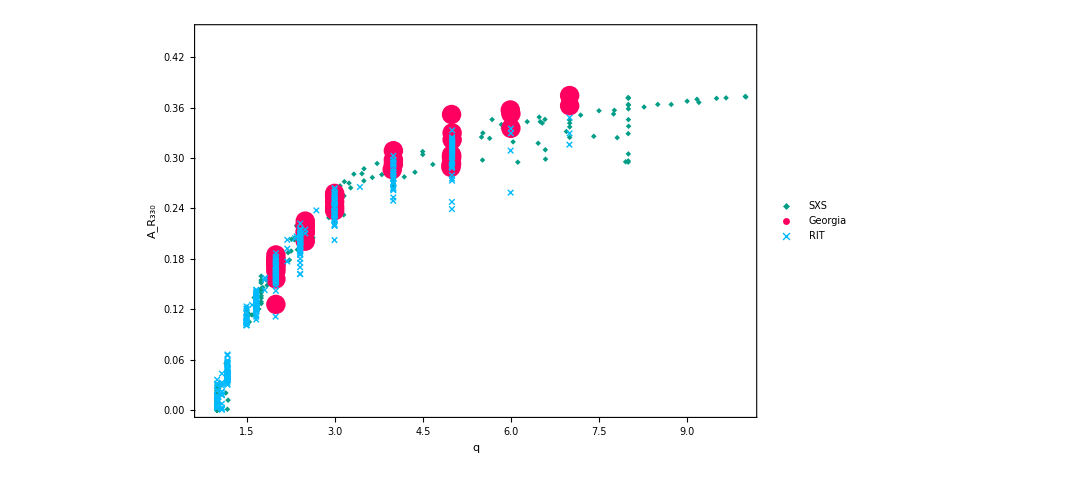

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,3}],TakeColumn[geoampratfin,{1,3}],TakeColumn[ritampratfin,{1,3}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
allampratfin=Join[sxsampratfin,geoampratfin,ritampratfin];
```

```mathematica
ansatz33=((-b0-c0-e0)+b0/qq+c0/qq^2+e0/qq^3)*(1+a1*χ+a2*χ^2)
```

(-b0-c0-e0+e0/qq^3+c0/qq^2+b0/qq) (1+a1 χ+a2 χ^2)

```mathematica
Table[massratamp=Select[allampratfin,Abs[#[[1]]-i]≤ 0.05&];RankedMax[massratamp[[All,3]],2]/RankedMin[massratamp[[All,3]],1],{i,{1,2,3,4,5,6,7,8}}]
```

{3.57150616238683229×10^7,1.7170236999982177,1.3091814453728097,1.231459500691121,1.3920139079562114,1.3630838890098847,1.1468406183317351,1.2600046609896475}

```mathematica
fitamp33=NonlinearModelFit[allampratfin,ansatz33,{b0,c0,e0,a1,a2},{qq,χ}]
```

FittedModel[(0.421575+0.0146839/qq^3+0.130108/qq^2-0.566367/qq) (1+0.0220623 χ-0.092414 χ^2)]

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

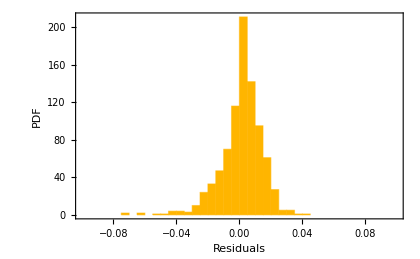

```mathematica
h1=Histogram[fitamp33["FitResiduals"],"PDF",PlotRange->{{-0.1,0.1},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

```mathematica
μA=Mean[fitamp33["FitResiduals"]]
σA=StandardDeviation[fitamp33["FitResiduals"]]
```

0.00125427

0.0129942

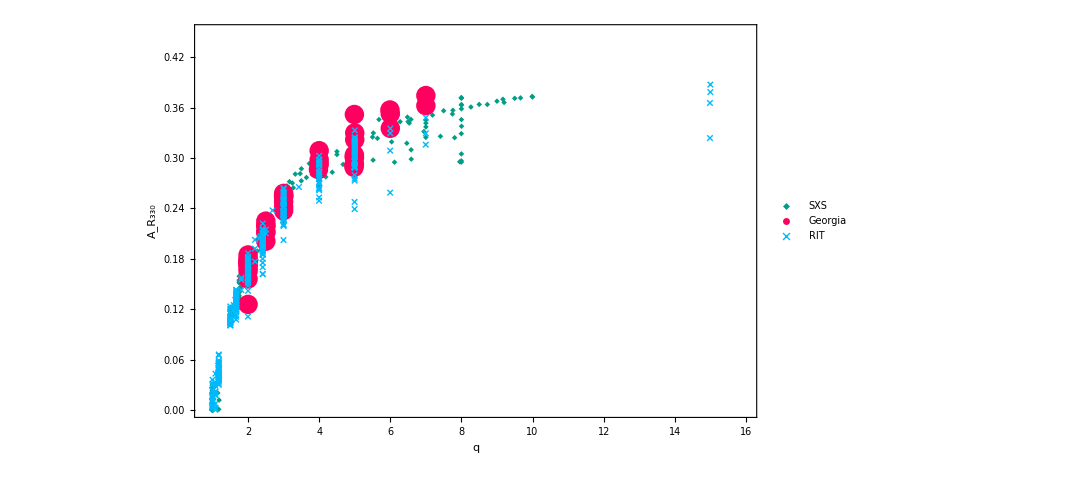

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,3}],TakeColumn[geoampratfin,{1,3}],TakeColumn[ritampratfin,{1,3}]},PlotRange->{{0.8,16},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{11.3,0.14}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_33.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_33.pdf

```mathematica
amprat1sgima=Select[allampratfin,1.5≤ #[[1]]≤ 2.5&];
```

```mathematica
amprat1sgima2=Select[amprat1sgima,xspmin<=#[[2]]≤ xspmax&]
```

{{1.99977444810648186,0.849820177313257652,0.152454924645995056},{1.9998536404745233,0.84985665817581213,0.15404704750100376}}

```mathematica
xspmin
```

0.833124

```mathematica
StandardDeviation[δt33[amprat1sgima[[All,1]]/(amprat1sgima[[All,1]]+1)^2,amprat1sgima[[All,2]]]]
Median[δt33[amprat1sgima[[All,1]]/(amprat1sgima[[All,1]]+1)^2,amprat1sgima[[All,2]]]]
```

0.959994

4.44662

```mathematica
amprat1sgima2
```

{{1.99977444810648186,0.849820177313257652,0.152454924645995056},{1.9998536404745233,0.84985665817581213,0.15404704750100376}}

```mathematica
Median[δt33[amprat1sgima2[[All,1]]/(amprat1sgima2[[All,1]]+1)^2,amprat1sgima2[[All,2]]]]
```

7.77468

```mathematica
dtdist=SmoothKernelDistribution[δt33[amprat1sgima[[All,1]]/(amprat1sgima[[All,1]]+1)^2,amprat1sgima[[All,2]]]]
```

DataDistribution[…]

```mathematica
dt33max=NMinimize[{χfun[x,dtdist],3≤ x≤8},{x}]
```

{1.12894,{x→4.16767}}

```mathematica
chi2dt33=dt33max[[1]]
dt33max[[2]]
chi2dt33min=x/.FindRoot[χfun[x,dtdist]==chi2dt33+1,{x,4}]
chi2dt33max=x/.FindRoot[χfun[x,dtdist]==chi2dt33+1,{x,7}]
```

1.12894

{x→4.16767}

3.71712

4.85332

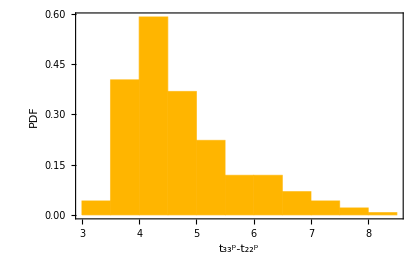

```mathematica
hp=Histogram[δt33[amprat1sgima[[All,1]]/(amprat1sgima[[All,1]]+1)^2,amprat1sgima[[All,2]]],10,"PDF",ImageSize->420,Frame->True,FrameLabel->{"t_33^p-t_22^p","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

```mathematica
Export["~/Desktop/RDFits_330/t33_t22.pdf",hp]
```

~/Desktop/RDFits_330/t33_t22.pdf

```mathematica
tNR[0.007,290]-tNR[0.007,330]
```

0.594139

```mathematica
tNR[0.0017,330]
```

1.04611

```mathematica
tNR[0.007,360]-tNR[0.007,330]
```

-0.358959

```mathematica
(* Amplitude remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,Mod[3/2(sxs22[[All,2]])-sxs33[[All,2]],π]}];
geophdiff=Transpose[{geomassratio,geospin,Mod[3/2(geo22[[All,2]]-π)-geo33[[All,2]],π]}];
ritphdiff=Transpose[{ritmassratio,ritspin,Mod[3/2(rit22[[All,2]]-π)-rit33[[All,2]],π]}];
```

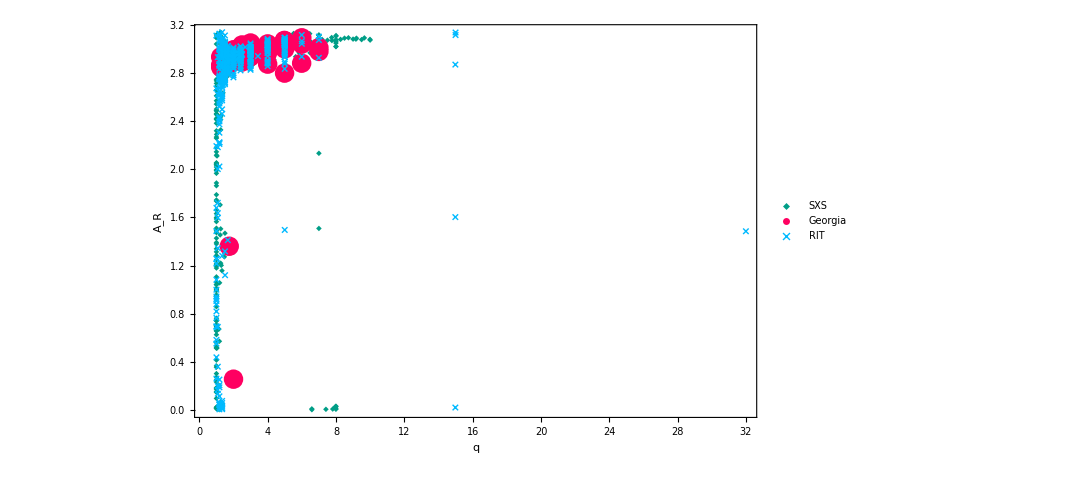

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,3}],TakeColumn[geophdiff,{1,3}],TakeColumn[ritphdiff,{1,3}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

```mathematica
sxsouts1=Position[sxsphdiff,_?(#[[1]]≤    1.1&)];
sxsouts=Join[sxsouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0.999833170061147247⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
geoouts=Position[geophdiff,_?(#[[1]]≤   1.1&)]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.25⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
ritouts1=Position[ritphdiff,_?(#[[1]]≤    1.1&)];
ritouts=Join[ritouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsphdifffin=Select[Delete[sxsphdiff,sxsouts],#[[-1]]≥ 2&];
geophdifffin=Select[Delete[geophdiff,geoouts],#[[-1]]≥ 2&];
ritphdifffin=Select[Delete[ritphdiff,ritouts],#[[-1]]≥ 2&];
```

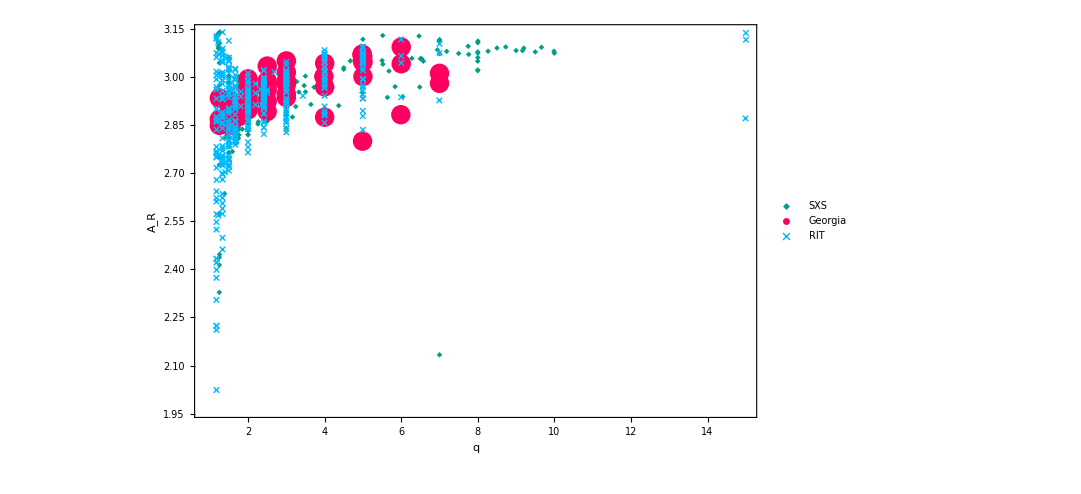

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdifffin,{1,3}],TakeColumn[geophdifffin,{1,3}],TakeColumn[ritphdifffin,{1,3}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,PlotRange->All,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,26],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",3},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.75,0.85}]]
```

```mathematica
allphdifffin=Join[sxsphdifffin];
```

```mathematica
dm=(1-1/qq)/(1+1/qq);
χ=χs+χa dm/(1-2ν)
ansatz33ph=a+b*Sqrt[(dm)]+c*dm+d*χ+dm^2*(e+f*χ)*χ;
```

((1-1/qq) χa)/((1+1/qq) (1-(2 qq)/(1+qq)^2))+χs

```mathematica
fitph33=NonlinearModelFit[allphdifffin,ansatz33ph,{a,b,c,d,e,f},{qq,χs,χa}]
```

FittedModel[2.53228085+0.925763715 √((1-1/qq)/(1+1/qq))-(«1»)/(1+«1»)+«58» (((1-1/(«2»)) χa)/((1+1/(«2»)) («1»))+χs)+((1-1/qq)^2 ((«1»)/(«1»)+χs) (-0.2821717-«58» ((«1»)/(«1»)+χs)))/(1+1/qq)^2]

```mathematica
μϕ=Mean[fitph33["FitResiduals"]]
σϕ=StandardDeviation[fitph33["FitResiduals"]]
```

0.

0.13772

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

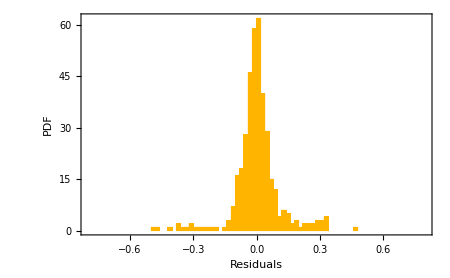

```mathematica
h1=Histogram[Select[fitph33["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

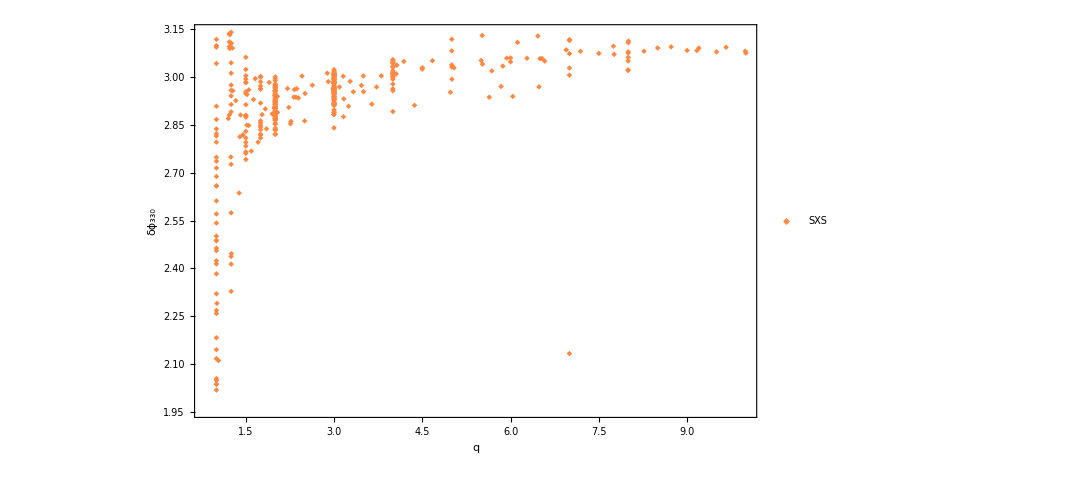

```mathematica
lphse=ListPlot[TakeColumn[sxsphdifffin,{1,-1}],Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->All,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{10.3,2.35}]]
```

```mathematica
Export["~/Desktop/RDFits_330/phase_q_33.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_33.pdf

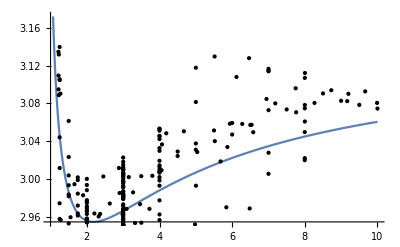

```mathematica
(* Comparison between the Cotesta et al. phase difference and ours. Notice that they fit at the peak of the 22 which adds a difference of 0.2 rads. *)
Plot[seobnrfits33[q,0]+0.2,{q,1,10},Epilog->{Point[Delete[TakeColumn[sxsphdifffin,{1,3}],331]]}]
```

```mathematica
FinalSpinUIB2017[0.16,-1,-1]
```

-0.0948031

```mathematica
0.7*3
```

2.1

### Mode 33 new ansatz with χa

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxsspina,sxs33[[All,1]]/sxs22[[All,1]]}];
geoamprat=Transpose[{geomassratio,geospin,geospina,geo33[[All,1]]/geo22[[All,1]]}];
ritamprat=Transpose[{ritmassratio,ritspin,ritspina,rit33[[All,1]]/rit22[[All,1]]}];
```

```mathematica
sxsouts1=Position[sxsamprat,_?(Abs[#[[1]]-7]<0.1&& #[[4]]≤ 0.2&)];
sxsouts2=Position[sxsamprat,_?(1.2<#[[1]]<2&& #[[4]]≤ 0.1&)];
sxsouts=Join[sxsouts2,sxsouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
geoouts1=Position[geoamprat,_?(1.1≤ #[[1]]<2&& #[[4]]≤ 0.2&)];
geoouts=Join[geoouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ritouts1=Position[ritamprat,_?(Abs[#[[1]]-5]<0.1&& #[[4]]≤ 0.2&)];
ritouts2=Position[ritamprat,_?(1.2<#[[1]]<2&& #[[4]]≤ 0.1&)];
ritouts3=Position[ritamprat,_?(Abs[#[[1]]-15]<0.1&& #[[4]]≤ 0.2&)];
ritouts4=Position[ritamprat,_?(#[[1]]>16&)];
ritouts=Join[ritouts1,ritouts2,ritouts3,ritouts4];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsampratfin=Delete[sxsamprat,sxsouts];
geoampratfin=Delete[geoamprat,geoouts];
ritampratfin=Delete[ritamprat,ritouts];
```

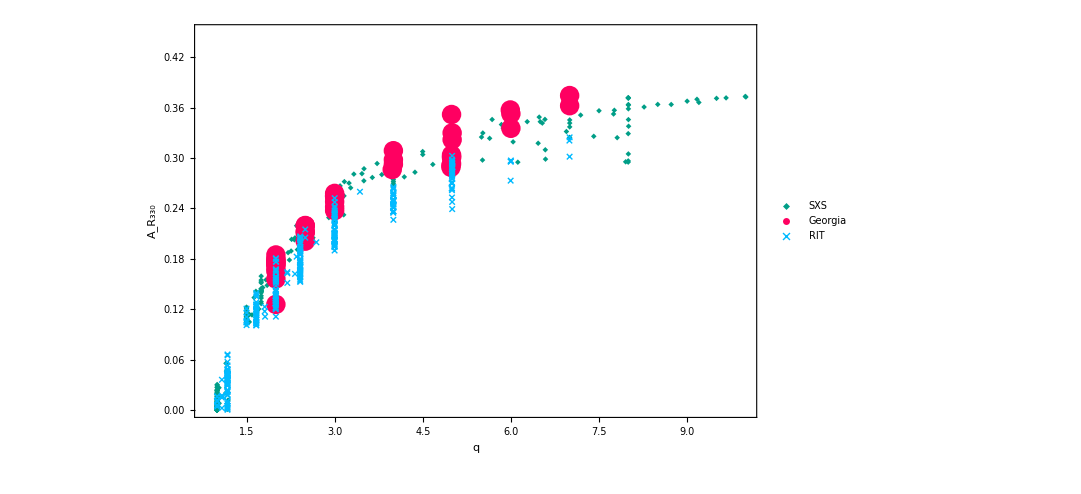

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}],TakeColumn[geoampratfin,{1,4}],TakeColumn[ritampratfin,{1,4}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
allampratfin=Join[sxsampratfin,geoampratfin];
```

```mathematica
npdata=Select[allampratfin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
ν=qq/(qq+1)^2
```

qq/(1+qq)^2

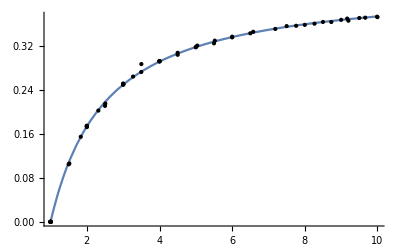

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

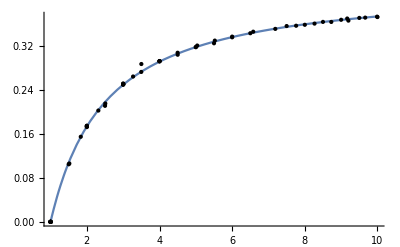

```mathematica
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
npdata2=Delete[npdata,outliers];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
allampratfinred=Complement[allampratfin,npdata];
fitamp33new=NonlinearModelFit[allampratfinred,nspansatz+b0(χa+Sqrt[1-4 ν]χs),{b0},{qq,χs,χa},MaxIterations->1000]
```

FittedModel[0.50018102508136526 √(1-(4 qq)/(1+qq)^2)+0.088290343313539563 (1-(4 qq)/(«1»)^2)-«59» (1-«1»)^(3/2)+(0.0137966-4.41934×10^-17 ⅈ) (χa+√(1-(4 qq)/(1+qq)^2) χs)]

```mathematica
μA=Mean[fitamp33new["FitResiduals"]]
σA=StandardDeviation[fitamp33new["FitResiduals"]]
```

0.00503741-8.67834×10^-11 ⅈ

0.00973286

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

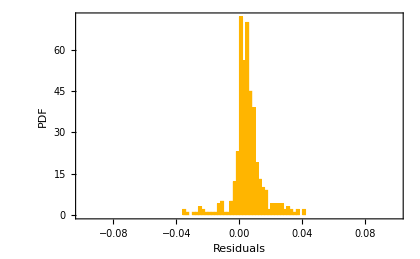

```mathematica
h1=Histogram[Chop[fitamp33new["FitResiduals"]],"PDF",PlotRange->{{-0.1,0.1},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

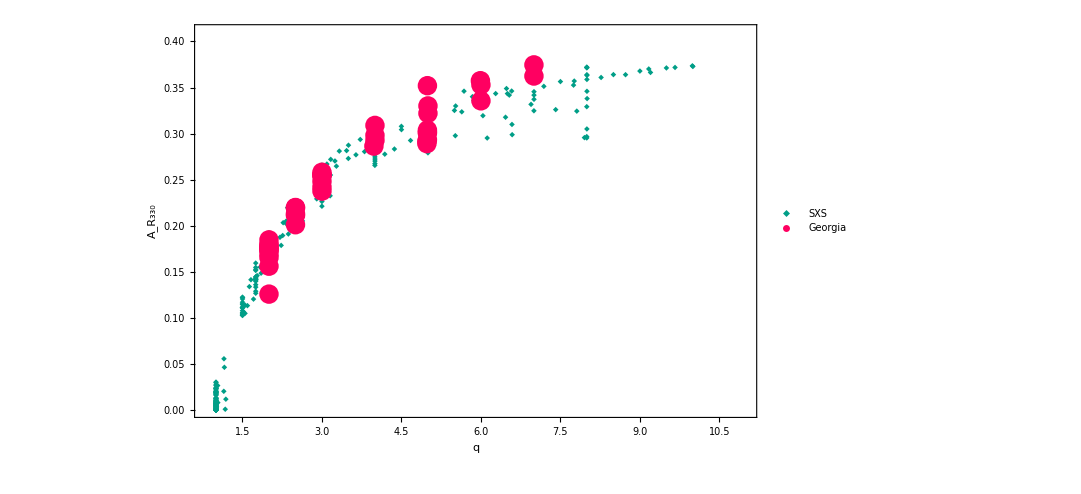

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}],TakeColumn[geoampratfin,{1,4}]},PlotRange->{{0.8,11},{0,0.41}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{7.3,0.13}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_33.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_33.pdf

```mathematica
(* Amplitude remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,Mod[3/2(sxs22[[All,2]])-sxs33[[All,2]],π]}];
geophdiff=Transpose[{geomassratio,geospin,Mod[3/2(geo22[[All,2]]-π)-geo33[[All,2]],π]}];
ritphdiff=Transpose[{ritmassratio,ritspin,Mod[3/2(rit22[[All,2]]-π)-rit33[[All,2]],π]}];
```

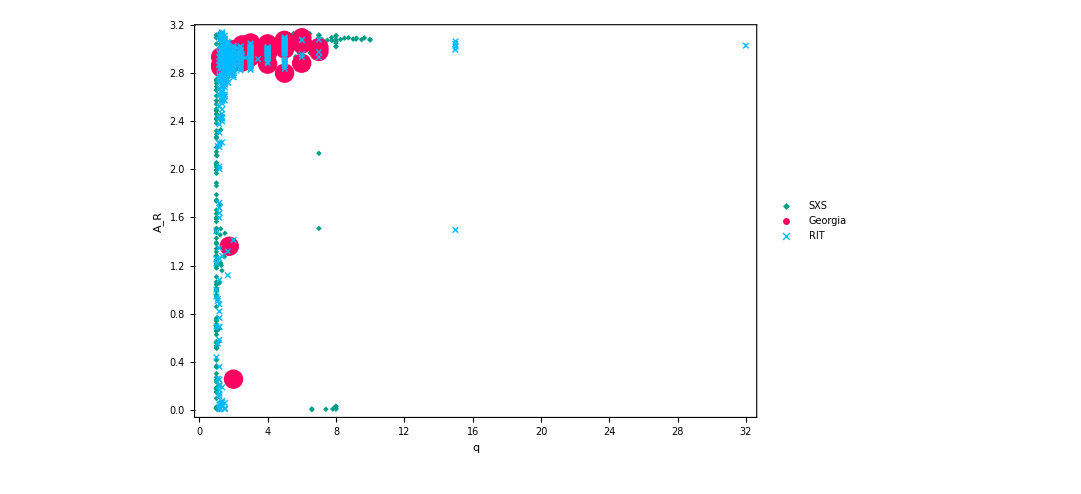

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,3}],TakeColumn[geophdiff,{1,3}],TakeColumn[ritphdiff,{1,3}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

```mathematica
sxsouts1=Position[sxsphdiff,_?(#[[1]]≤    1.1&)];
sxsouts=Join[sxsouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
geoouts=Position[geophdiff,_?(#[[1]]≤   1.1&)]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.25⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
ritouts1=Position[ritphdiff,_?(#[[1]]≤    1.1&)];
ritouts=Join[ritouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsphdifffin=Select[Delete[sxsphdiff,sxsouts],#[[-1]]≥ 2&];
geophdifffin=Select[Delete[geophdiff,geoouts],#[[-1]]≥ 2&];
ritphdifffin=Select[Delete[ritphdiff,ritouts],#[[-1]]≥ 2&];
```

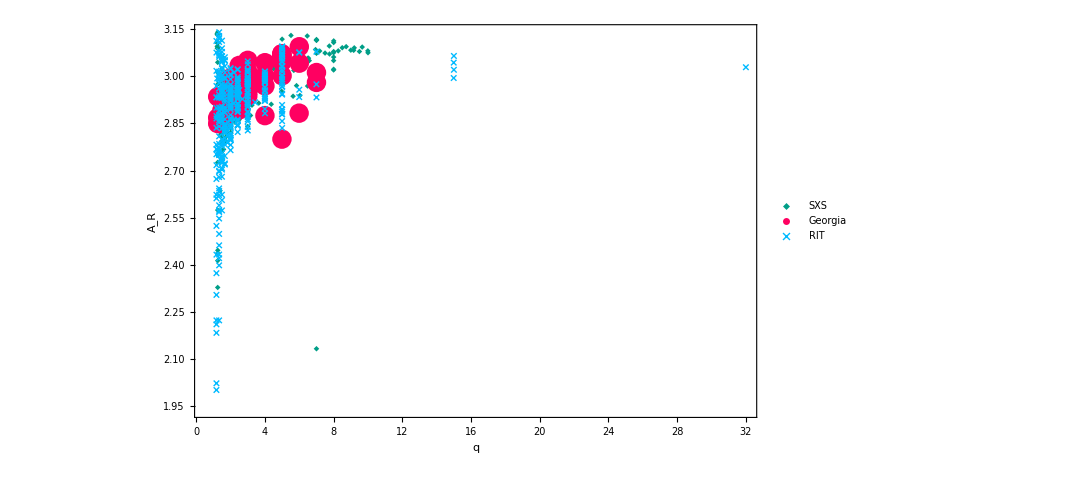

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdifffin,{1,3}],TakeColumn[geophdifffin,{1,3}],TakeColumn[ritphdifffin,{1,3}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,PlotRange->All,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,26],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",3},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.75,0.85}]]
```

```mathematica
allphdifffin=Join[sxsphdifffin,geophdifffin];
```

```mathematica
dm=(1-1/qq)/(1+1/qq);
ansatz33ph=a+b*Sqrt[(dm)]+c*dm+d*χ+dm^2*(e+f*χ)*χ;
```

```mathematica
fitph33=NonlinearModelFit[allphdifffin,ansatz33ph,{a,b,c,d,e,f},{qq,χ}]
```

FittedModel[2.9470987797830908-0.40738102963952187 √((1-1/qq)/(1+1/qq))+(«59» «1»)/(1+1/(«2»))+«59» χ+((1-1/qq)^2 (-0.42951439814151294-«59» χ) χ)/(1+1/qq)^2]

```mathematica
μϕ=Mean[fitph33["FitResiduals"]]
σϕ=StandardDeviation[fitph33["FitResiduals"]]
```

0.

0.08620395189653517

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

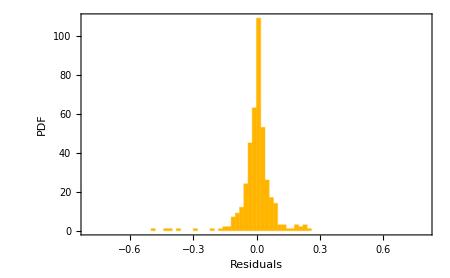

```mathematica
h1=Histogram[Select[fitph33["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

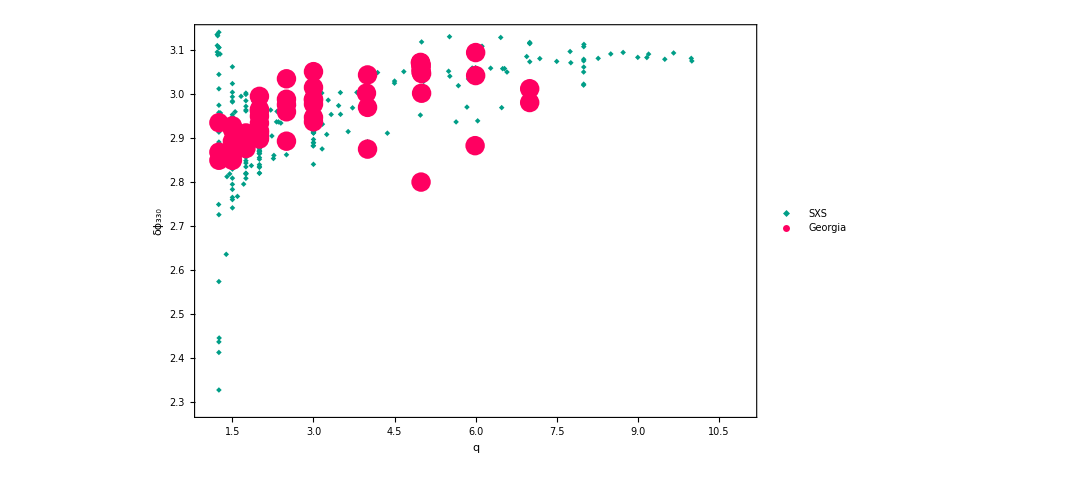

```mathematica
lphse=ListPlot[{Delete[TakeColumn[sxsphdifffin,{1,3}],331],TakeColumn[geophdifffin,{1,3}]},Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->{{1,11},All},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{7.452,2.55}]]
```

```mathematica
Export["~/Desktop/RDFits_330/phase_q_33.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_33.pdf

### Mode 33 new ansatz with χa just SXS

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxsspina,sxs33[[All,1]]/sxs22[[All,1]]}];
```

```mathematica
sxsampratfin=sxsamprat;
```

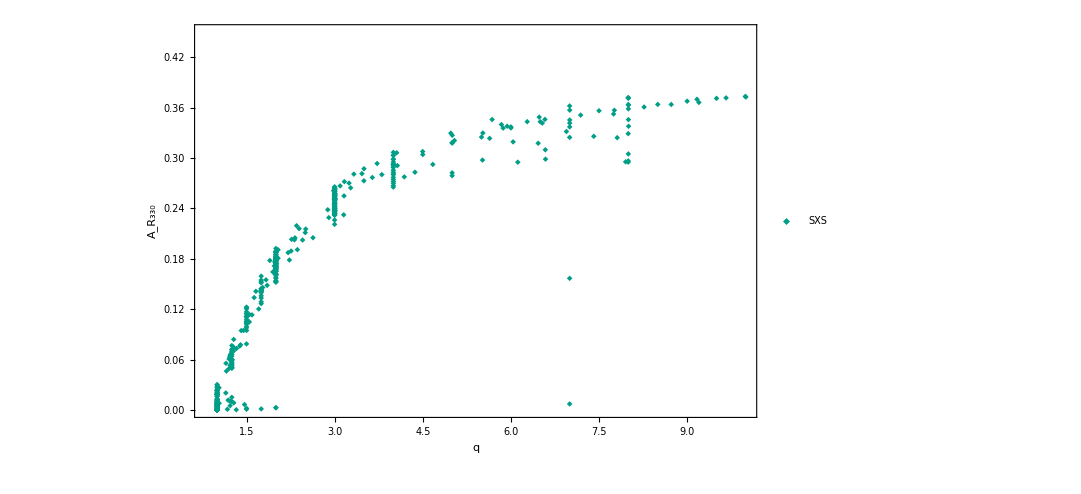

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
(* Fit first non-spinning data *)
allampratfin=Join[sxsampratfin];
npdata=Select[allampratfin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
ν=qq/(qq+1)^2
```

qq/(1+qq)^2

a0 √(1-(4 qq)/(1+qq)^2)+a1 (1-(4 qq)/(1+qq)^2)

0.048385625

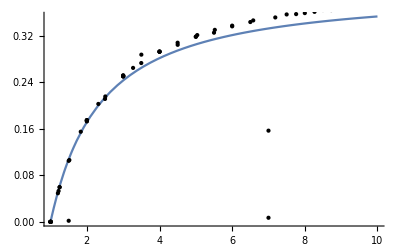

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
nspansatz=a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2
StandardDeviation[nspfit["FitResiduals"]]
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

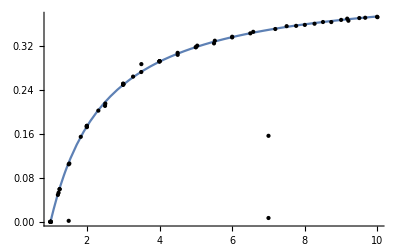

```mathematica
(* Eliminate outliers *)
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
npdata2=Delete[npdata,outliers];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
Normal[nspfit]+b0(χa+Sqrt[1-4ν]χs)
```

0.56614122565840837 √(1-(4 qq)/(1+qq)^2)-0.1330529487384592 (1-(4 qq)/(1+qq)^2)+b0 (χa+√(1-(4 qq)/(1+qq)^2) χs)

```mathematica
(* Fit the equal-massratio, unequal spin data. *)
allampratfinred=Complement[allampratfin,npdata];
fitamp33new=NonlinearModelFit[allampratfinred,Normal[nspfit]+b0(χa+Sqrt[1-4ν]χs),{b0},{qq,χs,χa},MaxIterations->1000]
μA=Mean[fitamp33new["FitResiduals"]]
σA=StandardDeviation[fitamp33new["FitResiduals"]]
```

FittedModel[0.56614122565840837 √(1-(4 qq)/(1+qq)^2)-0.1330529487384592 (1-(4 qq)/(((«1»«1»)^2))+0.0156441615 (χa+√(1-(4 qq)/(1+qq)^2) χs)]

-0.0025

0.0191

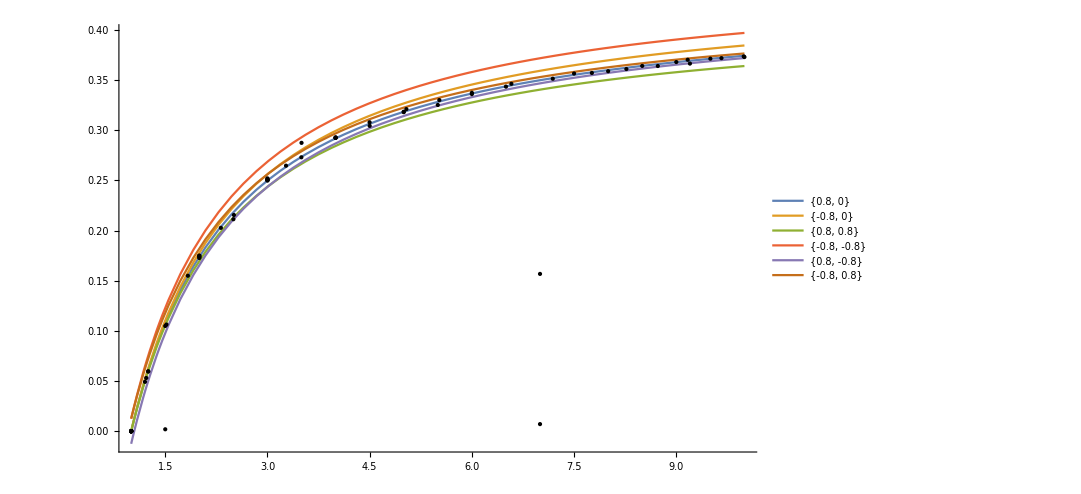

```mathematica
fitspin=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->0.8/.χa->0;
fitspin2=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->-0.8/.χa->0;
fitspin3 =Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->0.8/.χa->0.8;
fitspin4=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->-0.8/.χa->-0.8;
fitspin5=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->0.8/.χa->-0.8;
fitspin6=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->-0.8/.χa->0.8;
Plot[{Normal[nspfit],fitspin,fitspin2,fitspin3,fitspin5,fitspin6},{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]],PlotLegends->ToString/@{{0.8,0},{-0.8,0},{0.8,0.8},{-0.8,-0.8},{0.8,-0.8},{-0.8,0.8}},ImageSize->800]
```

```mathematica
(* Outlier hunter *)
outliers=Position[fitamp33new["FitResiduals"],_?(Abs[#]≥ 3st&)]
allampratfinred2=Delete[allampratfinred,outliers];
fitamp33newfinal=NonlinearModelFit[allampratfinred2,Normal[nspfit]+b0(χa+Sqrt[1-4ν]χs),{b0},{qq,χs,χa}];
μA=Mean[fitamp33newfinal["FitResiduals"]]
σA=StandardDeviation[fitamp33newfinal["FitResiduals"]]
```

{{190},{214},{220}}

-0.0015

0.0143

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

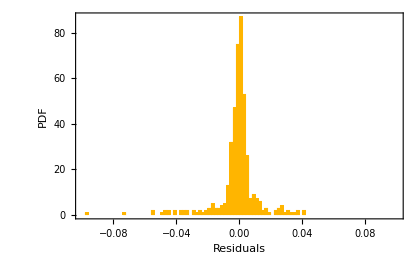

```mathematica
h1=Histogram[Chop[fitamp33newfinal["FitResiduals"]],"PDF",PlotRange->{{-0.1,0.1},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

```mathematica
amp33χeff=allampratfin/.{qq_,as_,aa_,aaa_}->{qq,(aa+Sqrt[1-4(qq/(qq+1)^2)]as),aaa};
```

```mathematica
amp33χeff
```

{{1,0.699854909623999988,0.00945575000861851647},{1,-0.699888332117499984,0.0267974097536350015},{1,0.699814384351000018,0.0183404644734315314},{1,-0.699855903766000015,0.0270786823338066057},{1,0.399897220050312877,0.00577406314410521244},{1,-0.399930074257421991,0.00908847796265799548},{1,0.599917655811500028,0.00507370317653978805},{1,0.161382333239000003,0.0063150344534583255},{1,-0.199948020901499962,0.00434391086515004687},{1,-0.599958758873500003,0.0233113127469819482},{1,-0.199941672024999989,0.00542739662155886239},{1,0.599909496460500014,0.0162913850471614154},{1,0.199929227595499998,0.00805616292674008029},{1,-0.599927724089999975,0.023288853723739696},{1,0.19992733595749998,0.00747640568804470318},{1,-0.295535618535500019,0.00679051013897368786},{1,-0.558204445674499977,0.0184784237655004581},{1,-0.031270341988499983,0.000351227373650940256},{1,0.099912684360500006,0.00393445408152538333},{1,0.199992502680149591,0.00843111019442707013},{1,-0.200000317129345151,0.00816756900604357341},{1,0.799834989283000009,0.0231669232351850282},{1,0.499494128322500008,0.016426979447093798},{1,0.299993340514499995,0.012342233892631487},{1,-0.300080707736500016,0.012373036725133538},{1,-1.3477000016×10^-8,7.74762945508984067×10^-7},{1,-0.499984379708499987,0.0203259950647441681},{1,2.49445500034×10^-7,5.31003333323393307×10^-7},{1,-0.499504049137,0.0197410371728098539},{1,-4.619999994×10^-9,9.91214313860389939×10^-8},{1,-1.743465011499996×10^-7,3.51082889401926986×10^-7},{1,-1.15181500004×10^-7,2.46962717654938222×10^-7},{1,-4.8470000014×10^-8,5.53165003104163333×10^-9},{1,6.09000017×10^-10,1.73783742779448982×10^-7},{1,-1.7284999987×10^-8,7.05363630787051984×10^-8},{1,-6.34250380000008×10^-10,7.38483797403398223×10^-8},{1,-6.29773875×10^-10,6.89714913724559014×10^-8},{1,-6.32996804999998×10^-10,6.43247533340277748×10^-8},{1,-6.3765713649999×10^-10,6.96168684967836505×10^-8},{1,-6.38253195999996×10^-10,6.24072685894322027×10^-8},{1,-6.39267288999991×10^-10,6.3603159284588432×10^-8},{1,9.48500001×10^-10,5.56610654959017473×10^-7},{1,5.45999968×10^-10,1.7145691759566194×10^-9},{1,8.460425188500053×10^-10,2.65199600399444394×10^-8},{1,-1.215000003×10^-9,2.92605889469426721×10^-9},{1.00000000007799983,1.0833×10^-10,3.64536568752144358×10^-8},{1.000000000542,-7.5661085×10^-10,2.3072541488801349×10^-8},{1.00000000142584544,3.×10^-9,1.97782189277915154×10^-8},{1.00000000389740973,7.×10^-9,3.02071049713632387×10^-8},{1.00000000421205404,-3.2×10^-8,8.23358411702598725×10^-8},{1.00000000451005144,5.34669×10^-8,3.62838860081915887×10^-6},{1.00000000506999665,1.×10^-8,9.50059046532946218×10^-8},{1.00000000746408246,3.98308×10^-8,3.66908025818866949×10^-6},{1.00000000802805422,-2.×10^-8,1.37231388046523488×10^-6},{1.00000000816605006,8.×10^-9,2.66325316263016648×10^-6},{1.00000000872038131,-8.×10^-9,1.2960807283399999×10^-8},{1.00000001314186293,-2.8×10^-8,1.44194337744767681×10^-9},{1.00000001677894912,1.3×10^-8,5.78207522071780501×10^-7},{1.00000002692214429,1.5×10^-8,1.34920299345346436×10^-9},{1.00000003043738461,-9.×10^-9,1.3180141883352404×10^-8},{1.00000003573825347,2.×10^-9,6.17105045416066576×10^-7},{1.00000004975018175,6.49×10^-8,8.75308980818507185×10^-10},{1.00000006061627933,8.38×10^-8,7.9980232192481114×10^-8},{1.00000009944088952,-8.7×10^-9,3.88555491323956357×10^-8},{1.000000126314319,-2.69×10^-8,4.03540352935631961×10^-7},{1.00000012737881572,-9.2×10^-9,1.4244025078532276×10^-7},{1.00000015456041691,-8.353×10^-8,8.23749938084099221×10^-9},{1.00000015659869512,2.512×10^-7,2.01960659372761759×10^-7},{1.00000033892773499,0.1000015228,0.00425724555783319414},{1.00000043998067922,2.2791×10^-7,2.36864877818029598×10^-6},{1.0000005584782603,-0.00031982651,9.65782787603620321×10^-6},{1.00000126794661526,-0.071129762548,0.002598455495493378},{1.00000127222712232,-0.14999832464,0.000285905472243188644},{1.00000158745770373,0.14999904089,0.00607261083735310827},{1.00000176331004487,0.38927252612,0.00672023340645846967},{1.00000222872380773,-0.599976878977,0.0161029820209303256},{1.000003394569001,0.007366428389,0.000222886407044091215},{1.00000342826381461,-0.800157319141,0.0187343640800461193},{1.00000364359946681,-0.899689082049,0.0218622002659687682},{1.00000373262560061,-0.799870834107,0.00108180279431017749},{1.00000444818654111,-0.599952771157,0.0243500268275913189},{1.00000648120883096,-0.799840809512,0.0301820526882284507},{1.0000065815739323,-0.799832560129,0.029520210747479167},{1.00000737220828362,-0.89974042196,0.0106931215804346022},{1.00000797256142548,0.10932630495,0.0043177163613081136},{1.00000924000558156,-8.7357×10^-6,6.0019175791245564×10^-6},{1.00001437786835679,0.49997106755,0.0195059808257809896},{1.00001444389990346,0.0999927718282,0.00176574004938517083},{1.00001571866706751,-0.10022272407,0.000248243195816901957},{1.00001723765377881,-0.5002022363,0.0178378816968784922},{1.00001842496205873,-0.299990208628,0.010906110864738802},{1.00001854356975795,-0.299987234583,0.012703891734488081},{1.00001983309619025,0.299997417097,0.00920833734646055075},{1.00002085677552821,-0.187486558279,0.00650948097800708274},{1.00002153429693319,0.299988544122,0.00101418333730403166},{1.00002223794683931,-0.187487560238,0.0025605153471018905},{1.00002377803774767,-0.300217698679,0.00403992201150782387},{1.00002588956458904,0.199994840669,0.00643275076341343601},{1.00002712112578274,0.199988943277,0.00206572003547105408},{1.00005594742401049,0.12277608916,0.00285011216849930055},{1.00005705457775229,0.3323856863841,0.000536976480831592329},{1.00005964976260331,-0.149990308888,0.000755825840480033017},{1.00006006267781333,0.149991366765,0.000945203791875799319},{1.00006763663018972,-0.548743518374,0.0202821433565862023},{1.00007150854145044,-0.284480795565,0.00984672775373135153},{1.00011452824124314,0.1999700582699,0.000456564254343975472},{1.00012784372051855,-0.1999637372553,0.00730888232771099076},{1.00014813935435853,-0.4499319898305,0.013124706937138504},{1.00014902141593876,-0.1999821516068,0.00760239362845487637},{1.00016092300454096,0.4499727806961,0.00153915605958485561},{1.000165315627358,-0.4499558032099,0.0184910424913763389},{1.0001722326499698,0.2000321296483,0.0045561499857309023},{1.00017981690142155,0.4500169168176,0.0107149860501561329},{1.0004591540143728,-0.24992304204128,0.00981069627068224402},{1.00046013187110661,0.24992628835673,0.00358379130876647814},{1.00999242849352156,-0.121890706512273,0.00323846957619090411},{1.03210143635857232,0.5025915058866666,0.0263965855343355667},{1.03482274834136412,-0.118764485962871,0.00786924714796634177},{1.14739162953147855,-0.05919987247017183,0.0201644382725764046},{1.15060149697689607,0.742006785032574,0.0554906265994166668},{1.15836747086506064,0.4747010441511568,0.0462293522207147857},{1.17453317367482391,-0.8510862613437134,0.000702203245209584441},{1.18597400882920678,0.08971733209741421,0.0116075203489372128},{1.20246156413194405,-0.000070953774597771679,0.0492195528272030712},{1.20300462316174639,0.46683070445101952,0.060618073121678772},{1.21747754656543328,0.48044691093595269,0.0640784258791290399},{1.21833806682114987,0.41177826184722869,0.0105137688370104095},{1.21997216659965213,0.41219848115331316,0.0628323387498136576},{1.22000697964939042,0.41222092008319439,0.0619761868268367092},{1.22118145476587814,0.00005085690218402886,0.0530537451793158731},{1.22120260345201648,0.41234791504894872,0.00500026744723744884},{1.22780183836752532,0.40904053171330707,0.0643719714435515691},{1.22783037074076451,0.46934442180108347,0.0662368628789071457},{1.24560796718588196,-0.06456965362548896,0.0578692509216537581},{1.24982320997355001,0.75547114072958643,0.0766291483026737063},{1.24983916845030474,-0.355476360272194897,0.00997256258741886327},{1.24984423424119862,-0.0447242358467485,0.0600097459309113096},{1.24984703335518033,-0.48891402325002592,0.0548141495284812841},{1.24985469204256994,-0.62230094154507076,0.0538086167821441436},{1.24985477220939023,-0.0888560172001175,0.0589221781323657131},{1.24988119814305065,-0.75569865699893687,0.0526041138344220036},{1.24990383329449362,0.4887178607441156,0.0720556440476889508},{1.24990684762310234,0.22197414224758184,0.0662064351826505521},{1.24991246999656402,0.355399292078823907,0.0686200093107944926},{1.24995245746718631,0.45782935692211771,0.0697051096292757044},{1.24998478313457317,-0.17770392523801492,0.0563291882754429529},{1.250001489576962,0.177803793360469066,0.0639740171404429752},{1.2500424084081001,-0.00007969987851436364,0.0594640073159428891},{1.25006419508643307,-0.3558834568493712,0.0150048450391760708},{1.25006778098350924,-0.00002677741793839252,0.059783712571356741},{1.25007351880692497,-0.71140950578485552,0.0495188415644590095},{1.25010929982332697,0.71097519333004978,0.071737843153665359},{1.2501093924798421,0.3554419035694984,0.0599423376287601102},{1.25453174888790997,-0.76231130848453251,0.0506535148291876062},{1.27181454426461382,0.46394599096506044,0.0751876751921465684},{1.27909028331492358,0.23270299788289959,0.0701598037011902936},{1.28210187801439424,0.84650634203521572,0.0839585686826919961},{1.28284399388008352,-0.343702477654102142,0.00839397598227338774},{1.32563119509328109,-0.30583554187087153,0.000134482135669912875},{1.32965900284675143,-0.208927187312085,0.0731977102349378952},{1.38570774526536122,-0.76691160931258827,0.0761194369953806451},{1.39918242159443129,-0.6247706903682019,0.0775581084129407777},{1.41001923510205818,0.2116277856376273,0.0944716927957666203},{1.44999710211215183,0.2196239583049057,0.094655641630246464},{1.46624239719831362,0.062631393533850543,0.00637810777472720445},{1.49958481798890486,0.3799410677804787,0.0786100917674920964},{1.49982617185552924,0.15977296631737486,0.111459757591964515},{1.4998476398001459,0.319850830596930562,0.115078947848960282},{1.49988608547060842,0.63976402532222681,0.000743612484266532575},{1.49989441051980466,-0.320030997993053433,0.102518025581354352},{1.49990092948571752,0.79972774884276467,0.122377824566269097},{1.49990442515201838,-0.48015002060635529,0.0994837195363245042},{1.49996433682184227,-0.59939389902515198,0.110708559660407205},{1.49996609211754883,0.59939657949257115,0.11437105905296185},{1.49997255400837237,0.1597804875301581,0.105608712492001645},{1.49999285237285518,0.64010081839473109,0.111396840385575951},{1.49999927986295178,7.008608188273545×10^-9,0.104892767617883373},{1.50000721765042311,-0.00001360892294639618,0.00194289562052166425},{1.50001642843471528,-0.48044662463977034,0.0978049643611994033},{1.50003563574463494,0.1999978594119854,0.107750153577624195},{1.50010191473421428,-0.160114336916141086,0.103535771109784457},{1.50011859018790927,0.79984019122376647,0.116900561655135324},{1.50067571892016294,-0.39978122783890734,0.102760889662702386},{1.50067859723195696,-0.39977874957764183,0.110686747921262971},{1.50067960150687862,0.39978201081184704,0.120414284011274424},{1.50068035264748789,-0.39977520069803041,0.0946267312601301098},{1.50068441819298704,0.39977421585573309,0.121879557522620651},{1.51751400823489546,0.000059844779009671757,0.106283899823345671},{1.5191394238679532,-0.2762242149071238,0.105947756150519157},{1.54822656856423202,-0.53653939912817281,0.104771601428713193},{1.55028299806547087,-0.1452124441630969,0.113608878937161641},{1.59333155488661271,-0.56433854066215263,0.113172207224583325},{1.62997468950055291,0.45779035110966267,0.13383123099219143},{1.65972676700699373,0.43565011403046898,0.14130012117550617},{1.70796712645821769,-0.98604279383748799,0.120250812714068005},{1.74961266985885944,0.2546778334983947,0.14165538989600177},{1.74964068161553965,0.290930873858584348,0.151393489045512346},{1.74964512464232369,0.83629202118265023,0.159359060120245162},{1.74965132715970029,0.47269885522485465,0.154658377326902608},{1.74966220202330836,0.07274511023258561,0.144212573080198775},{1.74967035810313321,-0.83653288352723,0.12881454942782725},{1.74974471101731299,-0.07296530611537596,0.14439330539399977},{1.74974656744096024,-0.10916353065576376,0.142820427127231159},{1.74974873401178011,-0.25487865942241356,0.14080709820812428},{1.74978482629031906,-0.145225414213416966,0.14148977385154624},{1.74978934852320944,-0.47296123417493305,0.13590739036546242},{1.74983755951745534,-0.29106390827172611,0.13960090374093053},{1.74992092629771578,-0.87310145786617065,0.12663660594871522},{1.7499804131193355,0.145383915191806258,0.00115614261138535334},{1.74998540436236705,-0.58238953444446517,0.13327052452309667},{1.75009971074302873,0.87267661597218031,0.15245030797299896},{1.75026490861444661,0.58154706363180544,0.14193048688641021},{1.77617802327317609,-0.07346550341318532,0.145774645325092199},{1.83202563889436121,-0.00018576150244969249,0.154952172097867357},{1.85107654934752675,0.52345092045051709,0.148392274270382},{1.8968815369404346,0.95001616560534425,0.178029313098444367},{1.94888417558118765,-0.176051278652585868,0.164357394243840203},{1.97278766174301312,0.75000982143259173,0.171470284777494844},{1.98092463106344496,0.21779907320982211,0.176171954545059599},{1.99941812120011586,-0.65451794426455387,0.16162061281437567},{1.99943989096448727,0.65458873096452394,0.187463574012392114},{1.9995081525906433,-0.65462151842073363,0.161969487030373975},{1.99956593092011836,-0.15460918979244682,0.171068419497831895},{1.99957181642518234,0.65465732864228602,0.188044031671424241},{1.99959106497926942,-0.15464011239394748,0.171896287378222157},{1.99962070084625232,-0.266333677277480388,0.169609560745455804},{1.99964116910115397,0.15456331658030533,0.179611020317914491},{1.99966313138363283,0.15450882702820229,0.178538439014194192},{1.99966556994414835,1.1543550433922542,0.186958978738309477},{1.99966704513921911,0.066593251296013542,0.173968033847988255},{1.99968745195337516,0.53334919430345164,0.16107325480405054},{1.99970845412158149,0.000069202721372596841,0.174911067916269066},{1.99972211164746683,0.6000431049689068,0.181999747416270252},{1.99973798885329135,-1.1544577247875631,0.15226992676123301},{1.99974152847846454,-0.56657131011123066,0.00267522454080842719},{1.99974293455233232,0.26643047746278907,0.181888927821231075},{1.99974297768117437,-0.133438061083549007,0.170523887729360847},{1.99976169489738309,0.13324649946128221,0.177547951460415852},{1.99976914074732504,-0.26708402495115213,0.169181811112616925},{1.99977444810648186,0.56650352877947062,0.152454924645995056},{1.9997898198126165,-1.1544053916882312,0.00247499149071988178},{1.99979694714424361,-0.33355965680998802,0.167771837257516021},{1.99979841103767853,-0.56659302772255926,0.16492824974251334},{1.99980581723126849,-0.53399911510055301,0.164995077272106693},{1.9998267177096114,-1.0670643318750862,0.15291173823437134},{1.99982828055076012,0.80000066736075206,0.187636939005681029},{1.99983101509671335,-0.19980010797933451,0.17078612160383942},{1.99985028403609189,0.26670456480383074,0.177686967979092343},{1.99985362554178892,1.1544488296745275,0.184893595912030233},{1.9998536404745233,0.56654416026336594,0.15404704750100376},{1.99986175980577308,0.0999844292349684055,0.189188540263651619},{1.99986689611648161,-0.3999990453411448,0.167206809350351324},{1.99987231584891667,0.100013509834304765,0.177097842915930906},{1.99987849410901486,0.19981595820014986,0.178040505920228245},{1.99991337837730221,0.200063839606839331,0.17886907405602071},{1.99991463014211046,0.33338268396827169,0.17638050398414803},{1.99991908460202605,-0.20003892401387421,0.170429512135878012},{1.99992025328378631,-0.30002029775270621,0.16773694650559332},{1.99992413923231327,0.40007195259102994,0.183043402902856005},{1.99992503922132814,-0.40005510878868893,0.165466076030963519},{1.99992970143400139,0.29999766552475709,0.179462402743922318},{1.99993411194152659,0.3330388153049896,0.177530926279683785},{1.99993443590862552,-0.200013003152538834,0.169552066620124079},{1.99993899037831491,-0.33303785288080014,0.192357662921086219},{1.99994583636714562,-0.40006264952521223,0.167160937314221826},{1.99994813051966514,0.40005958790282259,0.17455471956354159},{1.99994938969116975,0.5334687561896519,0.184813262233626275},{1.99995546904391652,0.79998245444842891,0.187872792341212281},{1.99995707919839361,0.39992162161242979,0.17494650677670536},{1.99995877889294182,0.19990260706541956,0.180210395217733907},{1.99996970728736145,-0.7999915163617426,0.156822944616642251},{1.99997003527465322,0.19997904154793439,0.178734265682620355},{1.9999702079195727,-0.0999491174140949726,0.171985909206097},{1.99997072039842205,0.39994108173167985,0.180828498459578638},{1.99997076911775173,-0.3999410850316105,0.174221217908005053},{1.99997164789263304,-0.19997840951557479,0.188617360041186392},{1.99997211514157902,-0.79992546259181108,0.157977637386398256},{1.99997238981538827,0.33347428691961955,0.181527080391114297},{1.99998050356705348,4.9584579512492889×10^-6,0.17347254531339266},{1.99998146618130868,0.60002688219513848,0.181146853335217273},{1.99998403070331099,-0.33334836916569568,0.168201895570723435},{1.9999913602681576,-0.59995473920577281,0.160570128959750911},{1.99999692528125528,7.2731882919610921×10^-8,0.174897430948323667},{1.99999755270159607,0.60003257741080983,0.181226773439740852},{2.00000926523585632,-0.60049230353901961,0.161415567629348367},{2.00001534208706389,0.000042491393772798122,0.17409350612558412},{2.0000156643623046,0.73340224300732491,0.184625964979942545},{2.00003387114787357,-0.46714154575923702,0.165238711768821093},{2.00005766976384569,0.19984307741867944,0.177491388453427227},{2.00008690163809444,-0.066822254455169174,0.173885979841020933},{2.0001057308485759,-0.59994687618405384,0.16177144552232437},{2.00010679724234475,-0.29997290448456392,0.176309722745370448},{2.000107171845805,0.2999741904319797,0.182695371269895135},{2.00010766156133046,-0.000071976265292431965,0.172617137035670109},{2.03770641314054313,0.26763128561936337,0.180746685572810968},{2.03778885641204743,0.60338235065502118,0.190787093369810319},{2.20795364632573143,-0.38353266822413826,0.18738301060585418},{2.23005369003763843,-0.84997452325772237,0.178589701980586393},{2.25891534475228495,0.57837450162247169,0.189293590555760797},{2.26747242478833799,0.31220546641773651,0.203233991628341279},{2.31620095629884748,0.000080730227843397124,0.20267282438190884},{2.32500070181090734,-0.02861741340970558,0.2049908655933539},{2.3521055780003195,1.1181835298455492,0.219466523465059448},{2.36574515065443558,-0.85223049456026331,0.190951273261662165},{2.39550744824854478,0.26732211218871808,0.21601877969842547},{2.45413199149414174,-0.69260675337149682,0.202393715414267346},{2.49999681558138365,3.6329522374955539×10^-8,0.211253477803756127},{2.50740461598841069,-0.000070577421967738513,0.215480421730442904},{2.63119532999675077,-1.0796159648031141,0.205162469912131532},{2.88302820842609098,-0.3448121730531866,0.238478651795526447},{2.90128307712237987,-0.76601363966299308,0.229098130361840387},{2.98309975970613905,0.676286217544732659,0.261045069084559207},{2.99471793062454461,0.75609169399278549,0.244715175407606252},{2.99901791125741069,0.501547911433889912,0.262845587654831588},{2.99903428079335166,0.12338073410427544,0.252259830537584485},{2.99909764748199903,-0.50139972426816938,0.240308895273677818},{2.99918885298575244,0.84994294790275681,0.22111958642196949},{2.99919948212670873,-1.1265581786102568,0.226250931405605061},{2.99923013756126178,-0.85001852652283849,0.233515835768260316},{2.99925759776103407,0.50154242935320436,0.262208938796675623},{2.99926068776968169,-0.12344168710469096,0.250688997894224329},{2.99926601796701942,-0.501591517054567787,0.239948192348152131},{2.99926609966052071,1.12646222164922906,0.262346923075233207},{2.99929638299383239,-0.12350127112279611,0.251597086697781607},{2.9993011553272324,0.000011274227638460069,0.250444465483531711},{2.99938589017975898,0.12338704249565935,0.252204936862104551},{2.99957324227768174,0.650083022339438264,0.263892327081298984},{2.99961279982890527,-0.899949009616097708,0.231806713197770028},{2.99967109065204385,-0.899958085708793703,0.232974904583495316},{2.99968161258423827,-0.35005355049963315,0.24568691176662043},{2.99968627568175217,-0.650117475103598373,0.236629530559006625},{2.9997245932591845,-0.60004407474057933,0.238477091241320282},{2.99972853639676229,-0.29998301128006114,0.245458465900297366},{2.9997593967269891,0.72516945389433133,0.251028849044371232},{2.99977109504244899,-0.0749868416398330878,0.245876373166409188},{2.99977211863274507,0.0749864829992616842,0.250037131554558445},{2.99977338155215412,0.72516652545206019,0.252241656066292437},{2.99978785404347681,-0.49955350739996943,0.25130212576681871},{2.99978855479010553,0.72503775219729065,0.25167756732831655},{2.99979491599934978,0.34997101381680828,0.256280396772700714},{2.99980065631008541,0.59995350588491455,0.25480439044847839},{2.99980103246553131,-0.49994029312795338,0.242229709475705286},{2.99980438647431136,0.749260532592571632,0.263182930313258342},{2.99980739703501964,0.49956194725743624,0.252882595324156325},{2.99982555151024544,-0.149892794182901755,0.247042447534530705},{2.99982769972142016,0.49956303154225314,0.258077688762672905},{2.99983848523315499,-0.49955944114635602,0.240553173547824591},{2.99984228987656731,0.34993190117410974,0.256005424435287678},{2.99985367957761095,0.649990966364952331,0.265845338460483959},{2.9998589605526238,-0.59994059849759011,0.239739877231144083},{2.99987179975918261,-0.72486246327558907,0.237580284494294297},{2.99987266050807788,0.149917310047113315,0.254059052031670252},{2.99987420853346443,-0.650010632069715813,0.237467559399820071},{2.99989720598787546,0.899955633988143488,0.264042657658677672},{2.99989910756287825,0.44994463251025623,0.260196294990781967},{2.99990354262638004,0.900000156025748257,0.264890702731000828},{2.99990863452906442,-0.72487907620546551,0.237399279183850301},{2.99991848591549459,-0.72489500735849704,0.237325994850254055},{2.9999275537098602,-0.72488189374601007,0.237151612283978067},{2.999928911067546,0.29996995483626554,0.251556887530394897},{2.99992947244196717,0.44993667334130351,0.255366027632815722},{2.99993046180725242,-0.4499364779113095,0.241710275810274136},{2.99993152665944995,-0.29996851447237885,0.246625712956047334},{2.99994455345893574,-0.34998825743502408,0.245149061654634494},{2.99994531334598324,-0.14994421199730993,0.248028870893065936},{2.99995824276194911,0.149896725889137078,0.255372294676880141},{2.99997404141761015,-0.000018277831556702064,0.251101382958277043},{2.99997406836412495,-0.74992728428424364,0.234023789157806544},{2.99997437623979169,-0.000017767696024458486,0.250740002814727497},{2.99997783905952753,-0.849943620388499007,0.234384594848274982},{2.99998925703684627,0.65005935523263404,0.256681462677054452},{2.99998939428386047,3.0665940068376925×10^-6,0.249948473985720881},{2.99999116903074814,-0.850105600541939428,0.232565670861516106},{2.99999224111651586,4.7896610135177436×10^-7,0.251939339781422364},{2.99999409397231309,-0.64993901100833818,0.237714367647799895},{2.99999644255640741,0.0749369399688902692,0.253390201129230446},{3.00000472742680513,0.849911975644710948,0.261075201476809124},{3.0000200490215807,0.74989541304265348,0.260775395649662345},{3.00003530752227121,0.37495169745942757,0.257214729332644758},{3.00005261637617293,-0.75005607521029056,0.235717005332875637},{3.00005373200969849,-0.0750130870948934003,0.249541802755211715},{3.0000587876625735,0.59989126635208935,0.257673837689727439},{3.00006863181072614,-0.37512256935581606,0.242857392534632926},{3.00007010602364366,0.850027531833491502,0.26360086638907439},{3.00007332557626771,0.65004940695410575,0.257429476879729421},{3.00007683747231235,-0.44987398547243704,0.240589069013033141},{3.00009892929400035,1.4427797798682616×10^-6,0.249946986446825033},{3.00009966927829685,-0.64997976510955697,0.236857238353924843},{3.00010419281537244,0.49996300117721511,0.258025847329217843},{3.00012157090256171,0.3000260834438174,0.255840900152497976},{3.00014174486460306,0.74995327506278733,0.259450275280818231},{3.00015262627917467,-0.37496467114758794,0.255196801181848763},{3.00015315880110567,0.37496632380484258,0.250701908200042465},{3.00131662429877055,0.62455197871558668,0.25491089786669007},{3.00132086396168019,-0.62455872983889163,0.239102189614768031},{3.00132352957022075,0.62454242157902631,0.260081076826644612},{3.00132554603296331,0.62455775211558056,0.258105976749397891},{3.0013267259745815,-0.62452831517052971,0.243429486419401131},{3.0013276253154344,-0.6245494482577878,0.234735359854775154},{3.09302436076189036,0.544741605762950346,0.266909511602071117},{3.15412152422662739,-1.20899210142365023,0.23241651748491661},{3.15953048233459022,0.75385508228409235,0.255002775360231112},{3.16557579053526128,0.764128751813658199,0.271982339508017992},{3.24519388754760341,0.51629841700879781,0.270240365575191801},{3.27249733593264347,-0.000062715444405735101,0.264596261605109712},{3.32706660707206936,0.786506076031120623,0.280958022467250848},{3.46466470805301396,0.436638252896897529,0.281486844176940322},{3.49758719337826296,-0.0000727352959980095834,0.272947081661460389},{3.49999404154738292,2.2984933302920869×10^-7,0.287352928310912703},{3.64138562038676472,1.17500169390091386,0.276932716650465567},{3.72274561626903822,0.590142592478332452,0.293572985732895036},{3.80300493373429971,-0.253496960386839751,0.2803907435529156},{3.99843299326229795,-1.27986478318070662,0.265474826814814361},{3.99863348019610143,-0.159893028788464645,0.288872952358585231},{3.99864470978758213,-0.40009332339205533,0.285700136086677249},{3.99870330265769791,-0.720065233849391509,0.277051209492095298},{3.99894657087401306,-0.960207734915111665,0.274656380804538289},{3.9989579172213352,0.719920198368254378,0.306858513763906689},{3.99898636513538408,0.159747232543086884,0.298476520328211356},{3.99930464159392685,0.3999562868978602,0.298824255835322308},{3.99954501352372072,0.0000978183599949800333,0.292335623658582736},{3.99954615541003955,-1.2001083766395795,0.267400930218850768},{3.99964978904081203,0.560088157223099572,0.303081968569861358},{3.9997030093406698,0.4600807690643303,0.303662192382316739},{3.99971207506232629,0.0799552542150511038,0.295345822300841171},{3.99981229115457371,-0.0798605505584928581,0.290556458776966306},{3.99990374509858171,-0.560218784157751132,0.280958975996297724},{3.99993008756212864,1.04019656646149479,0.28037708925111219},{3.99993015942230912,-0.46004002859250265,0.283180665794149297},{3.99997659241979831,0.000019743701900828596,0.292288231351384993},{3.9999873960386072,6.08833804999553984×10^-7,0.292798012119812662},{4.00002634578081917,-1.12013125375300615,0.270143825994690936},{4.00017500527609293,-1.04002060909427782,0.272351984985958764},{4.00079771709380339,-0.000085399941321188666,0.292508512180858548},{4.05556899740116617,0.598985509252790162,0.306402757423266589},{4.0673469685475192,-0.24147577829413199,0.291122958676115879},{4.18560646993076624,-1.0710161360238917,0.27763931598225938},{4.36722154197910761,1.00139535943788955,0.283223343864971187},{4.49877334473311574,-0.0000473208253880342327,0.307865401735480192},{4.49998972744744386,2.5152708399784038×10^-7,0.304261502506023279},{4.67132485168632083,-0.872043043153203596,0.292499785314085772},{4.97759656610038803,0.878240526985498672,0.329743340328064431},{4.99998664505053281,3.83453466909552055×10^-7,0.317946398818146114},{4.99998832768057255,3.03296909495854188×10^-7,0.318379990848695796},{5.00003088870318191,-1.34980785628874198,0.28249011426563122},{5.00008517240252637,-1.34994513046743547,0.27906746022117059},{5.00217276740030847,0.749415328472072231,0.327197601666204316},{5.03880132213861653,0.000015219823365000978,0.32097470656915842},{5.49998517889315064,3.39398544880755609×10^-7,0.325101320915746261},{5.51649061142531672,-1.1246398387174836,0.29767511902564026},{5.52238181943924023,-0.0000546896448843041464,0.329951606400632054},{5.63827771239961884,1.14549146822691243,0.323593108659598254},{5.68056684629491393,0.743012646356934161,0.346019575400814721},{5.83909399588338118,0.910802155423961854,0.340007635030502194},{5.86830908671558227,0.080179387142554649,0.335819959787517752},{5.93695450932062041,0.010401641960970224,0.338026049539548514},{5.999948612748633,-5.50098472084364449×10^-6,0.335966491700134654},{5.99997866468523977,6.44688966852805264×10^-7,0.337202302652036659},{6.03752449014313353,1.237903215653414,0.31939107933571188},{6.11806711819592053,-1.35736693106370673,0.29515879094685102},{6.27778469719785637,0.124851808300983568,0.343428672722371704},{6.46414678489680483,-0.942215836232226345,0.31773410275497227},{6.48192228394193748,1.19461260310344188,0.348888533363091441},{6.49997454278802955,9.38919179304683932×10^-7,0.343389836041394025},{6.53492412756661434,-0.040948383087873084,0.34175576197239975},{6.57976519278279159,0.0000469527316942120391,0.34616739178606696},{6.585688599621629,-1.11506725454684661,0.30991163343221144},{6.58907381177218987,-1.27541920197616576,0.29878805948885827},{6.94514884714658987,-0.847074884312880121,0.33170708157098096},{6.99969718136948504,0.975008022145144921,0.362196614630070901},{6.99985499789343901,-0.974990679537050246,0.32473046446772932},{6.99997072307951918,1.04910287726082109×10^-6,0.00710148030148183213},{7.00000104487356989,6.17201373271158061×10^-6,0.156763846752319851},{7.00109174800436485,-0.649794536992587521,0.33721176265952643},{7.00116783510303176,0.649805846676324099,0.345468864978565721},{7.00121401845305513,-0.649805871620130677,0.34174246192139624},{7.00128749329637579,0.649790486368676067,0.357186300150124718},{7.18741315183494223,5.5230627269628795×10^-6,0.35127756679872598},{7.41068221169695551,-0.915821785158819456,0.32599513013025853},{7.49996698162289555,1.10446806685255724×10^-6,0.35644380802539723},{7.74755950734840848,-0.24284254962186193,0.35258498914353365},{7.76086773564685739,0.0000264414919485483818,0.35702285543513614},{7.80899464572236024,-1.09980617288430177,0.32435992683704753},{7.95324582280826231,-1.2809271035660443,0.29559432982160768},{7.99684353465357933,0.723283944865996158,0.37200652317638114},{7.99697632462155728,-1.42223456421412519,0.295238367239344947},{7.99712820973273164,-1.24438310261783795,0.296696733426304616},{7.99716151106829809,-0.922357637864845741,0.329176771416378661},{7.99826078364085369,0.557560320938021344,0.37131966510603392},{7.99913551366882913,1.04572255435575373,0.37200171882454789},{7.99935728118456702,-1.25173848346174294,0.305000267968876276},{7.99945666582823023,0.216004051326184503,0.36388639390566931},{7.9999692834078795,2.97013054750628659×10^-7,0.35875491442002036},{8.00039413100177121,-0.663069455213034104,0.34590291874178984},{8.00047296172615852,0.19402299365092655,0.36319324128984879},{8.00346463935680141,-0.83266246734978269,0.33799292202056983},{8.26745726906233358,1.7148662472897779×10^-6,0.36091309520665074},{8.49995612788065991,1.3924368810829399×10^-6,0.36401574928631345},{8.72877066093856158,1.5229524797394764×10^-6,0.36392625224536907},{8.99995135238133059,1.43415079268171599×10^-6,0.36786010549062885},{9.16729984214553006,0.0000208309435318319249,0.37013714068390172},{9.19994999085569098,-3.70050709657713882×10^-6,0.36634428348525716},{9.49994640569445714,1.47967051884191908×10^-6,0.37124251433921791},{9.66281618040365942,5.43629470496508702×10^-6,0.3717842147842832},{9.98950857441341178,0.0000234301511194668453,0.37354085859967575},{9.99994142027152932,1.43905740597199628×10^-6,0.37284677199812891}}

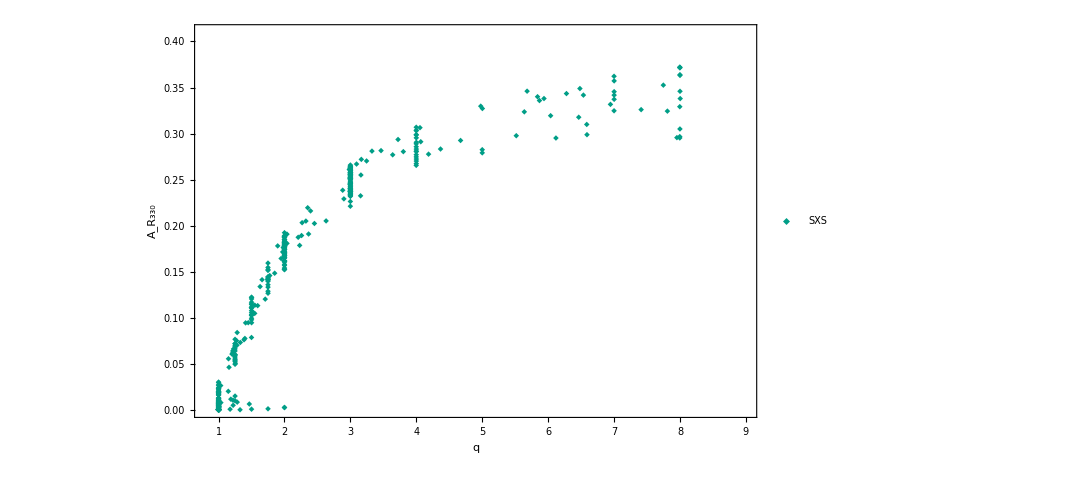

```mathematica
lamp=ListPlot[{TakeColumn[allampratfinred,{1,4}]},PlotRange->{{0.8,9},{0,0.41}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{6.3,0.13}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_33.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_33.pdf

```mathematica
(* Amplitude remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,sxsspina,Mod[3/2(sxs22[[All,2]])-sxs33[[All,2]],π]}];
```

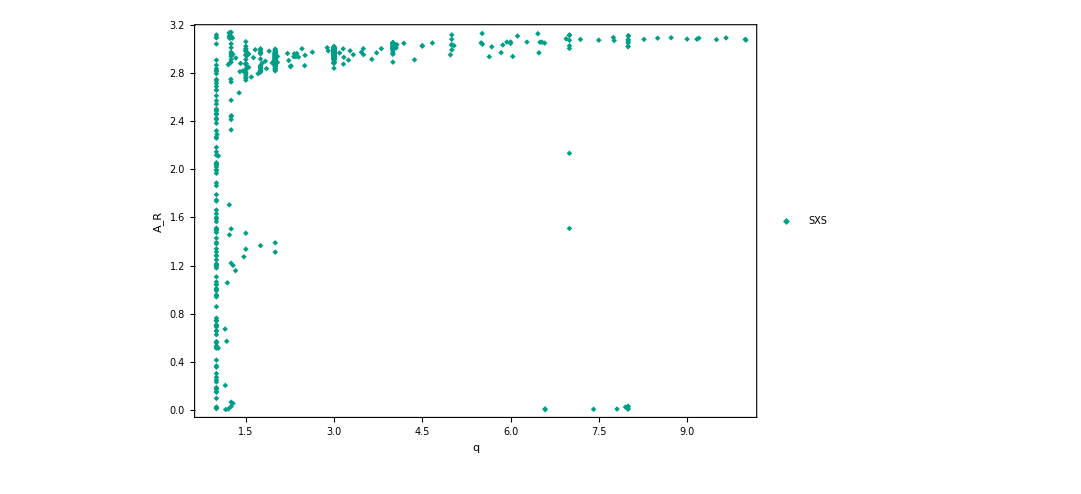

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,4}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

```mathematica
dm=(1-1/qq)/(1+1/qq);
χ=χs+χa dm/(1-2ν)
```

((1-1/qq) χa)/((1+1/qq) (1-(2 qq)/(1+qq)^2))+χs

```mathematica
ansatz33ph=a+b*Sqrt[(dm)]+c*dm+d*χ+dm^2*(e+f*χ)*χ;
fitph33=NonlinearModelFit[sxsphdiff,ansatz33ph,{a,b,c,d,e,f},{qq,χs,χa}]
```

FittedModel[1.42449311+3.78364612 √((1-1/qq)/(1+1/qq))-(«1»)/(1+«1»)-«58» (((1-1/(«2»)) χa)/((1+1/(«2»)) («1»))+χs)+((1-1/qq)^2 («1») (0.626566518-0.839629307 («1»)))/(1+1/qq)^2]

```mathematica
μϕ=Mean[fitph33["FitResiduals"]]
σϕ=StandardDeviation[fitph33["FitResiduals"]]
```

0.

0.6513

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

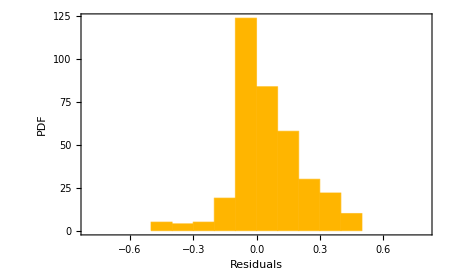

```mathematica
h1=Histogram[Select[fitph33["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

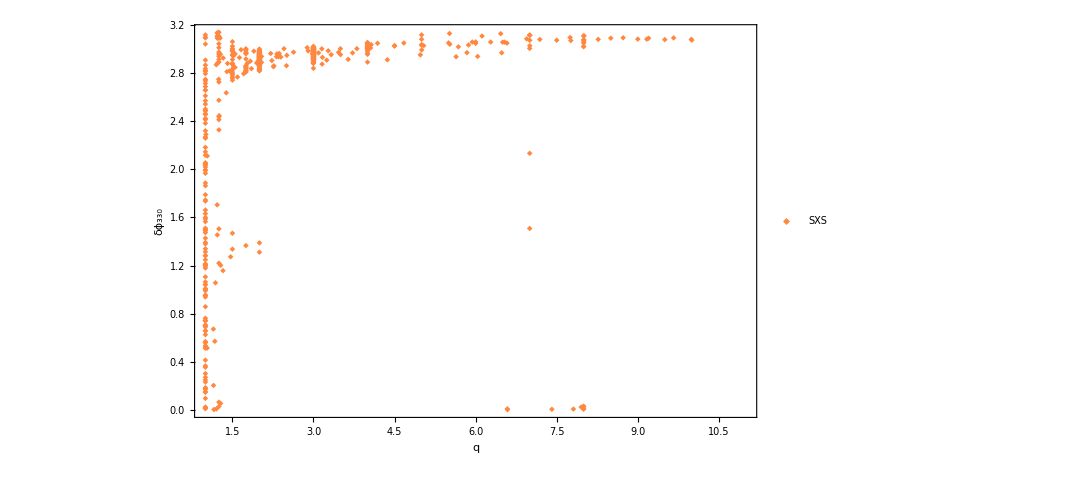

```mathematica
lphse=ListPlot[TakeColumn[sxsphdiff,{1,-1}],Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->{{1,11},All},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{7.452,2.55}]]
```

```mathematica
(* Outlier hunter *)
outliers=Position[fitph33["FitResiduals"],_?(Abs[#]≥ 5st&)]
allampratfinred2=Delete[sxsphdiff,outliers];
fitph33final=NonlinearModelFit[allampratfinred2,ansatz33ph,{a,b,c,d,e,f},{qq,χs,χa}];
μA=Mean[fitph33final["FitResiduals"]]
σA=StandardDeviation[fitph33final["FitResiduals"]]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{13},{14},{16},{17},{18},{20},{21},{22},{24},{25},{26},{27},{28},{31},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{45},{46},{47},{48},{49},{51},{52},{53},{55},{56},{58},{59},{60},{61},{62},{65},{66},{68},{69},{71},{72},{73},{74},{75},{76},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{91},{92},{94},{95},{96},{97},{99},{100},{101},{102},{103},{105},{106},{107},{109},{110},{111},{112},{113},{114},{115},{116},{117},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{140},{142},{143},{144},{145},{146},{147},{148},{149},{150},{152},{153},{155},{156},{157},{158},{159},{160},{163},{165},{167},{168},{169},{171},{174},{176},{178},{182},{184},{186},{189},{191},{209},{235},{241},{304},{306},{309},{311},{318},{319},{328},{329},{332},{350},{351},{357},{358},{359},{368},{370},{373},{375},{380},{388},{401},{413},{416},{417},{422},{427},{432},{433},{437},{441},{445},{446},{450},{459},{460},{462},{463},{467},{468},{469},{471},{472},{473},{474},{476},{479},{483},{484},{486},{487},{488},{491},{494},{496}}

0.

0.07147

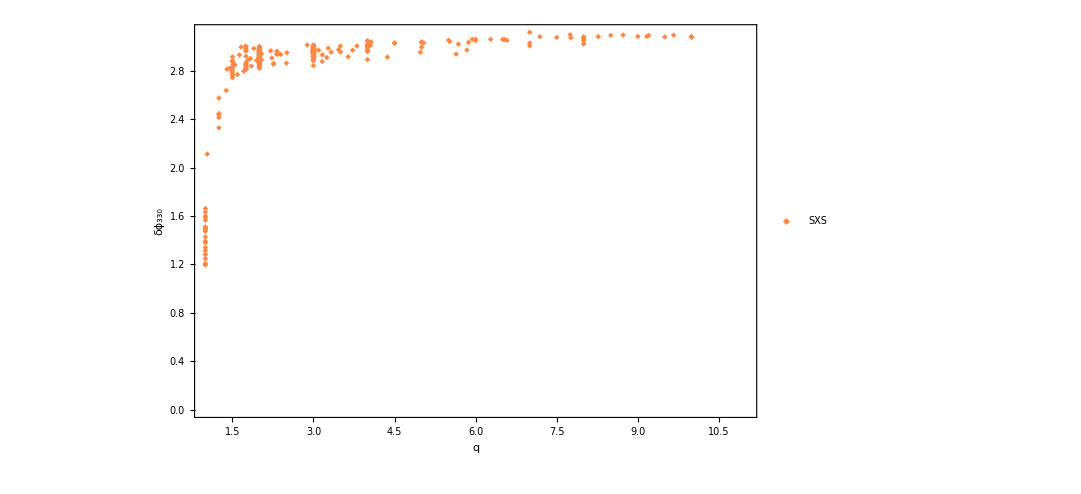

```mathematica
lphse=ListPlot[TakeColumn[allampratfinred2,{1,-1}],Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->{{1,11},All},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{7.452,1.5}]]
```

```mathematica
Export["~/Desktop/RDFits_330/phase_q_33.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_33.pdf

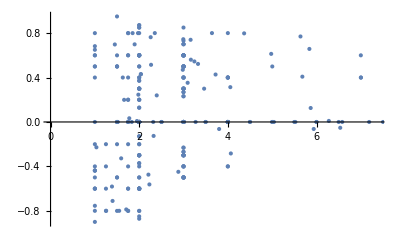

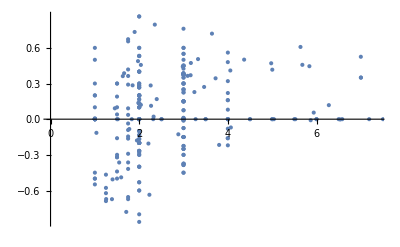

```mathematica
ListPlot[TakeColumn[allampratfinred2,{1,2}]]
ListPlot[TakeColumn[allampratfinred2,{1,3}]]
```

### Mode 33 new ansatz with χeff just SXS

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspina+sxsspin Sqrt[1-(sxsmassratio/(sxsmassratio+1)^2)],sxs33[[All,1]]/sxs22[[All,1]]}];
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxsspina,sxs33[[All,1]]/sxs22[[All,1]]}];
```

```mathematica
sxsampratfin=sxsamprat;
```

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,-1}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

-Graphics-

```mathematica
(* Fit first non-spinning data *)
allampratfin=Join[sxsampratnsp];
npdata=Select[allampratfin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
ν=qq/(qq+1)^2
```

qq/(1+qq)^2

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,-1}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
nspansatz=a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2
StandardDeviation[nspfit["FitResiduals"]]
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,-1}]]]]
```

a0 √(1-(4 qq)/(1+qq)^2)+a1 (1-(4 qq)/(1+qq)^2)

0.048385625

-Graphics-

```mathematica
(* Eliminate outliers *)
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
npdata2=Delete[npdata,outliers];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

-Graphics-

```mathematica
Normal[nspfit]+b0 χχ
```

0.56614122565840837 √(1-(4 qq)/(1+qq)^2)-0.1330529487384592 (1-(4 qq)/(1+qq)^2)+b0 χχ

```mathematica
(* Fit the equal-massratio, unequal spin data. *)
allampratfinred=Complement[allampratfin,npdata];
allampratfinred=allampratfinred/.{xx_,yy_,ww_,zz_}->{xx,ww+yy Sqrt[1-4 xx/(xx+1)^2],zz};

fitamp33new=NonlinearModelFit[allampratfinred,Normal[nspfit]+b0 χχ,{b0},{qq,χχ},MaxIterations->1000]
μA=Mean[fitamp33new["FitResiduals"]]
σA=StandardDeviation[fitamp33new["FitResiduals"]]
```

FittedModel[0.56614122565840837 √(1-(4 qq)/(1+qq)^2)-0.1330529487384592 (1-(4 qq)/(1+qq)^2)+0.02 χχ]

0.

0``-0.03943565670559857

```mathematica
fitamp33newpar[qq_,χχ_]:=Evaluate[Normal[fitamp33new]]
```

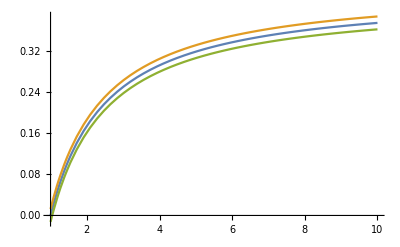

```mathematica
Plot[{fitamp33newpar[qq,0],fitamp33newpar[qq,0.8],fitamp33newpar[qq,-0.8]},{qq,1,10}]
```

```mathematica
fitspin=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->0.8/.χa->0;
fitspin2=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->-0.8/.χa->0;
fitspin3 =Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->0.8/.χa->0.8;
fitspin4=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->-0.8/.χa->-0.8;
fitspin5=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->0.8/.χa->-0.8;
fitspin6=Normal[nspfit]+Normal[fitamp33new][[-1]]/.χs->-0.8/.χa->0.8;
Plot[{Normal[nspfit],fitspin,fitspin2,fitspin3,fitspin5,fitspin6},{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]],PlotLegends->ToString/@{{0.8,0},{-0.8,0},{0.8,0.8},{-0.8,-0.8},{0.8,-0.8},{-0.8,0.8}},ImageSize->800]
```

-Graphics-

```mathematica
(* Outlier hunter *)
outliers=Position[fitamp33new["FitResiduals"],_?(Abs[#]≥ 3st&)]
allampratfinred2=Delete[allampratfinred,outliers];
fitamp33newfinal=NonlinearModelFit[allampratfinred2,Normal[nspfit]+b0(χa+Sqrt[1-4ν]χs),{b0},{qq,χs,χa}];
μA=Mean[fitamp33newfinal["FitResiduals"]]
σA=StandardDeviation[fitamp33newfinal["FitResiduals"]]
```

{{190},{214},{220}}

-0.0015

0.0143

```mathematica
h1=Histogram[Chop[fitamp33newfinal["FitResiduals"]],"PDF",PlotRange->{{-0.1,0.1},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

-Graphics-

```mathematica
amp33χeff=allampratfin/.{qq_,as_,aa_,aaa_}->{qq,(aa+Sqrt[1-4(qq/(qq+1)^2)]as),aaa};
```

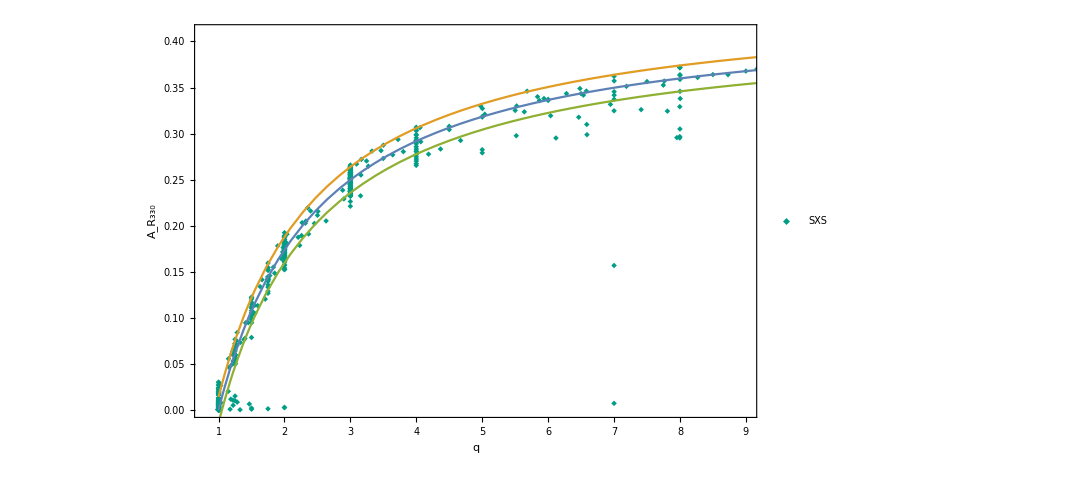

```mathematica
Show[lamp=ListPlot[{TakeColumn[allampratfin,{1,4}]},PlotRange->{{0.8,9},{0,0.41}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{6.3,0.13}]],
Plot[{fitamp33newpar[qq,0],fitamp33newpar[qq,0.9],fitamp33newpar[qq,-0.9]},{qq,1,10}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_33.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_33.pdf

```mathematica
(* Amplitude remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,sxsspina,Mod[3/2(sxs22[[All,2]])-sxs33[[All,2]],π]}];
```

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,4}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

-Graphics-

```mathematica
dm=(1-1/qq)/(1+1/qq);
χ=χs+χa dm/(1-2ν)
```

((1-1/qq) χa)/((1+1/qq) (1-(2 qq)/(1+qq)^2))+χs

```mathematica
ansatz33ph=a+b*Sqrt[(dm)]+c*dm+d*χ+dm^2*(e+f*χ)*χ;
fitph33=NonlinearModelFit[sxsphdiff,ansatz33ph,{a,b,c,d,e,f},{qq,χs,χa}]
```

FittedModel[1.42449311+3.78364612 √((1-1/qq)/(1+1/qq))-(«1»)/(1+«1»)-«58» (((1-1/(«2»)) χa)/((1+1/(«2»)) («1»))+χs)+((1-1/qq)^2 («1») (0.626566518-0.839629307 («1»)))/(1+1/qq)^2]

```mathematica
μϕ=Mean[fitph33["FitResiduals"]]
σϕ=StandardDeviation[fitph33["FitResiduals"]]
```

0.

0.6513

```mathematica
h1=Histogram[Select[fitph33["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

-Graphics-

```mathematica
lphse=ListPlot[TakeColumn[sxsphdiff,{1,-1}],Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->{{1,11},All},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{7.452,2.55}]]
```

-Graphics-

```mathematica
(* Outlier hunter *)
outliers=Position[fitph33["FitResiduals"],_?(Abs[#]≥ 5st&)]
allampratfinred2=Delete[sxsphdiff,outliers];
fitph33final=NonlinearModelFit[allampratfinred2,ansatz33ph,{a,b,c,d,e,f},{qq,χs,χa}];
μA=Mean[fitph33final["FitResiduals"]]
σA=StandardDeviation[fitph33final["FitResiduals"]]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{13},{14},{16},{17},{18},{20},{21},{22},{24},{25},{26},{27},{28},{31},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{45},{46},{47},{48},{49},{51},{52},{53},{55},{56},{58},{59},{60},{61},{62},{65},{66},{68},{69},{71},{72},{73},{74},{75},{76},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{91},{92},{94},{95},{96},{97},{99},{100},{101},{102},{103},{105},{106},{107},{109},{110},{111},{112},{113},{114},{115},{116},{117},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{140},{142},{143},{144},{145},{146},{147},{148},{149},{150},{152},{153},{155},{156},{157},{158},{159},{160},{163},{165},{167},{168},{169},{171},{174},{176},{178},{182},{184},{186},{189},{191},{209},{235},{241},{304},{306},{309},{311},{318},{319},{328},{329},{332},{350},{351},{357},{358},{359},{368},{370},{373},{375},{380},{388},{401},{413},{416},{417},{422},{427},{432},{433},{437},{441},{445},{446},{450},{459},{460},{462},{463},{467},{468},{469},{471},{472},{473},{474},{476},{479},{483},{484},{486},{487},{488},{491},{494},{496}}

0.

0.07147

```mathematica
fitph33finalfit[qq_,χs_,χa_]:=Evaluate[Normal[fitph33final]]
```

```mathematica
χ=χs+χa dm/(1-2ν)
phaserob[qq_,χs_,χa_]:=Evaluate[3.20275-1.47295 Sqrt[dm]+1.2121 dm -0.203442 χ+dm^2(-0.0284949-0.217949χ)χ]
```

((1-1/qq) χa)/((1+1/qq) (1-(2 qq)/(1+qq)^2))+χs

```mathematica
phaserob[qq,0,0]
```

3.20275-1.47295 √((1-1/qq)/(1+1/qq))+(1.2121 (1-1/qq))/(1+1/qq)

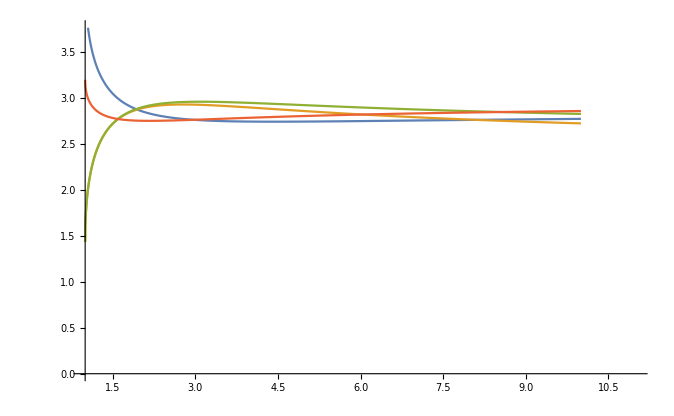

```mathematica
p1=Plot[{Mod[-fitph33finalfit[qq,0,0],π]+π-0.5,fitph33finalfit[qq,0.8,0.8],fitph33finalfit[qq,-0.8,-0.8],phaserob[qq,0,0]},{qq,1,10},PlotRange->{{1,11},{0,1.2π}}]
```

```mathematica
lphse=ListPlot[TakeColumn[allampratfinred2,{1,-1}],Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->{{1,11},All},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{7.452,1.5}]]
```

-Graphics-

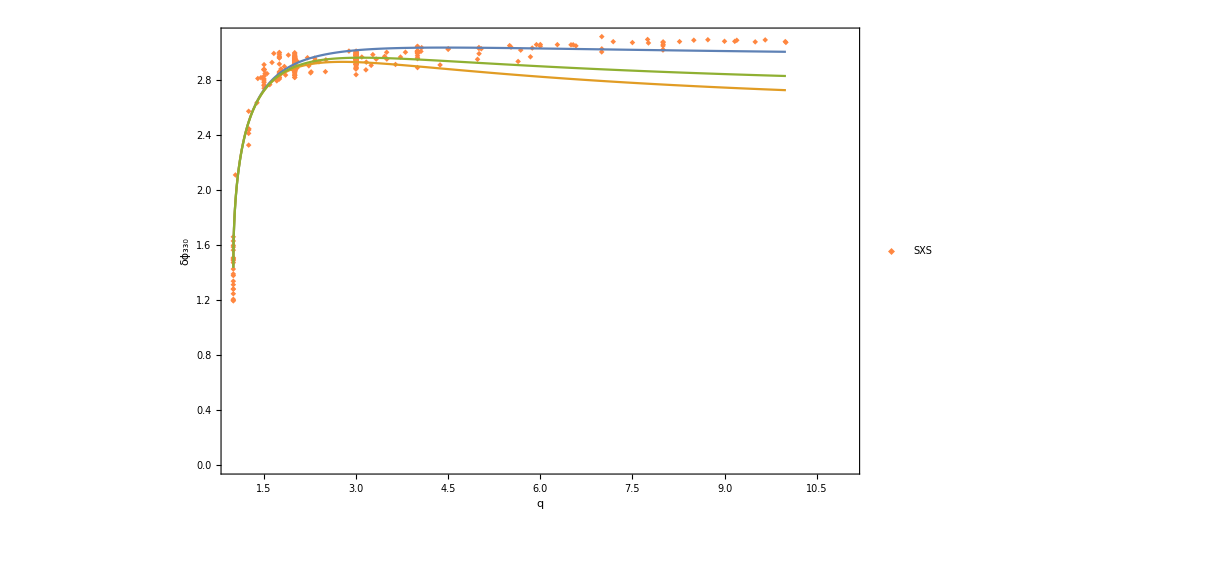

```mathematica
Show[lphse,p1]
```

```mathematica
Export["~/Desktop/RDFits_330/phase_q_33.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_33.pdf

```mathematica
ListPlot[TakeColumn[allampratfinred2,{1,2}]]
ListPlot[TakeColumn[allampratfinred2,{1,3}]]
```

-Graphics-

-Graphics-

### Mode 21

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxs21[[All,1]]/sxs22[[All,1]]}];
geoamprat=Transpose[{geomassratio,geospin,geo21[[All,1]]/geo22[[All,1]]}];
ritamprat=Transpose[{ritmassratio,ritspin,rit21[[All,1]]/rit22[[All,1]]}];
```

```mathematica
sxsamprattest=Transpose[{sxsmassratio,sxsspin,sxs21[[All,1]]/sxs22[[All,1]],sxsspin1,sxsspin2}]/.{xx_,yy_,zz_,tt_}->{Max[xx,1],yy,zz,tt};
```

```mathematica
sxsamprattest=Transpose[{sxsmassratio,sxsspin,sxsmassratio/(1+sxsmassratio)*sxsspin1-1/(1+sxsmassratio)*sxsspin2,sxs21[[All,1]]/sxs22[[All,1]]}]/.{xx_,yy_,zz_,tt_}->{Max[xx,1],yy,zz,tt};
```

```mathematica
{sxsspin1[[1]],sxsspin2[[1]]}
```

{0.500006785023,-0.899703034224999976}

```mathematica
0.5*0.5-0.5*-0.9
```

0.7

```mathematica
sxsouts1=Position[sxsamprat,_?(Abs[#[[1]]-7]<0.1&& #[[3]]≤ 0.2&)];
sxsouts2=Position[sxsamprat,_?(1.2<#[[1]]<2&& #[[3]]≤ 0.1&)];
sxsouts=Join[sxsouts2,sxsouts1]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{137},{140},{142},{143},{144},{145},{146},{147},{148},{150},{151},{152},{153},{155},{156},{160},{163},{164},{165},{166},{167},{168},{169},{171},{174},{175},{176},{177},{178},{180},{181},{182},{185},{187},{188},{193},{194},{196},{197},{198},{199},{200},{209},{211},{212},{215},{216},{218},{219},{221},{224},{227},{228},{229},{231},{233},{236},{238},{240},{246},{248},{249},{250},{254},{255},{256},{259},{261},{262},{266},{267},{268},{269},{270},{272},{274},{278},{280},{284},{470},{477}}

```mathematica
geoouts1=Position[geoamprat,_?(1.1≤ #[[1]]<2&& #[[3]]≤ 0.2&)];
geoouts=Join[geoouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ritouts1=Position[ritamprat,_?(Abs[#[[1]]-5]<0.1&& #[[3]]≤ 0.2&)];
ritouts2=Position[ritamprat,_?(1.2<#[[1]]<2&& #[[3]]≤ 0.1&)];
ritouts3=Position[ritamprat,_?(Abs[#[[1]]-15]<0.1&& #[[3]]≤ 0.2&)];
ritouts4=Position[ritamprat,_?(#[[1]]>16&)];
ritouts=Join[ritouts1,ritouts2,ritouts3,ritouts4];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsampratfin=Delete[sxsamprat,sxsouts];
geoampratfin=Delete[geoamprat,geoouts];
ritampratfin=Delete[ritamprat,ritouts];
```

```mathematica
Arg[0.126902+0.0203152 I]−Arg[-0.0938898−0.0491928I]
```

2.81771

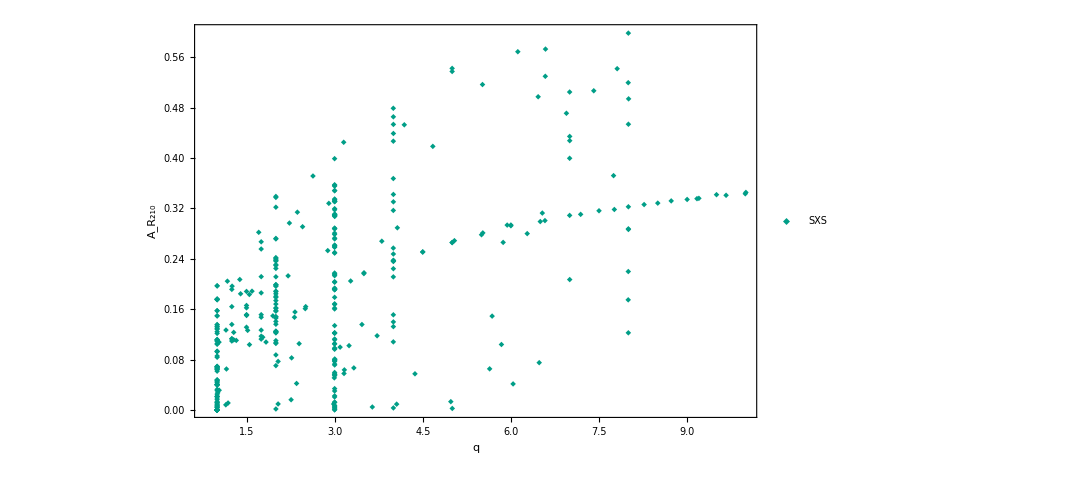

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,3}]},PlotRange->{{0.8,10},{0,0.6}},Frame->True,FrameLabel->{"q","A_R_210"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

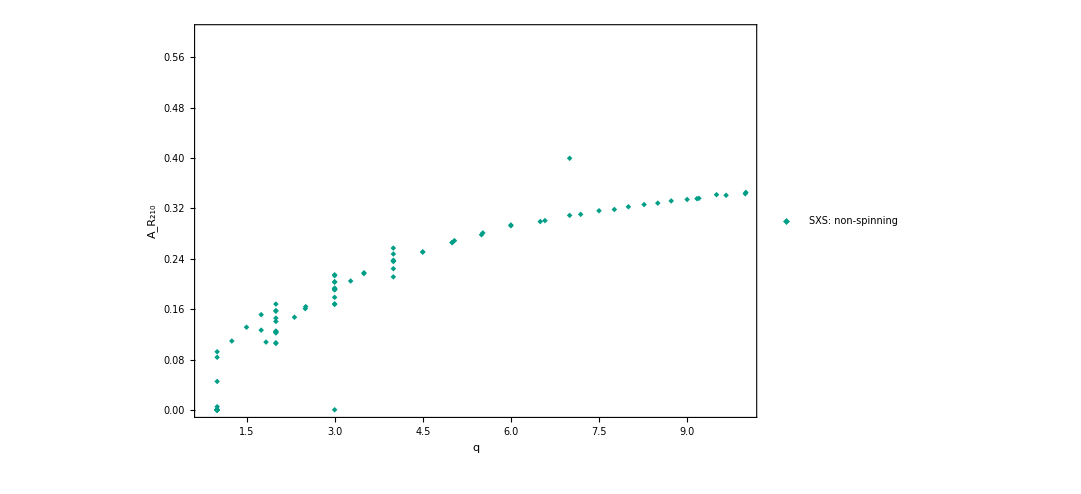

```mathematica
lamp=ListPlot[{TakeColumn[Select[sxsampratfin,Abs[#[[2]]]≤ 0.001&],{1,3}]},PlotRange->{{0.8,10},{0,0.6}},Frame->True,FrameLabel->{"q","A_R_210"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS: non-spinning","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
allampratfin=Join[sxsampratfin];
```

```mathematica
(* Non-spinning *)
ansatz21=((-b0-c0-e0)+b0/qq+c0/qq^2+e0/qq^3)
```

-b0-c0-e0+e0/qq^3+c0/qq^2+b0/qq

```mathematica
nonspindata=Select[sxsamprattest,Abs[#[[2]]]≤ 0.01&];
fitamp21nsp=NonlinearModelFit[nonspindata,ansatz21,{b0,c0,e0,a1,a2},{qq,χ}]
```

FittedModel[0.4873850527290935-(«58»)/qq^3+(«58»)/qq^2-(«58»)/qq]

```mathematica
newspinfitanasatz=Normal[fitamp21nsp]*(1+a1*χ+a2*χ^2)
```

(0.4873850527290935-1.2705904836191763/qq^3+2.3261686100766189/qq^2-1.5429631791865361/qq) (1+a1 χ+a2 χ^2)

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

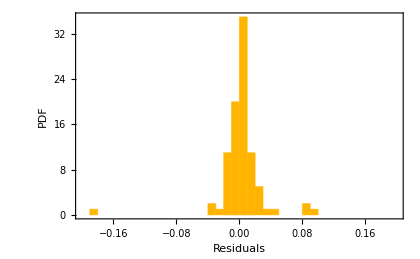

```mathematica
Histogram[fitamp21nsp["FitResiduals"],"PDF",PlotRange->{{-0.2,0.2},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

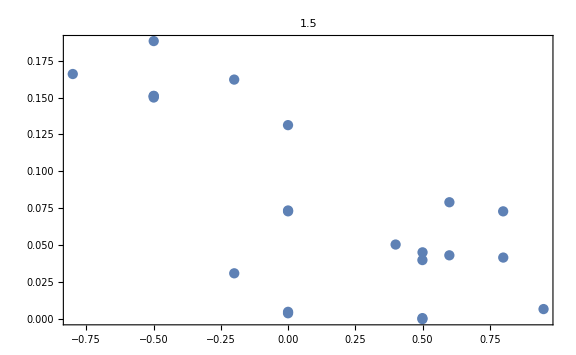

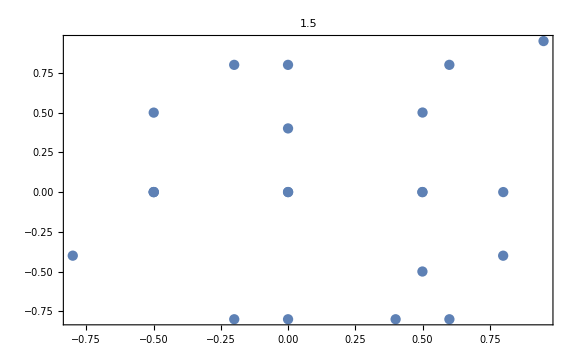

```mathematica
qchoice=1.5;spindata=Select[sxsamprattest,Abs[#[[1]]-qchoice]≤ 0.01&];ListPlot[TakeColumn[spindata,{2,3}],ImageSize->Large,PlotLabel->1.5,Frame->True]
ListPlot[TakeColumn[spindata,{-2,-1}],Frame->True,ImageSize->Large,PlotLabel->1.5]
```

```mathematica
a21ansatz=(a21 χm)+ (a210+b210 qq/(qq+1)^2);
a22ansatz=qq/(qq+1)^2 χp (a22+b22/qq+c22 qq+d22 qq^2)+e22*dm χm + (a220+b220 qq/(qq+1)^2)
```

a220+(b220 qq)/(1+qq)^2+(e22 (1-1/qq) χm)/(1+1/qq)+(qq (a22+b22/qq+c22 qq+d22 qq^2) χp)/(1+qq)^2

```mathematica
a21ampansatz=a21ansatz/a22ansatz
```

(a210+(b210 qq)/(1+qq)^2+a21 χm)/(a220+(b220 qq)/(1+qq)^2+(e22 (1-1/qq) χm)/(1+1/qq)+(qq (a22+b22/qq+c22 qq+d22 qq^2) χp)/(1+qq)^2)

```mathematica
sxsamprattest[[1]]
```

{1,0.500006785023,0.699871581339874169,0.157590850113623032}

```mathematica
a21ampansatz/.a21->1/.a22->1/.e22->1/.c22->1/.b22->1/.d22->1
```

χm/(((1-1/qq) χm)/(1+1/qq)+(qq (1+1/qq+qq+qq^2) χp)/(1+qq)^2)

```mathematica
Length@sxsamprattest
```

506

```mathematica
sxsamprattest
```

```mathematica
fitamp21=NonlinearModelFit[sxsamprattest,a21ampansatz,{a21,a210,b210,a220,b220,a22,e22,c22,b22,d22},{qq,χp,χm},MaxIterations->10000]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

FittedModel[(«1»)/(-0.969476494+(«40» qq)/(1+qq)^2+(«39» (1-1/(«2»)) χm)/(1+1/qq)+(qq («1») χp)/(1+qq)^2)]

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

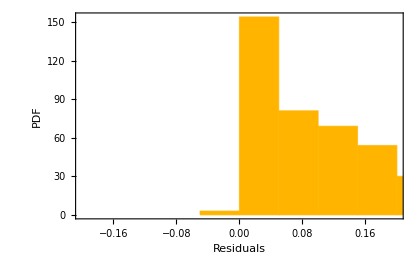

```mathematica
h1=Histogram[fitamp21["FitResiduals"],"PDF",PlotRange->{{-0.2,0.2},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

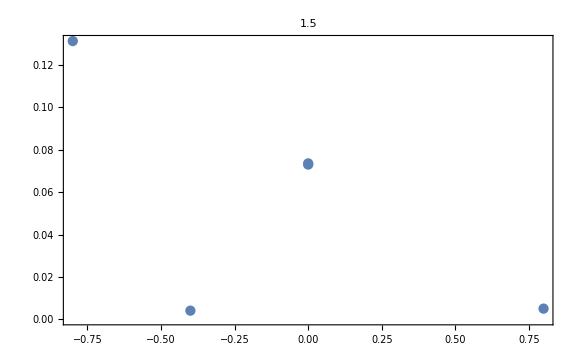

```mathematica
(*select q=1.5 and χeff=0 *)
qchoice=1.5;χeffch=0;spindata=Select[sxsamprattest,Abs[#[[1]]-qchoice]≤ 0.01&&Abs[#[[2]]-χeffch]≤ 0.01&];ListPlot[TakeColumn[spindata,{-2,-1,3}]/.{xx_,yy_,zz_}->{xx-yy,zz},ImageSize->Large,PlotLabel->1.5,Frame->True]
```

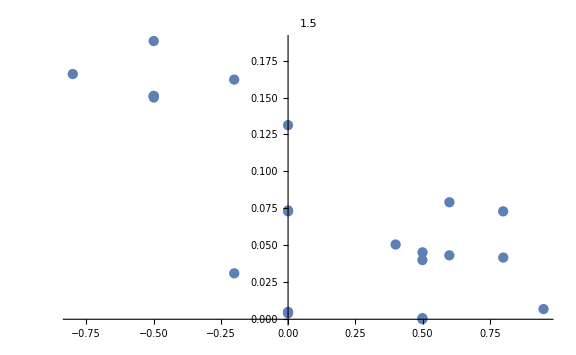
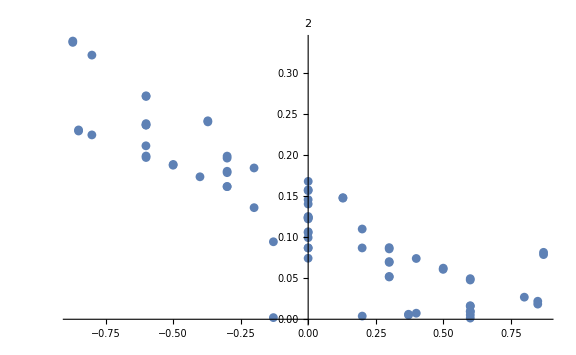
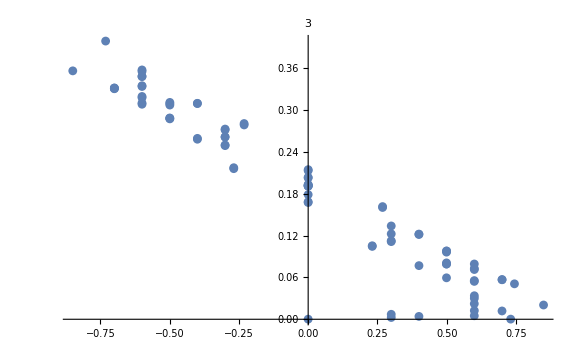
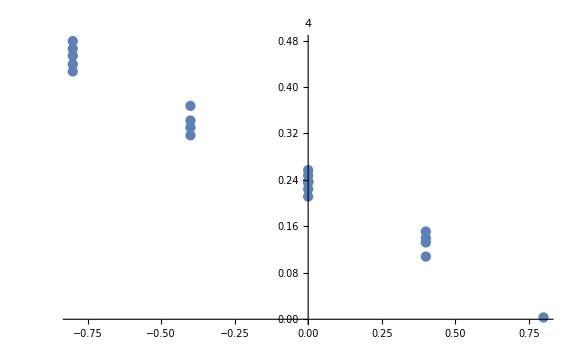
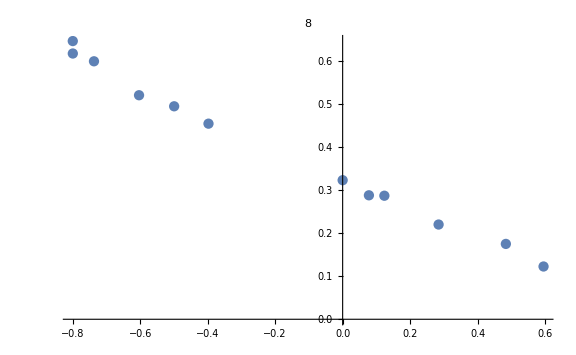

```mathematica
Table[qchoice=i;spindata=Select[sxsamprattest,Abs[#[[1]]-qchoice]≤ 0.01&];ListPlot[TakeColumn[spindata,{2,3}],ImageSize->Large,PlotLabel->i],{i,{1.5,2,3,4,8}}]
```

```mathematica
ansatz21=((-b0-c0-e0)+b0/qq+c0/qq^2+e0/qq^3)*(1+a1*χ+a2*χ^2)
```

(-b0-c0-e0+e0/qq^3+c0/qq^2+b0/qq) (1+a1 χ+a2 χ^2)

```mathematica
fitamp21=NonlinearModelFit[allampratfin,ansatz21,{b0,c0,e0,a1,a2},{qq,χ}]
```

FittedModel[(0.4574615244803286-(«59»)/qq^3+(«59»)/qq^2-1.3297367917806983/qq) (1-«57» χ+0.052209474439428232 χ^2)]

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

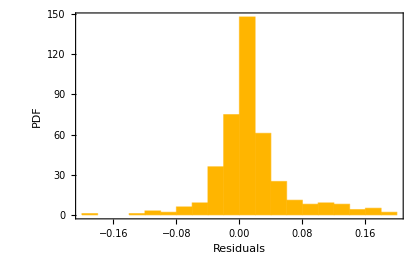

```mathematica
h1=Histogram[fitamp21["FitResiduals"],"PDF",PlotRange->{{-0.2,0.2},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

```mathematica
μA=Mean[fitamp21["FitResiduals"]]
σA=StandardDeviation[fitamp21["FitResiduals"]]
```

0.014005706038966

0.0471734760248733

```mathematica
Outliers=Position[fitamp33["FitResiduals"],_?(Abs[#]≥ 2*σA&)]
```

{{5},{32},{33}}

```mathematica
fitamp21=NonlinearModelFit[Delete[allampratfin,Outliers],ansatz21,{b0,c0,e0,a1,a2},{qq,χ}]
```

FittedModel[(0.4574637757358474-(«59»)/qq^3+(«59»)/qq^2-1.3297553912005843/qq) (1-«59» χ+0.0522081574020079 χ^2)]

```mathematica
fitamp21n=Normal[fitamp21]
```

(0.4574637757358474-1.0106434351645465/qq^3+1.8829350506292833/qq^2-1.3297553912005843/qq) (1-1.1688284951034061 χ+0.0522081574020079 χ^2)

```mathematica
amp210[qq_,χ_]:=(0.45746377573584738067411125693825617113`16.898355111814006-(1.01064343516454645097743379363259035165`17.863653817723527)/qq^3+(1.88293505062928333162239049163548827711`17.863653817723527)/qq^2-(1.3297553912005842613190679549411540966`17.863653817723527)/qq) (1-1.16882849510340612498211745374793744661`17.863653817723527 χ+0.05220815740200789961863683972429615218`17.863653817723527 χ^2);
```

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

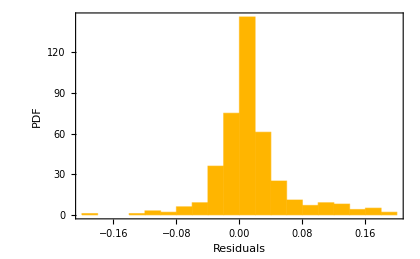

```mathematica
h1=Histogram[fitamp21["FitResiduals"],"PDF",PlotRange->{{-0.2,0.2},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

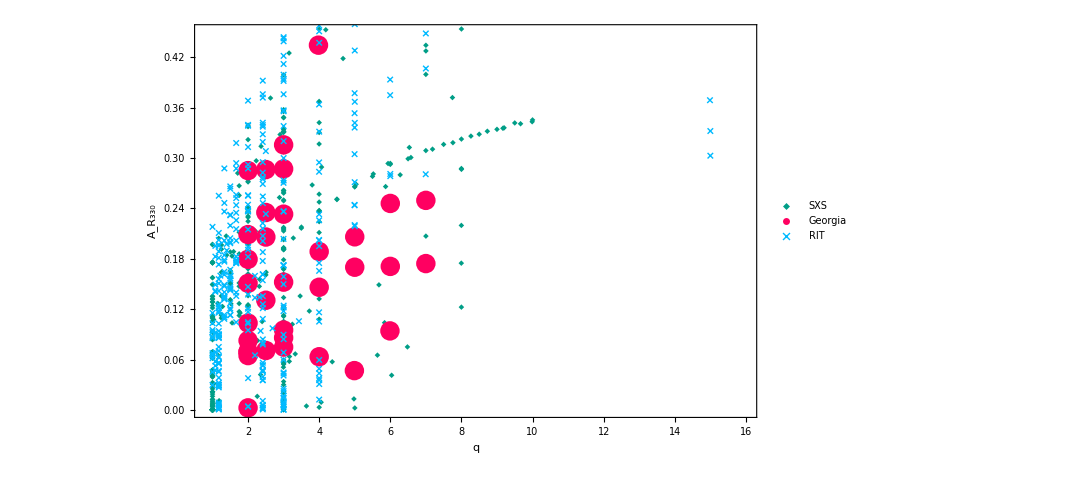

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,3}],TakeColumn[geoampratfin,{1,3}],TakeColumn[ritampratfin,{1,3}]},PlotRange->{{0.8,16},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_210"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{11.3,0.14}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_21.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_21.pdf

```mathematica
(* Phase remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,Mod[sxs21[[All,2]]-1/2(sxs22[[All,2]]),π]}];
geophdiff=Transpose[{geomassratio,geospin,Mod[-1/2(geo22[[All,2]]-π)-geo21[[All,2]],π]}];
ritphdiff=Transpose[{ritmassratio,ritspin,Mod[1/2(rit22[[All,2]]-π)-rit21[[All,2]],π]}];
```

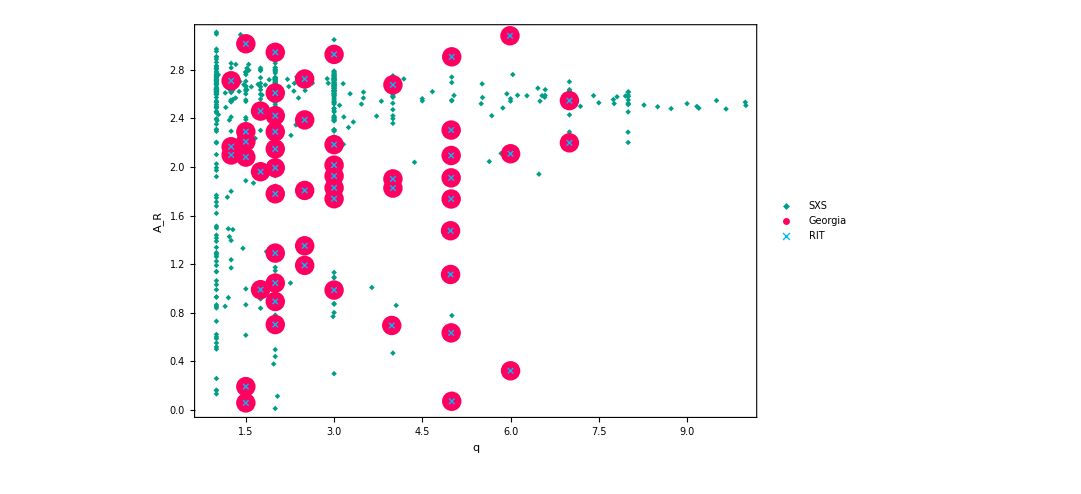

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,3}],TakeColumn[geophdiff,{1,3}],TakeColumn[geophdiff,{1,3}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

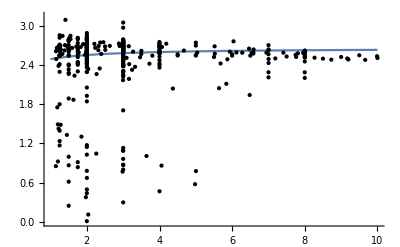

```mathematica
(* Comparison between the Cotesta et al. phase difference and ours. Notice that they fit at the peak of the 22 which adds a difference of 0.2 rads. *)
Plot[Mod[seobnrfits21[q,0]+0.2,π],{q,1,10},PlotRange->{All,{0,π}},Epilog->{Point[Select[TakeColumn[sxsphdiff,{1,3}],#[[1]]>1.1&]]}]
```

```mathematica
sxsouts1=Position[sxsphdiff,_?(#[[3]]≤   2.1&)];
sxsouts=Join[sxsouts1];
```

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification 0.999833170061147247⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
geoouts=Position[geophdiff,_?(#[[1]]≤   1.1&)]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.25⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
ritouts1=Position[ritphdiff,_?(#[[1]]≤    1.1&)];
ritouts=Join[ritouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsphdifffin=Delete[sxsphdiff,sxsouts];
(*geophdifffin=Select[Delete[geophdiff,geoouts],#[[-1]]≥ 2&];
ritphdifffin=Select[Delete[ritphdiff,ritouts],#[[-1]]≥ 2&];*)
```

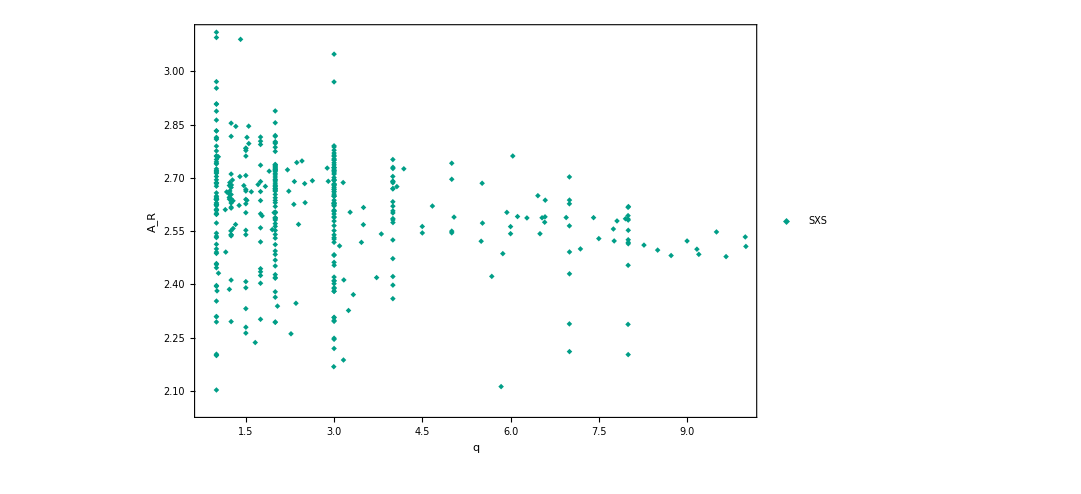

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdifffin,{1,3}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,PlotRange->All,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,26],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",3},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.75,0.85}]]
```

```mathematica
allphdifffin=Join[sxsphdifffin];
```

```mathematica
ansatz21ph
```

```mathematica
dm=(1-1/qq)/(1+1/qq);
ansatz21ph=a+b dm+c χ+dm^2(d+e χ+f χ^2)
```

a+(b (1-1/qq))/(1+1/qq)+c χ+((1-1/qq)^2 (d+e χ+f χ^2))/(1+1/qq)^2

```mathematica
allphdifffin=allphdifffin/.{qq_,tt_,yy_}->{Max[qq,1],tt,yy};
```

```mathematica
fitph21=NonlinearModelFit[allphdifffin,ansatz21ph,{a,b,c,d,e,f},{qq,χ}]
```

FittedModel[2.6241524376151859+(«44» (1-«1»))/(1+1/qq)-«44» χ+((1-1/qq)^2 (-«44»-«43» χ-«44» χ^2))/(1+1/qq)^2]

```mathematica
Normal[fitph21]
```

2.6241524376151859+(0.0852858672683861527 (1-1/qq))/(1+1/qq)-0.131825959709443112 χ+((1-1/qq)^2 (-0.283021354909504641-0.336847740513591036 χ-0.34615406893466491 χ^2))/(1+1/qq)^2

```mathematica
phasediff210[qq_,χ_]:=2.62415243761518590+(0.08528586726838615266375558023495104993`18. (1-1/qq))/(1+1/qq)-0.13182595970944311198427549430058266459`18. χ+1/(1+1/qq)^2(1-1/qq)^2 (-0.28302135490950464115782635802087315938`18.-0.3368477405135910358870567768626781895`18. χ-0.34615406893466491025129545813081747914`18. χ^2)
```

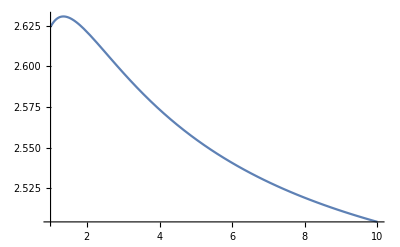

```mathematica
Plot[phasediff210[qq,0],{qq,1,10}]
```

```mathematica
μϕ=Mean[fitph33["FitResiduals"]]
σϕ=StandardDeviation[fitph33["FitResiduals"]]
```

0.+0. ⅈ

0.127864445819469

```mathematica
h1=Histogram[Select[fitph33["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

-Graphics-

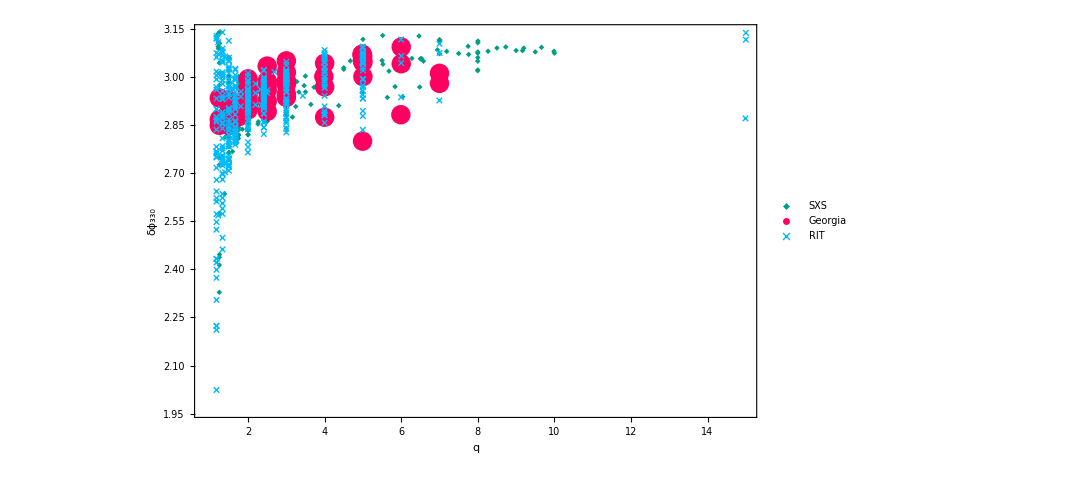

```mathematica
lphse=ListPlot[{Delete[TakeColumn[sxsphdifffin,{1,3}],331],TakeColumn[geophdifffin,{1,3}],TakeColumn[ritphdifffin,{1,3}]},Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->All,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{10.3,2.35}]]
```

```mathematica
Export["~/Desktop/RDFits_330/phase_q_33.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_33.pdf

### Mode 21 new ansatz with χa

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxsspina,sxs21[[All,1]]/sxs22[[All,1]]}];
geoamprat=Transpose[{geomassratio,geospin,geospina,geo21[[All,1]]/geo22[[All,1]]}];
ritamprat=Transpose[{ritmassratio,ritspin,ritspina,rit21[[All,1]]/rit22[[All,1]]}];
```

```mathematica
sxsouts1=Position[sxsamprat,_?(Abs[#[[1]]-7]<0.1&& #[[4]]≤ 0.2&)];
sxsouts2=Position[sxsamprat,_?(1.2<#[[1]]<2&& #[[4]]≤ 0.1&)];
sxsouts=Join[sxsouts2,sxsouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
geoouts1=Position[geoamprat,_?(1.1≤ #[[1]]<2&& #[[4]]≤ 0.2&)];
geoouts=Join[geoouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ritouts1=Position[ritamprat,_?(Abs[#[[1]]-5]<0.1&& #[[4]]≤ 0.2&)];
ritouts2=Position[ritamprat,_?(1.2<#[[1]]<2&& #[[4]]≤ 0.1&)];
ritouts3=Position[ritamprat,_?(Abs[#[[1]]-15]<0.1&& #[[4]]≤ 0.2&)];
ritouts4=Position[ritamprat,_?(#[[1]]>16&)];
ritouts=Join[ritouts1,ritouts2,ritouts3,ritouts4];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsampratfin=Delete[sxsamprat,sxsouts];
geoampratfin=Delete[geoamprat,geoouts];
ritampratfin=Delete[ritamprat,ritouts];
```

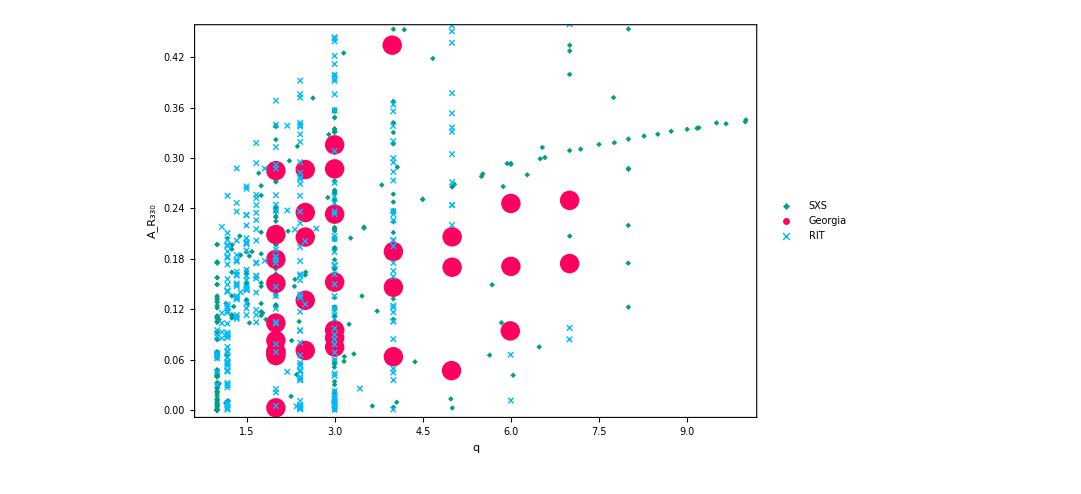

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}],TakeColumn[geoampratfin,{1,4}],TakeColumn[ritampratfin,{1,4}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
allampratfin=Join[sxsampratfin,geoampratfin];
```

```mathematica
npdata=Select[allampratfin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
ν=qq/(qq+1)^2
```

qq/(1+qq)^2

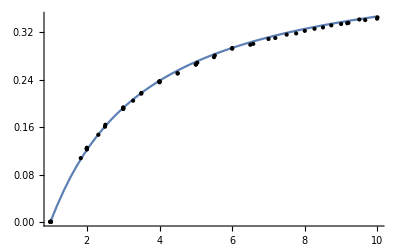

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

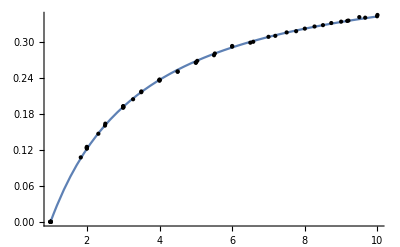

```mathematica
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
npdata2=Delete[npdata,outliers];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
allampratfinred=Complement[allampratfin,npdata];
fitamp21new=NonlinearModelFit[allampratfinred,nspansatz+b0(χa+Sqrt[1-4 ν]χs),{b0},{qq,χs,χa},MaxIterations->1000]
```

FittedModel[0.50018102508136526 √(1-(4 qq)/(1+qq)^2)+0.088290343313539563 (1-(4 qq)/(«1»)^2)-«59» (1-«1»)^(3/2)-(0.17362+5.69694×10^-17 ⅈ) (χa+√(1-(4 qq)/(1+qq)^2) χs)]

```mathematica
μA=Mean[fitamp21new["FitResiduals"]]
σA=StandardDeviation[fitamp21new["FitResiduals"]]
```

-0.0150963-8.46574×10^-11 ⅈ

0.066772

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

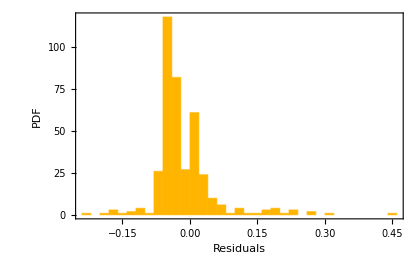

```mathematica
h1=Histogram[Chop[fitamp21new["FitResiduals"]],"PDF",ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

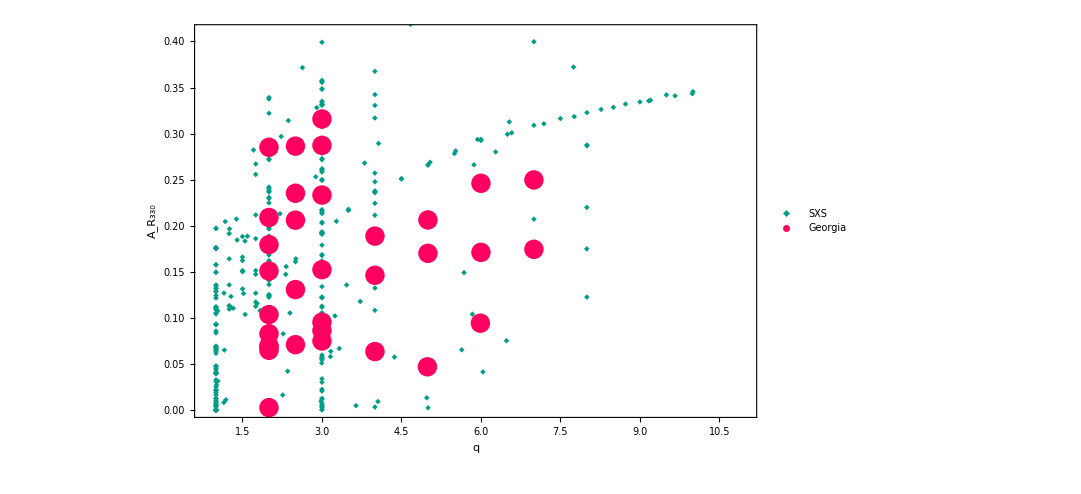

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}],TakeColumn[geoampratfin,{1,4}]},PlotRange->{{0.8,11},{0,0.41}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{7.3,0.13}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_21.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_21.pdf

```mathematica
(* Amplitude remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,sxsspina,Mod[1/2(sxs22[[All,2]])-sxs21[[All,2]],π]}];
geophdiff=Transpose[{geomassratio,geospin,geospina,Mod[1/2(geo22[[All,2]]-π)-geo21[[All,2]],π]}];
ritphdiff=Transpose[{ritmassratio,ritspin,ritspina,Mod[1/2(rit22[[All,2]]-π)-rit21[[All,2]],π]}];
```

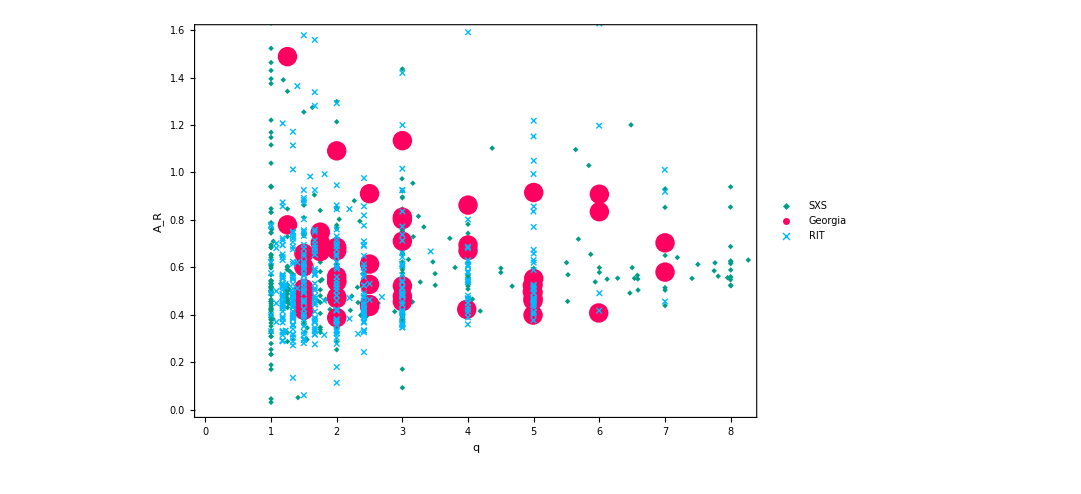

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,4}],TakeColumn[geophdiff,{1,4}],TakeColumn[ritphdiff,{1,4}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
sxsouts1=Position[sxsphdiff,_?(#[[1]]≤ 1.3&)];
sxsouts=Join[sxsouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
geoouts=Position[geophdiff,_?(#[[1]]≤ 1.3&)]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.25⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{1},{2},{3}}

```mathematica
ritouts1=Position[ritphdiff,_?(#[[1]]≤ 1.3&)];
ritouts=Join[ritouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsphdifffin=Select[Delete[sxsphdiff,sxsouts],#[[-1]]≤ 2&];
geophdifffin=Select[Delete[geophdiff,geoouts],#[[-1]]≤ 2&];
ritphdifffin=Select[Delete[ritphdiff,ritouts],#[[-1]]≤ 2&];
```

```mathematica
allphdifffin=Join[sxsphdifffin,geophdifffin];
```

```mathematica
dm=(1-1/qq)/(1+1/qq);
χ=χs+χa*dm/(1-2ν)
ansatz21ph=a+b*Sqrt[(dm)]+c*dm+d*χ+dm^2*(e+f*χ)*χ;
```

((1-1/qq) χa)/((1+1/qq) (1-(2 qq)/(1+qq)^2))+χs

```mathematica
fitph21=NonlinearModelFit[allphdifffin,ansatz21ph,{a,b,c,d,e,f},{qq,χs,χa}]
```

FittedModel[0.762646-0.567335 √((1-1/qq)/(1+1/qq))+(«18» («1»))/(1+1/qq)+0.258314 (((1-1/qq) χa)/((1+1/qq) (1-(«1»)/(«1»)))+χs)+((1-1/qq)^2 (((«1») «2»)/((«1») «1»)+χs) (-0.228956+0.127529 (((1-1/qq) χa)/((1+1/qq) (1-«1»))+χs)))/(1+1/qq)^2]

```mathematica
μϕ=Mean[fitph21["FitResiduals"]]
σϕ=StandardDeviation[fitph21["FitResiduals"]]
```

5.34843×10^-16

0.183743

```mathematica
h1=Histogram[Select[fitph33["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

-Graphics-

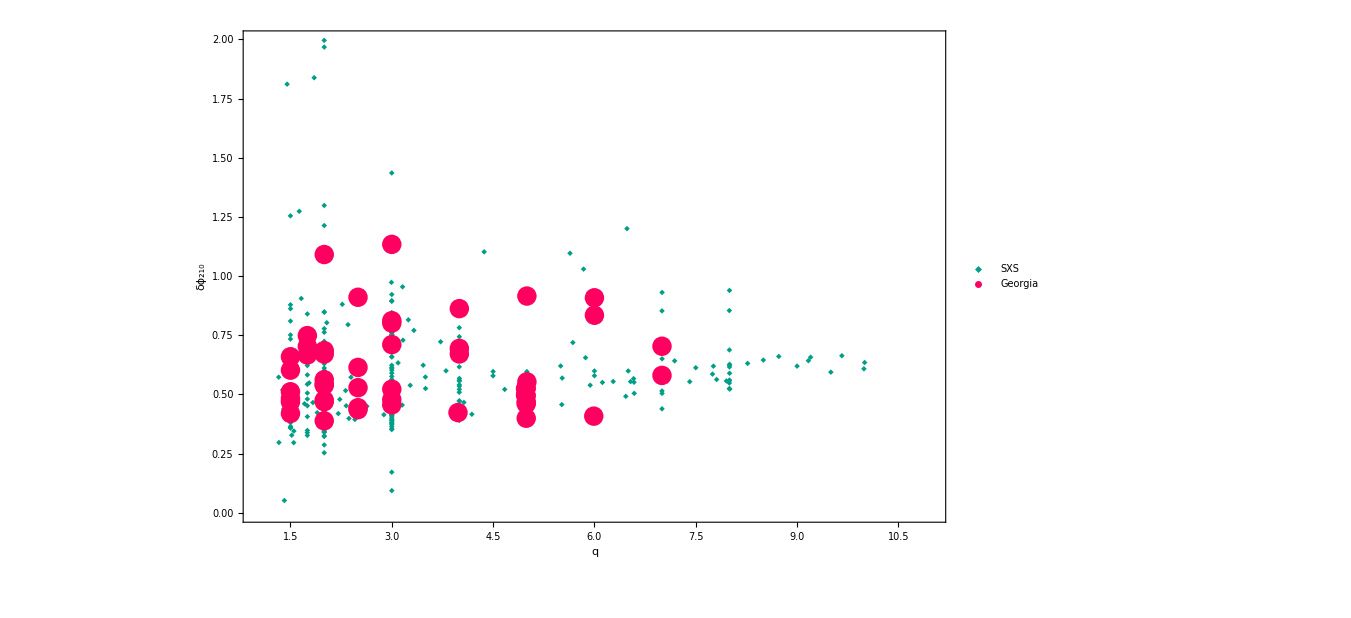

```mathematica
lphse=ListPlot[{TakeColumn[sxsphdifffin,{1,4}],TakeColumn[geophdifffin,{1,4}]},Frame->True,FrameLabel->{"q","δϕ_210"},Frame->True,PlotRange->{{1,11},All},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->1000,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.9}],Epilog->Inset[h1,{8.5,1.55}]]
```

```mathematica
Export["~/Desktop/RDFits_330/phase_q_21.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_21.pdf

### Mode 21 new ansatz with χa just SXS

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxsspina,sxs21[[All,1]]/sxs22[[All,1]]}];
```

```mathematica
sxsampratfin=sxsamprat;
```

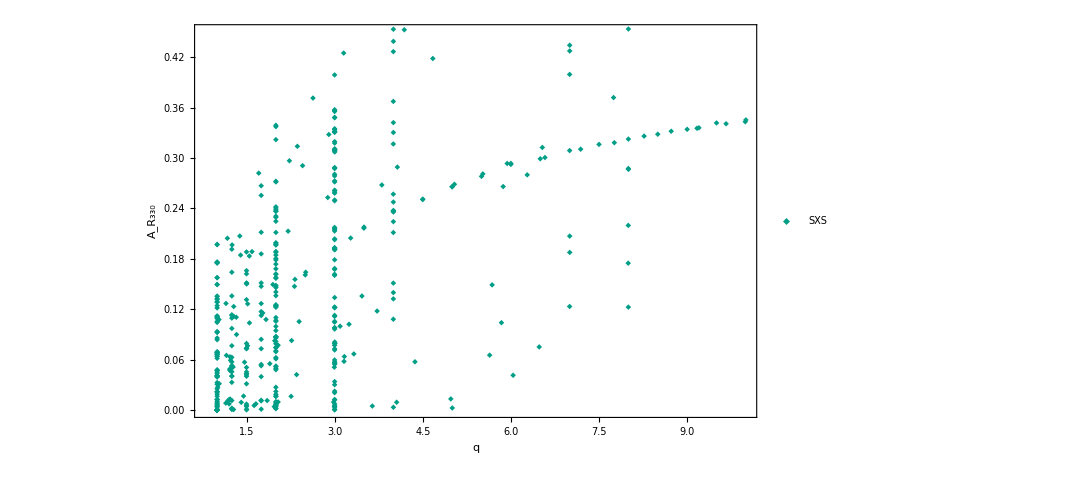

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
(* Fit first non-spinning data *)
allampratfin=Join[sxsampratfin];
npdata=Select[allampratfin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
ν=qq/(qq+1)^2
```

qq/(1+qq)^2

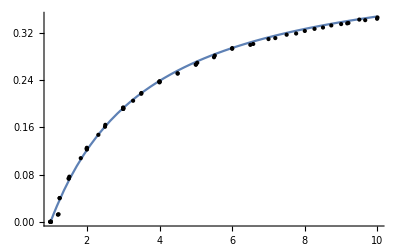

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

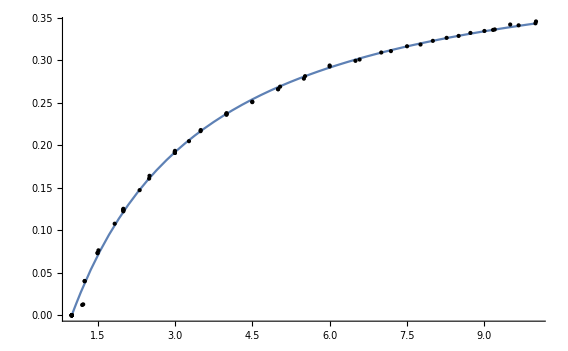

```mathematica
(* Eliminate outliers *)
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 3st&)];
npdata2=Delete[npdata,outliers];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
(* Fit the equal-massratio, unequal spin data. *)
allampratfinred=Complement[allampratfin,npdata];
fitamp21new=NonlinearModelFit[allampratfinred,Normal[nspfit]+b0(χa+Sqrt[1-4ν]χs),{b0,b1,b2},{qq,χs,χa},MaxIterations->1000]
μA=Mean[fitamp21new["FitResiduals"]]
σA=StandardDeviation[fitamp21new["FitResiduals"]]
```

FittedModel[0.32733253360968254 √(1-(4 qq)/(1+qq)^2)+0.11268426934797012 (1-(4 qq)/(((«1»«1»)^2))-0.166341397 (χa+√(1-(4 qq)/(1+qq)^2) χs)]

0.0177

0.054

```mathematica
(* Outlier hunter *)
outliers=Position[fitamp21new["FitResiduals"],_?(Abs[#]≥ 4st&)]
allampratfinred2=Delete[allampratfinred,outliers];
fitamp21newfinal=NonlinearModelFit[allampratfinred2,Normal[nspfit]+b0(χa+Sqrt[1-4ν]χs),{b0,b1},{qq,χs,χa}];
μA=Mean[fitamp21newfinal["FitResiduals"]]
σA=StandardDeviation[fitamp21newfinal["FitResiduals"]]
```

{{11},{13},{18},{20},{22},{24},{25},{28},{29},{30},{35},{62},{63},{67},{72},{75},{81},{83},{86},{87},{89},{94},{98},{100},{101},{103},{105},{108},{109},{112},{113},{114},{115},{116},{117},{118},{119},{121},{128},{130},{131},{135},{136},{139},{141},{153},{155},{158},{160},{163},{164},{179},{192},{196},{208},{209},{228},{257},{277},{284},{310},{320},{343},{349},{356},{359},{390},{394},{399},{400},{402},{403},{410},{416},{427},{429},{430},{434}}

0.00311

0.00982

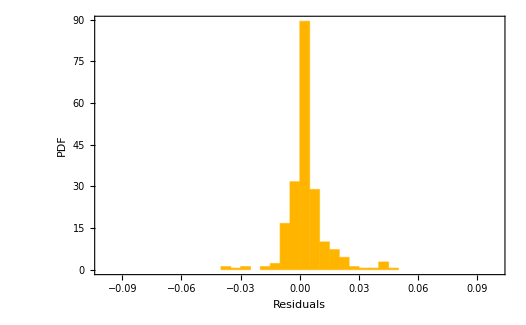

```mathematica
h1=Histogram[Chop[fitamp21newfinal["FitResiduals"]],20,"PDF",PlotRange->{{-0.1,0.1},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

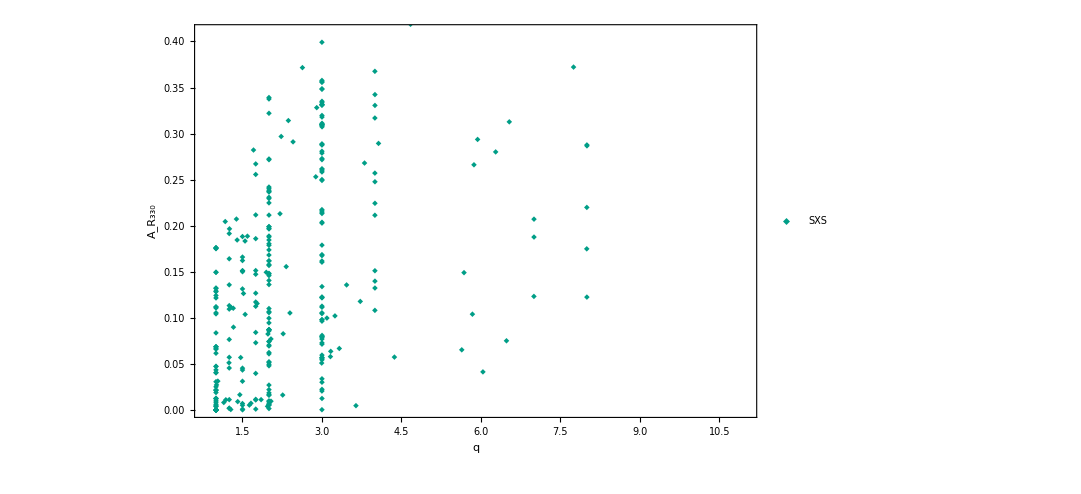

```mathematica
lamp=ListPlot[{TakeColumn[allampratfinred2,{1,4}]},PlotRange->{{0.8,11},{0,0.41}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{7.3,0.13}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_21.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_21.pdf

```mathematica
(* Amplitude remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,sxsspina,Mod[1/2(sxs22[[All,2]])-sxs21[[All,2]],π]}];
```

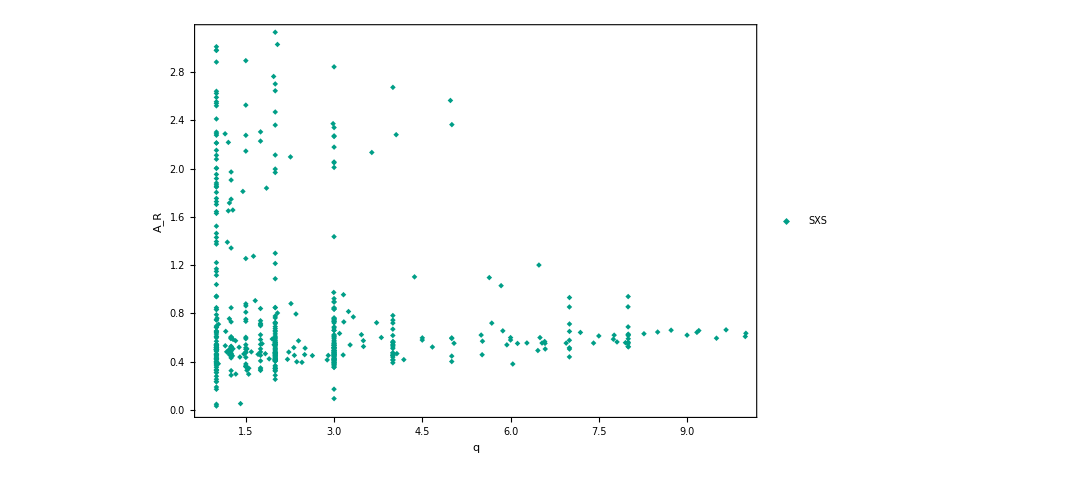

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,4}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

```mathematica
ansatz21ph=a+b*dm+d*χ+dm^2*(e+f*χ+c χ^2);
ansatz21phnsp=ansatz21ph/.χa->0/.χs->0
```

a+(e (1-1/qq)^2)/(1+1/qq)^2+(b (1-1/qq))/(1+1/qq)

```mathematica
(* Fit first non-spinning data *)
sxsphdifffin=Join[sxsphdiff];
npdata=Select[sxsphdifffin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
ν=qq/(qq+1)^2
```

qq/(1+qq)^2

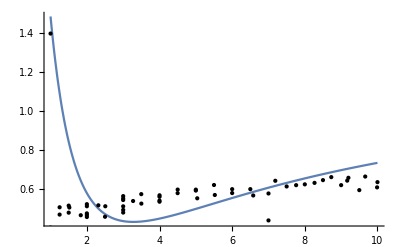

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,4}]],ansatz21phnsp,{a,b,e},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
EradUIB2017[η,χ1,χ2]
```

-0.0980373 (1-4 η)^0.5 (1-3.22837 η) η^2 (χ1-χ2)+0.0111853 η^3 (χ1-χ2)^2-(0.0197824 (1-4.91668 η) (1-4 η)^0.5 η (χ1-χ2) (1/4 (1+√(1-4 η))^2 χ1+1/4 (1-√(1-4 η))^2 χ2))/(1/4 (1-√(1-4 η))^2+1/4 (1+√(1-4 η))^2)+(((1-(2 √2)/3) η+0.56099 η^2-0.846676 η^3+3.14515 η^4) (1+((-0.130844-1.13873 η+5.49074 η^2) (1/4 (1+√(1-4 η))^2 χ1+1/4 (1-√(1-4 η))^2 χ2))/(1/4 (1-√(1-4 η))^2+1/4 (1+√(1-4 η))^2)+((-0.177628+2.17667 η^2) (1/4 (1+√(1-4 η))^2 χ1+1/4 (1-√(1-4 η))^2 χ2)^2)/((1/4 (1-√(1-4 η))^2+1/4 (1+√(1-4 η))^2)^2)+((-0.632019+4.9527 η-10.0237 η^2) (1/4 (1+√(1-4 η))^2 χ1+1/4 (1-√(1-4 η))^2 χ2)^3)/((1/4 (1-√(1-4 η))^2+1/4 (1+√(1-4 η))^2)^3)))/(1+((-0.991948+0.36762 η+4.27457 η^2) (1/4 (1+√(1-4 η))^2 χ1+1/4 (1-√(1-4 η))^2 χ2))/(1/4 (1-√(1-4 η))^2+1/4 (1+√(1-4 η))^2))

Part::partd: Part specification List⟦-1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

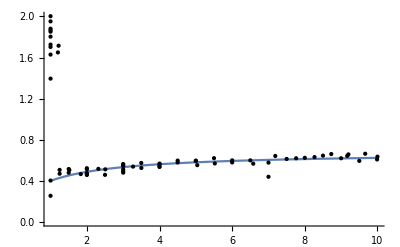

```mathematica
(* Eliminate outliers *)
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
outliers2=Position[npdata,_?(#[[-1]]≥ 1&)];
outliers=Join[outliers,outliers2];
npdata2=Delete[npdata,outliers2];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],ansatz21phnsp,{a,b,e},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->{All,{0,2}},Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
allampratfinred=Complement[allampratfin,npdata2];
χ=χs+χa dm/(1-1.3ν)
dm=(1-1/qq)/(1+1/qq);
ansatz21ph=a+b*dm+d*χ+dm^2*(e+f*χ+c χ^2);
fitph21=NonlinearModelFit[allampratfinred,ansatz21ph,{a,b,c,d,e,f},{qq,χs,χa}]
```

((1-1/qq) χa)/((1+1/qq) (1-(1.3 qq)/(1+qq)^2))+χs

FittedModel[0.0488114+(0.151008 (1-1/qq))/(1+1/qq)-0.0651241 (((1-1/qq) χa)/((1+1/qq) (1-(«1»)/(«1»)))+χs)+((1-1/qq)^2 (0.25364-0.2774 («1»+χs)-0.000255604 («1»+χs)^2))/(1+1/qq)^2]

```mathematica
μϕ=Mean[fitph21["FitResiduals"]]
σϕ=StandardDeviation[fitph21["FitResiduals"]]
```

9.08364×10^-17

0.0440504

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

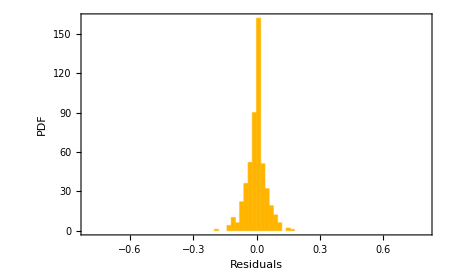

```mathematica
h1=Histogram[Select[fitph21["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

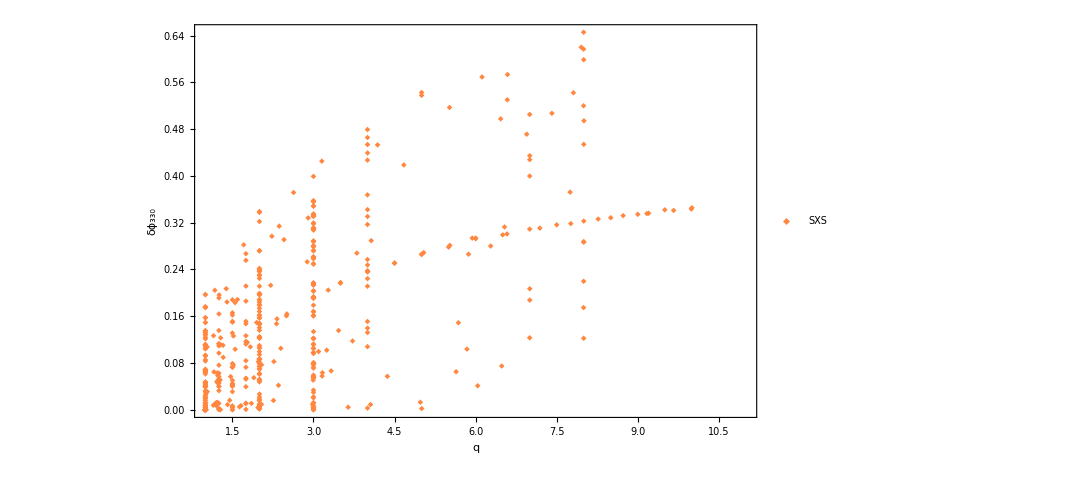

```mathematica
lphse=ListPlot[TakeColumn[allampratfinred,{1,-1}],Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->{{1,11},All},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{7.452,2.55}]]
```

```mathematica
Export["~/Desktop/RDFits_330/phase_q_21.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_21.pdf

```mathematica
Clear[fit21phase]
```

```mathematica
fit21phase[1,2,0]
```

-0.0814368

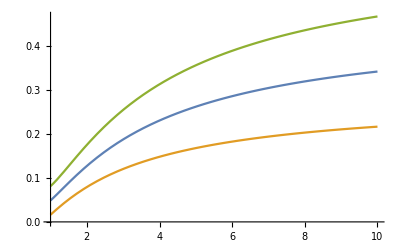

```mathematica
fit21phase[qq_,χs_,χa_]:=Evaluate[Normal[fitph21]]
Plot[{fit21phase[qq,0,0],fit21phase[qq,0.5,0],fit21phase[qq,-0.5,0]},{qq,1,10}]
```

```mathematica
fit21phasefun=
```

### Mode 44

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxs44[[All,1]]/sxs22[[All,1]]}];
geoamprat=Transpose[{geomassratio,geospin,geo44[[All,1]]/geo22[[All,1]]}];
ritamprat=Transpose[{ritmassratio,ritspin,rit44[[All,1]]/rit22[[All,1]]}];
```

```mathematica
sxsouts1=Position[sxsamprat,_?(Abs[#[[1]]-7]<0.1&& #[[3]]≤ 0.2&)];
sxsouts2=Position[sxsamprat,_?(1.2<#[[1]]<2&& #[[3]]≤ 0.1&)];
sxsouts=Join[sxsouts2,sxsouts1]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{167},{168},{169},{170},{171},{172},{173},{174},{175},{176},{177},{178},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192},{193},{194},{195},{196},{197},{198},{199},{200},{201},{202},{203},{204},{205},{206},{207},{208},{209},{210},{211},{212},{213},{214},{215},{216},{217},{218},{219},{220},{221},{222},{223},{224},{225},{226},{227},{228},{229},{230},{231},{232},{233},{234},{235},{236},{237},{238},{239},{240},{241},{242},{243},{244},{245},{246},{247},{248},{249},{250},{251},{252},{253},{254},{255},{256},{257},{258},{259},{260},{261},{262},{263},{264},{265},{266},{267},{268},{269},{270},{271},{272},{273},{274},{275},{276},{277},{278},{279},{280},{281},{282},{283},{284},{469},{470},{471},{472},{473},{474},{475},{476},{477}}

```mathematica
geoouts1=Position[geoamprat,_?(1.1≤ #[[1]]<2&& #[[3]]≤ 0.2&)];
geoouts=Join[geoouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ritouts1=Position[ritamprat,_?(Abs[#[[1]]-5]<0.1&& #[[3]]≤ 0.2&)];
ritouts2=Position[ritamprat,_?(1.2<#[[1]]<2&& #[[3]]≤ 0.1&)];
ritouts3=Position[ritamprat,_?(Abs[#[[1]]-15]<0.1&& #[[3]]≤ 0.2&)];
ritouts4=Position[ritamprat,_?(#[[1]]>16&)];
ritouts=Join[ritouts1,ritouts2,ritouts3,ritouts4];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsampratfin=Delete[sxsamprat,sxsouts];
geoampratfin=Delete[geoamprat,geoouts];
ritampratfin=Delete[ritamprat,ritouts];
```

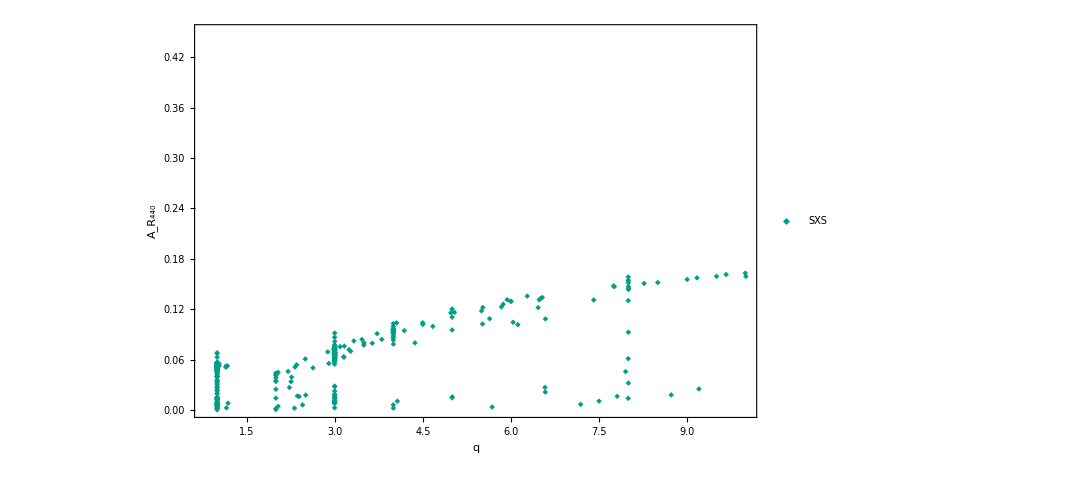

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,3}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_440"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

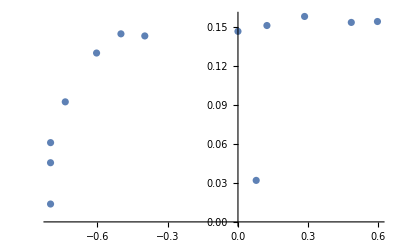

```mathematica
myq=8;ListPlot[TakeColumn[Select[sxsampratfin,Abs[#[[1]]-myq]≤0.05&],{2,3}],PlotRange->All]
```

```mathematica
allampratfin=Join[sxsampratfin,geoampratfin,ritampratfin];
allampratfin=Join[sxsampratfin];
```

```mathematica
ansatz44=((a0)+b0/qq+c0/qq^2+e0/qq^3)*(1+a1*χ+a2*χ^2)
```

(a0+e0/qq^3+c0/qq^2+b0/qq) (1+a1 χ+a2 χ^2)

```mathematica
fitamp44=NonlinearModelFit[allampratfin,ansatz44,{a0,b0,c0,e0,a1,a2},{qq,χ}]
```

FittedModel[(0.16566234677705737+(«59»)/qq^3+(«59»)/qq^2-(«59»)/qq) (1+«59» χ-«59» χ^2)]

```mathematica
Normal[fitamp44]
```

(0.16566234677705737+0.019913202766710661/qq^3+0.2603777242771106/qq^2-0.4057594054146807/qq) (1+0.064073151490941508 χ-0.16000691178765014 χ^2)

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

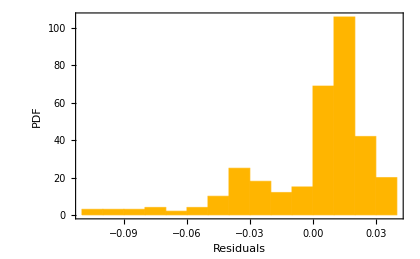

```mathematica
h1=Histogram[fitamp44["FitResiduals"],"PDF",PlotRange->{All,All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

```mathematica
μA=Mean[fitamp33["FitResiduals"]]
σA=StandardDeviation[fitamp33["FitResiduals"]]
```

-0.0003159153277882

0.0776178882364538

```mathematica
Outliers=Position[fitamp44["FitResiduals"],_?(Abs[#]≥ 2*σA&)];
```

```mathematica
ansatz44=((a0)+b0/qq+c0/qq^2+e0/qq^3)*(1+a1*χ+a2*χ^2)
```

(a0+e0/qq^3+c0/qq^2+b0/qq) (1+a1 χ+a2 χ^2)

```mathematica
fitamp44=NonlinearModelFit[Delete[allampratfin,Outliers],ansatz44,{a0,b0,c0,e0,a1,a2},{qq,χ}]
```

FittedModel[(0.16566234677705737+(«59»)/qq^3+(«59»)/qq^2-(«59»)/qq) (1+«59» χ-«59» χ^2)]

```mathematica
fitamp44n=Normal[fitamp44]
```

(0.16566234677705737+0.019913202766710661/qq^3+0.2603777242771106/qq^2-0.4057594054146807/qq) (1+0.064073151490941508 χ-0.16000691178765014 χ^2)

```mathematica
amprat44[qq_,χ_]:=(0.16566234677705736667598520029312179772`17.911892746941337+(0.01991320276671066115127859795162954437`17.911892746941337)/qq^3+(0.26037772427711060343870898154481013561`17.911892746941337)/qq^2-(0.40575940541468069852905724532494248069`17.911892746941337)/qq) (1+0.06407315149094150807179227460475424182`17.911892746941337 χ-0.16000691178765014281668285781523063559`17.911892746941337 χ^2)
```

```mathematica
h1=Histogram[fitamp44["FitResiduals"],"PDF",PlotRange->{All,All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

-Graphics-

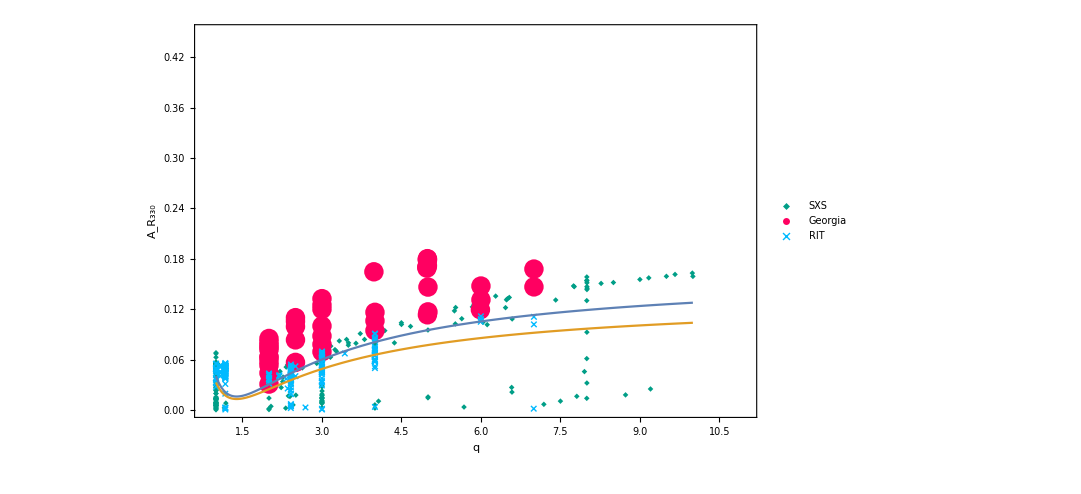

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,3}],TakeColumn[geoampratfin,{1,3}],TakeColumn[ritampratfin,{1,3}]},PlotRange->{{0.8,11},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{7.6,0.3}]];
Show[lamp,Plot[{amprat44[qq,0],amprat44[qq,-0.9]},{qq,1,10}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_44.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_21.pdf

```mathematica
amprat1sgima=Select[allampratfin,1.5≤ #[[1]]≤ 2.5&];
```

```mathematica
amprat1sgima2=Select[amprat1sgima,xspmin<=#[[2]]≤ xspmax&]
```

{}

```mathematica
(* Phase remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,Mod[sxs44[[All,2]]-4/2(sxs22[[All,2]]),2π]}];
geophdiff=Transpose[{geomassratio,geospin,Mod[-4/2(geo22[[All,2]]-π)-geo44[[All,2]],2π]}];
ritphdiff=Transpose[{ritmassratio,ritspin,Mod[4/2(rit22[[All,2]]-π)-rit44[[All,2]],2π]}];
```

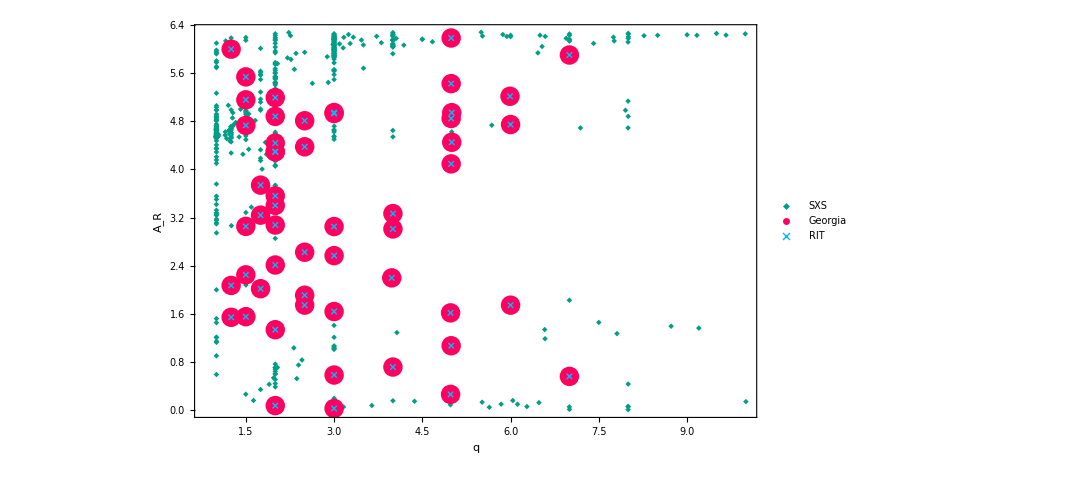

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,3}],TakeColumn[geophdiff,{1,3}],TakeColumn[geophdiff,{1,3}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

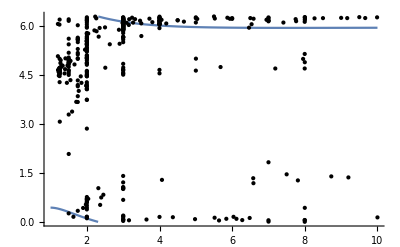

```mathematica
(* Comparison between the Cotesta et al. phase difference and ours. Notice that they fit at the peak of the 22 which adds a difference of 0.2 rads. *)
Plot[Mod[seobnrfits44[q,0],2π],{q,1,10},PlotRange->{All,{0,2π}},Epilog->{Point[Select[TakeColumn[sxsphdiff,{1,3}],#[[1]]>1.2&]]}]
```

```mathematica
(* Comparison between the Cotesta et al. phase difference and ours. Notice that they fit at the peak of the 22 which adds a difference of 0.2 rads. *)
Plot[Mod[seobnrfits44[q,0],2π],{q,1,10},PlotRange->{All,{0,2π}},Epilog->{Point[Select[TakeColumn[sxsphdiff,{1,3}],#[[1]]>1.2&]]}]
```

```mathematica
dm
```

(1-1/qq)/(1+1/qq)

```mathematica
sxsouts1=Position[sxsphdiff,_?(#[[1]]≤    1.1&)];
sxsouts=Join[sxsouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0.999833170061147247⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
geoouts=Position[geophdiff,_?(#[[1]]≤   1.1&)]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.25⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
ritouts1=Position[ritphdiff,_?(#[[1]]≤    1.1&)];
ritouts=Join[ritouts1];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sxsphdifffin=Select[Delete[sxsphdiff,sxsouts],#[[-1]]≥ 2&];
geophdifffin=Select[Delete[geophdiff,geoouts],#[[-1]]≥ 2&];
ritphdifffin=Select[Delete[ritphdiff,ritouts],#[[-1]]≥ 2&];
```

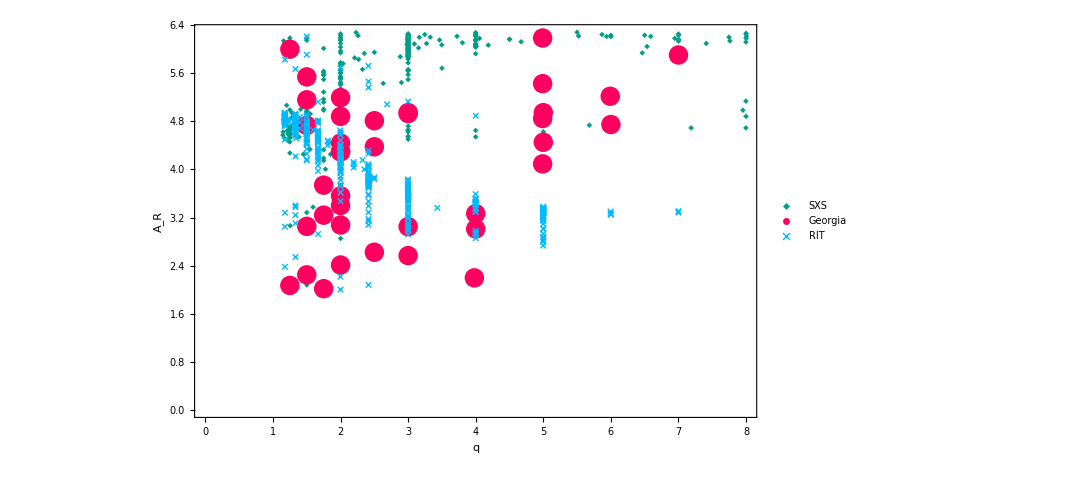

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdifffin,{1,3}],TakeColumn[geophdifffin,{1,3}],TakeColumn[ritphdifffin,{1,3}]},Frame->True,FrameLabel->{"q","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,26],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",3},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.75,0.85}]]
```

```mathematica
allphdifffin=Join[sxsphdifffin];
```

```mathematica
dm=(1-1/qq)/(1+1/qq);
ansatz33ph=a+b*Sqrt[(dm)]+c*dm+d*χ+dm^2*(e+f*χ)*χ;
```

```mathematica
fitph44=NonlinearModelFit[allphdifffin,ansatz33ph,{a,b,c,d,e,f},{qq,χ}]
```

FittedModel[4.2074570446930905+«58» √((1-1/(«2»))/(1+1/(«2»)))+(«1»)/(«1»)+«58» χ+((1-1/(«2»))^2 («58»+«57» χ) χ)/(1+1/qq)^2]

```mathematica
phasediff440[qq_,χ_]:=4.20745704469309050855248969575529778304`17.84038400927655+0.70151768333042689110948572369988259983`17.84038400927655 √((1-1/qq)/(1+1/qq))+(1.90834879126719537939393542884010367437`17.84038400927655 (1-1/qq))/(1+1/qq)+0.32423278756050244450211425566353525828`17.84038400927655 χ+1/(1+1/qq)^2(1-1/qq)^2 (0.12194043993401848598432671184945208016`17.84038400927655+0.1016687618901021403354388267714403938`17.84038400927655 χ) χ
```

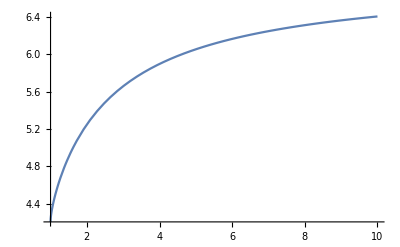

```mathematica
Plot[phasediff440[qq,0],{qq,1,10}]
```

```mathematica
Normal[fitph44]
```

4.2074570446930905+0.70151768333042689 √((1-1/qq)/(1+1/qq))+(1.9083487912671954 (1-1/qq))/(1+1/qq)+0.32423278756050244 χ+((1-1/qq)^2 (0.12194043993401849+0.10166876189010214 χ) χ)/(1+1/qq)^2

```mathematica
μϕ=Mean[fitph33["FitResiduals"]]
σϕ=StandardDeviation[fitph33["FitResiduals"]]
```

0.+0. ⅈ

0.127864445819469

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

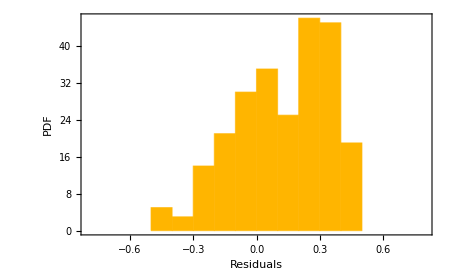

```mathematica
h1=Histogram[Select[fitph44["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

```mathematica
lphse=ListPlot[{Delete[TakeColumn[sxsphdifffin,{1,3}],331],TakeColumn[geophdifffin,{1,3}],TakeColumn[ritphdifffin,{1,3}]},Frame->True,FrameLabel->{"q","δϕ_330"},Frame->True,PlotRange->All,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{10.3,2.35}]]
```

-Graphics-

```mathematica
Export["~/Desktop/RDFits_330/phase_q_33.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_33.pdf

### Mode 44 new ansatz with χa

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxsspina,sxs44[[All,1]]/sxs22[[All,1]]}];
geoamprat=Transpose[{geomassratio,geospin,geospina,geo44[[All,1]]/geo22[[All,1]]}];
ritamprat=Transpose[{ritmassratio,ritspin,ritspina,rit44[[All,1]]/rit22[[All,1]]}];
```

```mathematica
sxsampratfin=Delete[sxsamprat,{}];
geoampratfin=Delete[geoamprat,{}];
ritampratfin=Delete[ritamprat,{}];
```

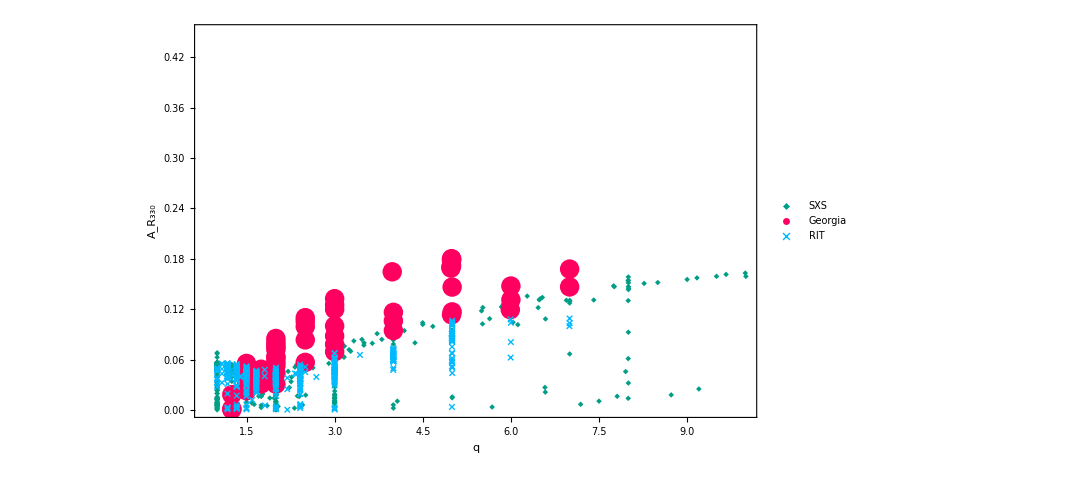

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}],TakeColumn[geoampratfin,{1,4}],TakeColumn[ritampratfin,{1,4}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
allampratfin=Join[sxsampratfin,ritampratfin];
```

```mathematica
allampratfin=Join[sxsampratfin];
```

```mathematica
npdata=Select[allampratfin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
ν=qq/(qq+1)^2
```

qq/(1+qq)^2

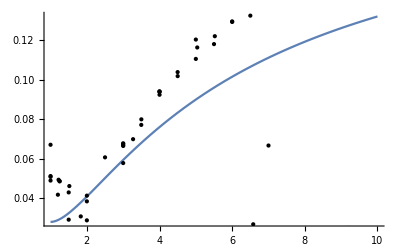

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,4}]],a0 (1-3ν)+a1 (1-3ν)^2,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

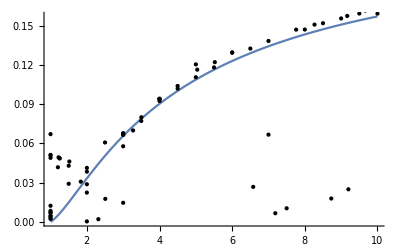

```mathematica
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
npdata2=Delete[npdata,outliers];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2+a2 Sqrt[1-4 ν]^2+a3 Sqrt[1-4 ν]^2,{a0,a1,a2,a3},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

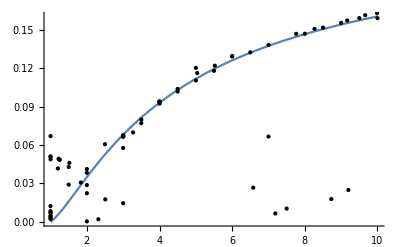

```mathematica
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
npdata2=Delete[npdata2,outliers];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],a0 Sqrt[1-4 ν]+a1 Sqrt[1-4 ν]^2+a2 Sqrt[1-4 ν]^2+a3 Sqrt[1-4 ν]^2,{a0,a1,a2,a3},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
allampratfinred=Complement[allampratfin,npdata];
fitamp21new=NonlinearModelFit[allampratfinred,Normal[nspfit]+b1 ν χs,{b0,b1},{qq,χs,χa},MaxIterations->1000]
```

FittedModel[0.042451203342473249 √(1-(4 qq)/(1+qq)^2)+0.18777572827593818 (1-(4 qq)/(«1»)^2)-(0.0120259688 qq χs)/(1+qq)^2]

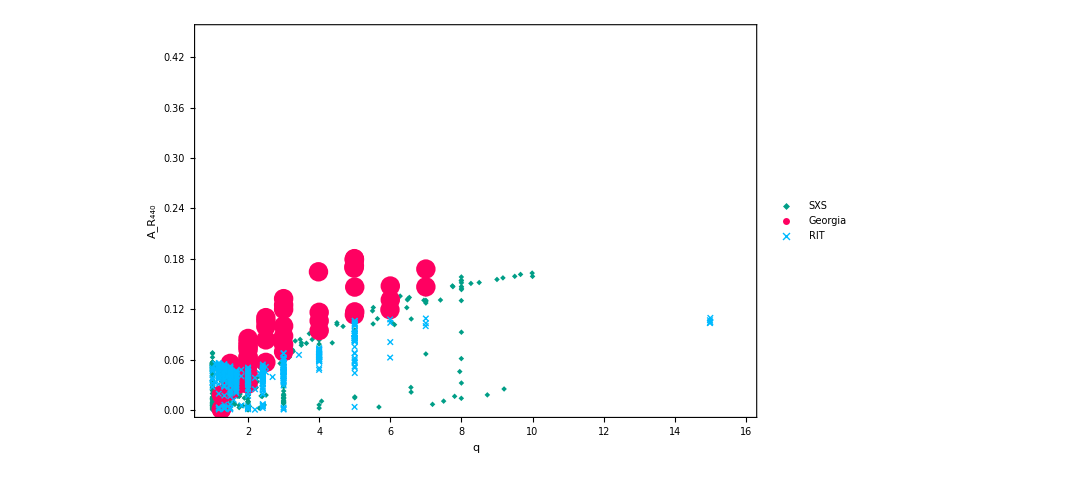

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}],TakeColumn[geoampratfin,{1,4}],TakeColumn[ritampratfin,{1,4}]},PlotRange->{{0.8,16},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_440"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{11.3,0.3}]]
```

### Mode 44 new ansatz with χa just SXS

```mathematica
(* Amplitude remove some outliers*)
sxsamprat=Transpose[{sxsmassratio,sxsspin,sxsspina,sxs44[[All,1]]/sxs22[[All,1]]}];
```

```mathematica
sxsampratfin=sxsamprat;
```

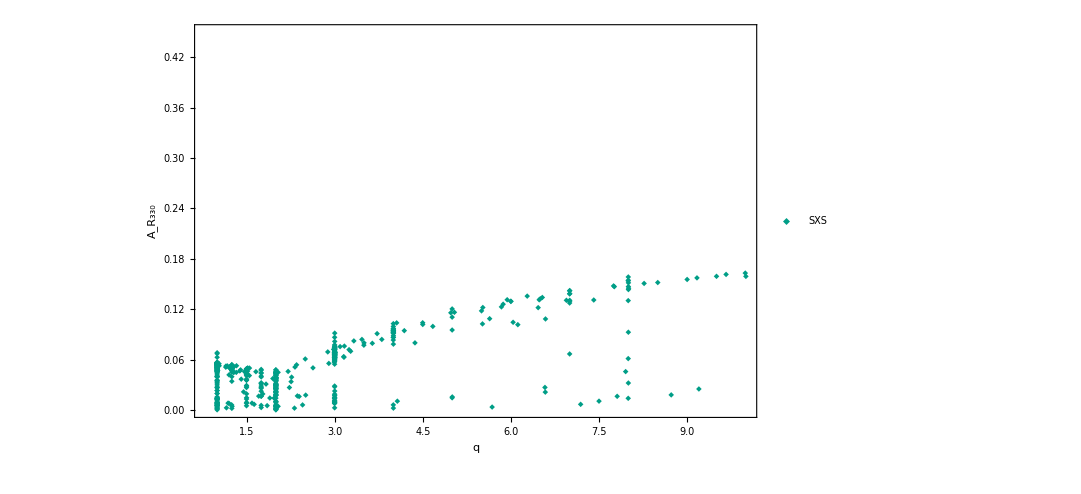

```mathematica
lamp=ListPlot[{TakeColumn[sxsampratfin,{1,4}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
(* Fit first non-spinning data *)
allampratfin=Join[sxsampratfin];
npdata=Select[allampratfin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
nspansatzamp=a0 (1-3ν)
ν=qq/(qq+1)^2
```

a0 (1-(3 qq)/(1+qq)^2)

qq/(1+qq)^2

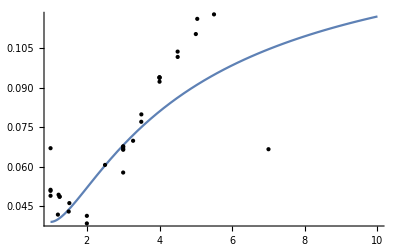

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,4}]],nspansatzamp,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

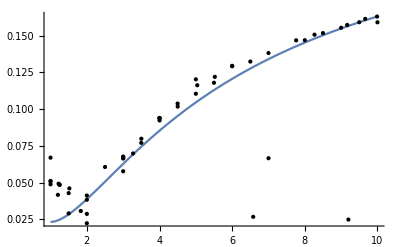

```mathematica
(* Eliminate outliers *)
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
npdata2=Delete[npdata,outliers];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],nspansatzamp+a1 (1-3ν)^2+a2 (1-3ν)^3,{a0,a1,a2},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
(* Fit the equal-massratio, unequal spin data. *)
allampratfinred=Complement[allampratfin,npdata];
fitamp21new=NonlinearModelFit[allampratfinred,Normal[nspfit]+b0(ν χs)+b1(ν χs)^2,{b0,b1},{qq,χs,χa},MaxIterations->1000]
μA=Mean[fitamp21new["FitResiduals"]]
σA=StandardDeviation[fitamp21new["FitResiduals"]]
```

FittedModel[0.018370669845159085 (1-(3 qq)/(1+qq)^2)+0.31730707923109427 (1-(«1»)/(«1»))^2-«59» «1»-(«58» qq χs)/(((«1»«1»)^2)+(0.13633164 qq^2 χs^2)/(1+qq)^4]

-0.002527316

0.02615892

```mathematica
(* Outlier hunter *)
outliers=Position[fitamp21new["FitResiduals"],_?(Abs[#]≥ 4st&)]
allampratfinred2=Delete[allampratfinred,outliers];
fitamp21newfinal=NonlinearModelFit[allampratfinred2,Normal[nspfit]+b0(ν χs)+b1(ν χs)^2,{b0,b1},{qq,χs,χa}];
μA=Mean[fitamp21newfinal["FitResiduals"]]
σA=StandardDeviation[fitamp21newfinal["FitResiduals"]]
```

{}

-0.002527316

0.02615892

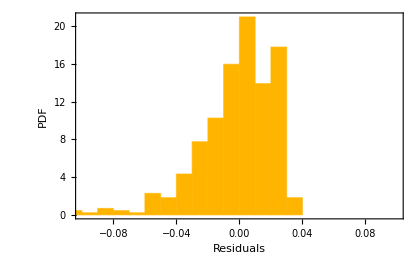

```mathematica
h1=Histogram[Chop[fitamp21newfinal["FitResiduals"]],20,"PDF",PlotRange->{{-0.1,0.1},All},ImageSize->420,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

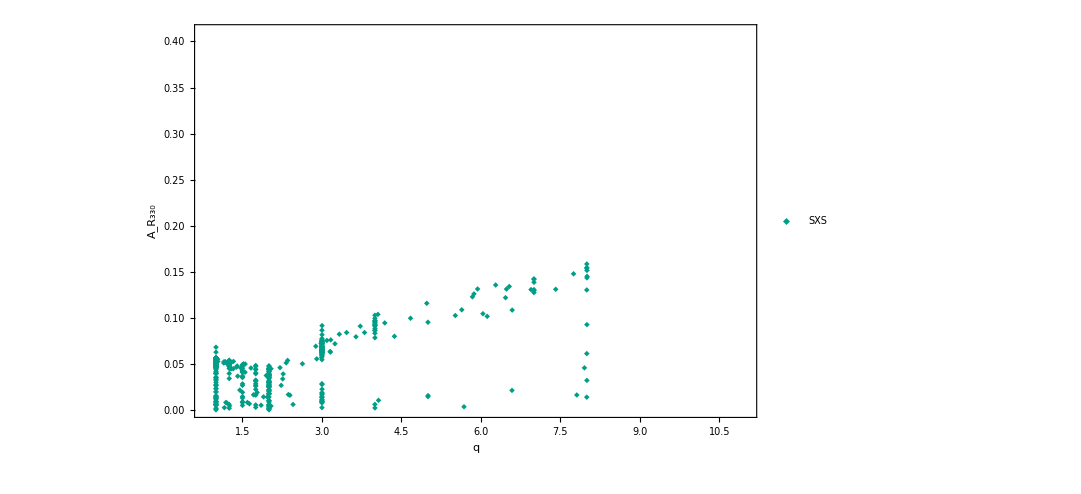

```mathematica
lamp=ListPlot[{TakeColumn[allampratfinred2,{1,4}]},PlotRange->{{0.8,11},{0,0.41}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],Epilog->Inset[h1,{7.3,0.13}]]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_q_44.pdf",lamp]
```

~/Desktop/RDFits_330/Aratio_q_44.pdf

```mathematica
(* Amplitude remove some outliers*)
sxsphdiff=Transpose[{sxsmassratio,sxsspin,sxsspina,Mod[4/2(sxs22[[All,2]])-sxs21[[All,2]],π]}];
```

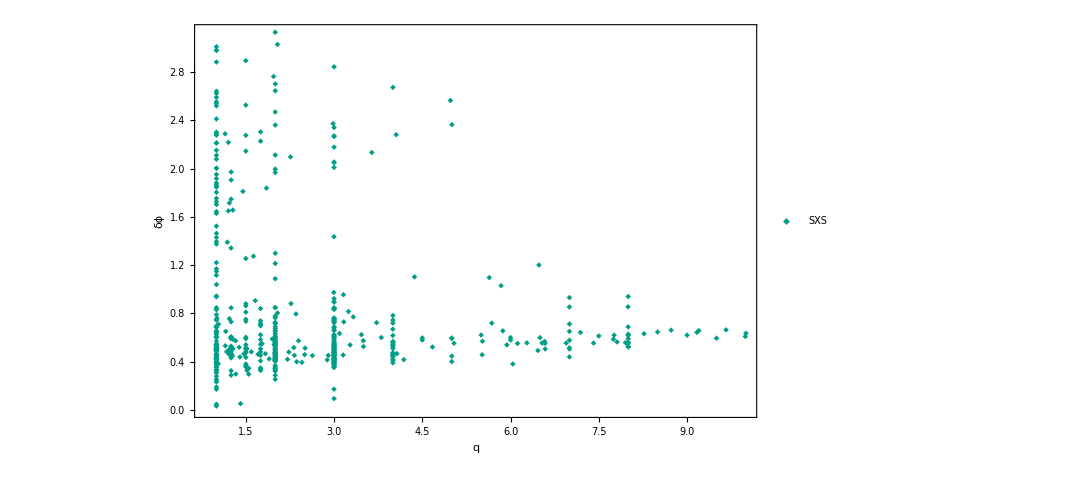

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,4}]},Frame->True,FrameLabel->{"q","δϕ"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

```mathematica
χ=χs+χa dm/(1-2ν);
ansatz44ph=a+ν^2(b+c χ)+d*χ+e*χ^2+ν^3(f+g χ)+ν(h +i χ +j χ^2);
ansatz44phnsp=ansatz44ph/.χa->0/.χs->0
```

a+(f qq^3)/(1+qq)^6+(b qq^2)/(1+qq)^4+(h qq)/(1+qq)^2

```mathematica
(* Fit first non-spinning data *)
sxsphdifffin=Join[sxsphdiff];
npdata=Select[sxsphdifffin,Abs[#[[2]]]≤ 0.01&&Abs[#[[3]]]≤ 0.01&];
ν=qq/(qq+1)^2
```

qq/(1+qq)^2

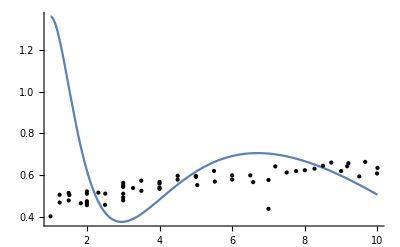

```mathematica
nspfit=NonlinearModelFit[npdata[[All,{1,4}]],ansatz44phnsp,{a,f,b,h},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->All,Epilog->Point[npdata[[All,{1,4}]]]]
```

Part::partd: Part specification List⟦-1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

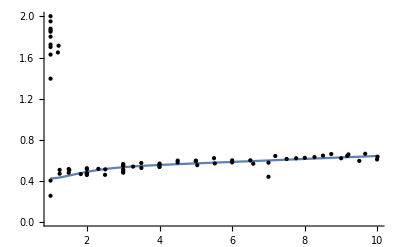

```mathematica
(* Eliminate outliers *)
st=StandardDeviation[nspfit["FitResiduals"]];
outliers=Position[nspfit["FitResiduals"],_?(Abs[#]≥ 2st&)];
outliers2=Position[npdata,_?(#[[-1]]≥ 1&)];
outliers=Join[outliers,outliers2];
npdata2=Delete[npdata,outliers2];
nspfit=NonlinearModelFit[npdata2[[All,{1,4}]],ansatz44phnsp,{a,f,b,h},qq];
Plot[Normal[nspfit],{qq,1,10},PlotRange->{All,{0,2}},Epilog->Point[npdata[[All,{1,4}]]]]
```

```mathematica
ansatz44final=ansatz44ph/.nspfit["BestFitParameters"];
```

```mathematica
allampratfinred=Complement[allampratfin,npdata2];
χ=χs+χa dm/(1-2ν);
dm=(1-1/qq)/(1+1/qq);
fitph44=NonlinearModelFit[allampratfinred,ansatz44final,{a,b,c,d,e,f,g,h,i,j},{qq,χs,χa}]
```

FittedModel[0.98166784745409461+1.5620684 (((1-1/qq) χa)/((1+1/qq) (1-«1»))+χs)-«57» «1»+«1»+((«2»)^2 «1»)/(«1»)^4+(qq (-6.7426808198873565-«40» («1»)-«39» («1»)^2))/(1+qq)^2]

```mathematica
μϕ=Mean[fitph44["FitResiduals"]]
σϕ=StandardDeviation[fitph44["FitResiduals"]]
```

-0.214136

0.223897

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

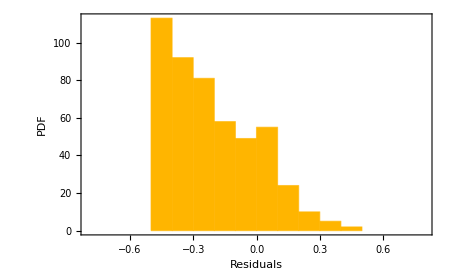

```mathematica
h1=Histogram[Select[fitph44["FitResiduals"],Abs[#]≤  0.5&],"PDF",PlotRange->{{-0.8,0.8},All},ImageSize->450,Frame->True,FrameLabel->{"Residuals","PDF"}, FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ChartStyle->colors[[4]]]
```

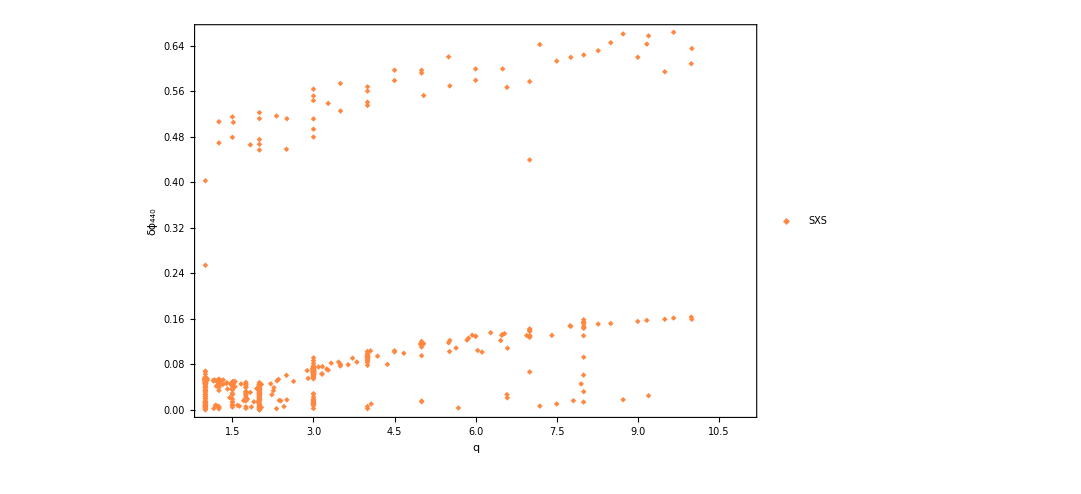

```mathematica
lphse=ListPlot[TakeColumn[Join[allampratfin,npdata2],{1,-1}],Frame->True,FrameLabel->{"q","δϕ_440"},Frame->True,PlotRange->{{1,11},All},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.2,0.2}],Epilog->Inset[h1,{7.452,2.55}]]
```

```mathematica
Export["~/Desktop/RDFits_330/phase_q_44.pdf",lphse]
```

~/Desktop/RDFits_330/phase_q_44.pdf

```mathematica
Clear[fit21phase]
```

```mathematica
fit21phase[1,2,0]
```

-0.0814368

```mathematica
fit21phase[qq_,χs_,χa_]:=Evaluate[Normal[fitph21]]
Plot[{fit21phase[qq,0,0],fit21phase[qq,0.5,0],fit21phase[qq,-0.5,0]},{qq,1,10}]
```

-Graphics-

```mathematica
fit21phasefun=
```

## Load NR Roberto

```mathematica
dir="/Users/xisco/Downloads/tables";
files=FileNames["*tex",dir]
```

{/Users/xisco/Downloads/tables/allnrsims.tex,/Users/xisco/Downloads/tables/nrsims.tex}

```mathematica
tab1=Import[files[[1]],"Text"];
tab2=Import[files[[2]],"Text"];
```

```mathematica
robtables2
```

{{
SXS:BBH:0610 , $1.2$ , $-0.50$ , $-0.50$ , $7.4\times 10^{-5}$ , $0.01872$ , $12.1$ },{
SXS:BBH:0611 , $1.4$ , $-0.50$ , $+0.50$ , $6.0\times 10^{-4}$ , $0.02033$ , $12.5$ },{
SXS:BBH:0612 , $1.6$ , $+0.50$ , $-0.50$ , $3.7\times 10^{-4}$ , $0.02156$ , $12.8$ },{
SXS:BBH:0613 , $1.8$ , $+0.50$ , $+0.50$ , $1.8\times 10^{-4}$ , $0.02383$ , $13.1$ },{
SXS:BBH:0614 , $2.0$ , $+0.75$ , $-0.50$ , $6.7\times 10^{-4}$ , $0.02355$ , $13.1$ },{
SXS:BBH:0615 , $2.0$ , $+0.75$ , $+0.00$ , $7.0\times 10^{-4}$ , $0.02401$ , $13.3$ },{
SXS:BBH:0616 , $2.0$ , $+0.75$ , $+0.50$ , $8.0\times 10^{-4}$ , $0.02475$ , $13.3$ },{
SXS:BBH:0617 , $2.0$ , $+0.50$ , $+0.75$ , $7.8\times 10^{-4}$ , $0.02342$ , $13.1$ },{
SXS:BBH:0618 , $2.0$ , $+0.80$ , $+0.80$ , $5.9\times 10^{-4}$ , $0.02578$ , $13.4$ },{
SXS:BBH:0619 , $2.0$ , $+0.90$ , $+0.90$ , $2.9\times 10^{-4}$ , $0.02520$ , $13.5$ },{
SXS:BBH:0620 , $5.0$ , $-0.80$ , $+0.00$ , $1.7\times 10^{-4}$ , $0.02551$ , $8.1$ },{
SXS:BBH:0621 , $7.0$ , $-0.80$ , $+0.00$ , $4.8\times 10^{-4}$ , $0.02828$ , $7.2$ },{
SXS:BBH:0622 , $8.0$ , $-0.90$ , $+0.00$ , $1.1\times 10^{-3}$ , $0.01559$ , $28.0$ },{
}}

```mathematica
robtables=StringSplit[#,"&"]&/@StringSplit[StringSplit[tab1,{"\endhead","%\\end{tabular}"}][[2]],{"\\\\"}];
robtables2=StringSplit[#,"&"]&/@StringSplit[StringSplit[tab2,{"\hline","%\\end{tabular}"}][[2]],{"\\\\"}];
```

```mathematica
robtags=Sort[StringTrim/@Join[robtables[[All,1]],robtables2[[All,1]]][[1;;-2]]]
```

{,SXS:BBH:0004,SXS:BBH:0005,SXS:BBH:0007,SXS:BBH:0013,SXS:BBH:0016,SXS:BBH:0019,SXS:BBH:0025,SXS:BBH:0030,SXS:BBH:0036,SXS:BBH:0045,SXS:BBH:0046,SXS:BBH:0047,SXS:BBH:0056,SXS:BBH:0060,SXS:BBH:0061,SXS:BBH:0063,SXS:BBH:0064,SXS:BBH:0065,SXS:BBH:0148,SXS:BBH:0149,SXS:BBH:0150,SXS:BBH:0151,SXS:BBH:0152,SXS:BBH:0153,SXS:BBH:0154,SXS:BBH:0155,SXS:BBH:0156,SXS:BBH:0157,SXS:BBH:0158,SXS:BBH:0159,SXS:BBH:0160,SXS:BBH:0166,SXS:BBH:0167,SXS:BBH:0169,SXS:BBH:0170,SXS:BBH:0172,SXS:BBH:0174,SXS:BBH:0177,SXS:BBH:0178,SXS:BBH:0180,SXS:BBH:0202,SXS:BBH:0203,SXS:BBH:0204,SXS:BBH:0205,SXS:BBH:0206,SXS:BBH:0207,SXS:BBH:0209,SXS:BBH:0210,SXS:BBH:0211,SXS:BBH:0212,SXS:BBH:0213,SXS:BBH:0214,SXS:BBH:0215,SXS:BBH:0216,SXS:BBH:0217,SXS:BBH:0218,SXS:BBH:0219,SXS:BBH:0220,SXS:BBH:0221,SXS:BBH:0222,SXS:BBH:0223,SXS:BBH:0224,SXS:BBH:0225,SXS:BBH:0226,SXS:BBH:0227,SXS:BBH:0228,SXS:BBH:0229,SXS:BBH:0230,SXS:BBH:0231,SXS:BBH:0232,SXS:BBH:0233,SXS:BBH:0234,SXS:BBH:0235,SXS:BBH:0236,SXS:BBH:0237,SXS:BBH:0238,SXS:BBH:0239,SXS:BBH:0240,SXS:BBH:0241,SXS:BBH:0242,SXS:BBH:0243,SXS:BBH:0244,SXS:BBH:0245,SXS:BBH:0246,SXS:BBH:0247,SXS:BBH:0248,SXS:BBH:0249,SXS:BBH:0250,SXS:BBH:0251,SXS:BBH:0252,SXS:BBH:0253,SXS:BBH:0254,SXS:BBH:0255,SXS:BBH:0256,SXS:BBH:0257,SXS:BBH:0258,SXS:BBH:0259,SXS:BBH:0260,SXS:BBH:0261,SXS:BBH:0262,SXS:BBH:0263,SXS:BBH:0264,SXS:BBH:0265,SXS:BBH:0266,SXS:BBH:0267,SXS:BBH:0268,SXS:BBH:0269,SXS:BBH:0270,SXS:BBH:0271,SXS:BBH:0272,SXS:BBH:0273,SXS:BBH:0274,SXS:BBH:0275,SXS:BBH:0276,SXS:BBH:0277,SXS:BBH:0278,SXS:BBH:0279,SXS:BBH:0280,SXS:BBH:0281,SXS:BBH:0282,SXS:BBH:0283,SXS:BBH:0284,SXS:BBH:0285,SXS:BBH:0286,SXS:BBH:0287,SXS:BBH:0288,SXS:BBH:0289,SXS:BBH:0290,SXS:BBH:0291,SXS:BBH:0292,SXS:BBH:0293,SXS:BBH:0295,SXS:BBH:0296,SXS:BBH:0297,SXS:BBH:0298,SXS:BBH:0299,SXS:BBH:0300,SXS:BBH:0301,SXS:BBH:0302,SXS:BBH:0303,SXS:BBH:0306,SXS:BBH:0610,SXS:BBH:0611,SXS:BBH:0612,SXS:BBH:0613,SXS:BBH:0614,SXS:BBH:0615,SXS:BBH:0616,SXS:BBH:0617,SXS:BBH:0618,SXS:BBH:0619,SXS:BBH:0620,SXS:BBH:0621,SXS:BBH:0622}

```mathematica
dir="~/mount/Atlas/sio/git/RDFits_amp_phase/";
files=FileNames["*rob*txt",dir]
```

{~/mount/Atlas/sio/git/RDFits_amp_phase/RD_amp_phase_21_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/RD_amp_phase_22_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/RD_amp_phase_33_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/RD_amp_phase_44_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_1_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_2_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_chi_eff_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_massratio_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_21_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_22_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_33_rob.txt,~/mount/Atlas/sio/git/RDFits_amp_phase/sxs_RD_amp_phase_44_rob.txt}

```mathematica
robmassratio=Max[#,1]&/@Flatten@Import[FileNames["sxs*massratio*rob.txt",dir][[1]],"Data"];
robspin=Flatten@Import[FileNames["sxs*chi*rob.txt",dir][[1]],"Data"];
robspin1=Import[FileNames["sxs*chi_1*rob.txt",dir][[1]],"Data"];
robspin2=Import[FileNames["sxs*chi_2*rob.txt",dir][[1]],"Data"];
robspina=Flatten[robmassratio/(robmassratio+1)*robspin1-1/(robmassratio+1)*robspin2];
rob22=Import[FileNames["sxs*22*rob.txt",dir][[1]],"Data"];
rob21=Import[FileNames["sxs*21*rob.txt",dir][[1]],"Data"];
rob33=Import[FileNames["sxs*33*rob.txt",dir][[1]],"Data"];
rob44=Import[FileNames["sxs*44*rob.txt",dir][[1]],"Data"];
rob55=Import[FileNames["sxs*55*rob.txt",dir][[1]],"Data"];
dmrob=(robmassratio-1)/(robmassratio+1);
etarob=robmassratio/(robmassratio+1)^2;
```

```mathematica
dm=(qq-1)/(qq+1)
```

(-1+qq)/(1+qq)

### Mode 33, 21, 44, 55 phase

```mathematica
Length/@{robmassratio,robspin,robspina,Mod[-rob33[[All,2]]+3/2(rob22[[All,2]]),π]}
```

{142,142,142,142}

```mathematica
(* Amplitude remove some outliers*)
phasediff330alone=Mod[-rob33[[All,2]]+3/2(rob22[[All,2]]),π];
sxsphdiff=Transpose[{robmassratio,robspin,robspina,phasediff330alone}];
sxsphdiffref=Transpose[{robmassratio,robspina+robspin*dmrob/(1-2etarob),phasediff330alone}];
```

```mathematica
robfit33=Transpose[{robmassratio,Mod[seobnrfits33[robmassratio,robspina+robspin*dmrob/(1-2etarob)],π]}];
```

```mathematica
phase33ansatz=a+b Sqrt[dm]+c dm+d χχ+e dm^2(f+g χχ)χχ
myphfit33[qq_,χχ_]:=Evaluate[Normal@NonlinearModelFit[sxsphdiffref,phase33ansatz,{a,b,c,d,e,f,g},{qq,χχ}]];
myphfitres33=Transpose[{robmassratio,myphfit33[robmassratio,robspina+robspin*dmrob/(1-2etarob)]}];
```

a+b √((-1+qq)/(1+qq))+(c (-1+qq))/(1+qq)+d χχ+(e (-1+qq)^2 χχ (f+g χχ))/(1+qq)^2

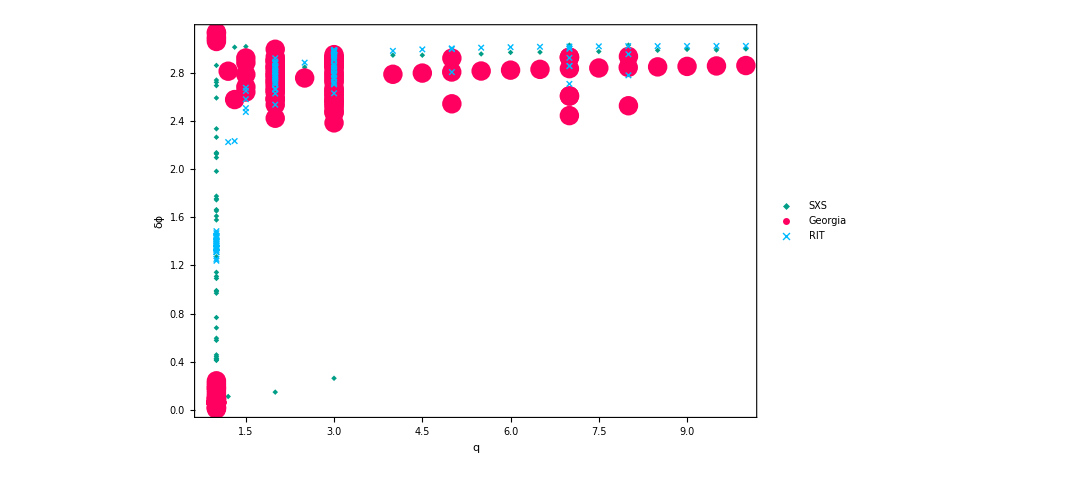

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,-1}],robfit33,myphfitres33},Frame->True,FrameLabel->{"q","δϕ"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

```mathematica
(* Amplitude remove some outliers*)
sxsphdiff=Transpose[{robmassratio,robspin,robspina,Mod[-rob21[[All,2]]+1/2(rob22[[All,2]])-0.35,π]}];
robfit21=Transpose[{robmassratio,seobnrfits21[robmassratio,robspina+robspin*dmrob/(1-2etarob)]}];
```

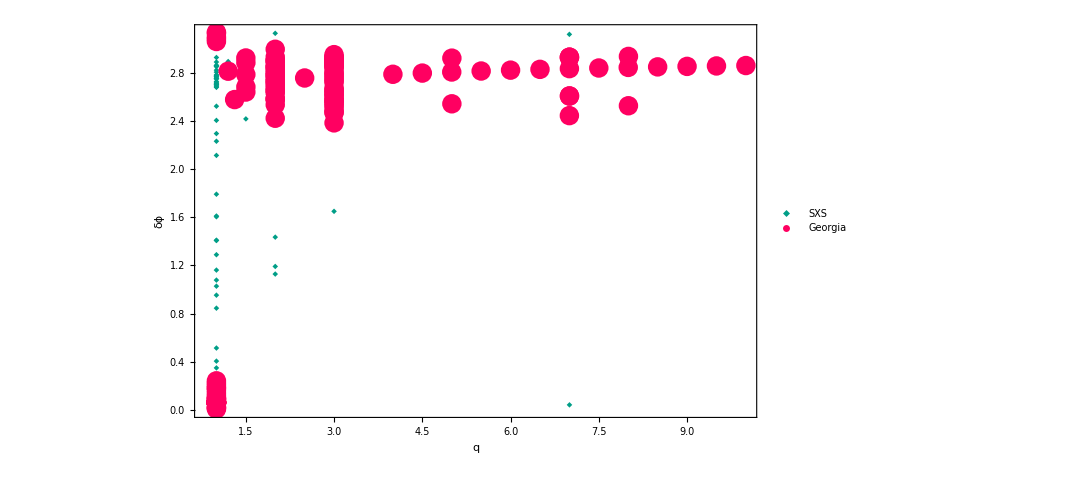

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,-1}],robfit33},Frame->True,FrameLabel->{"q","δϕ"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

```mathematica
sxsphdiff=Transpose[{robmassratio,robspin,robspina,Mod[-rob44[[All,2]]+4/2(rob22[[All,2]]),2π]}];
robfit44=Transpose[{robmassratio,Mod[seobnrfits44[robmassratio,robspina+robspin*dmrob/(1-2etarob)],2π]}];
```

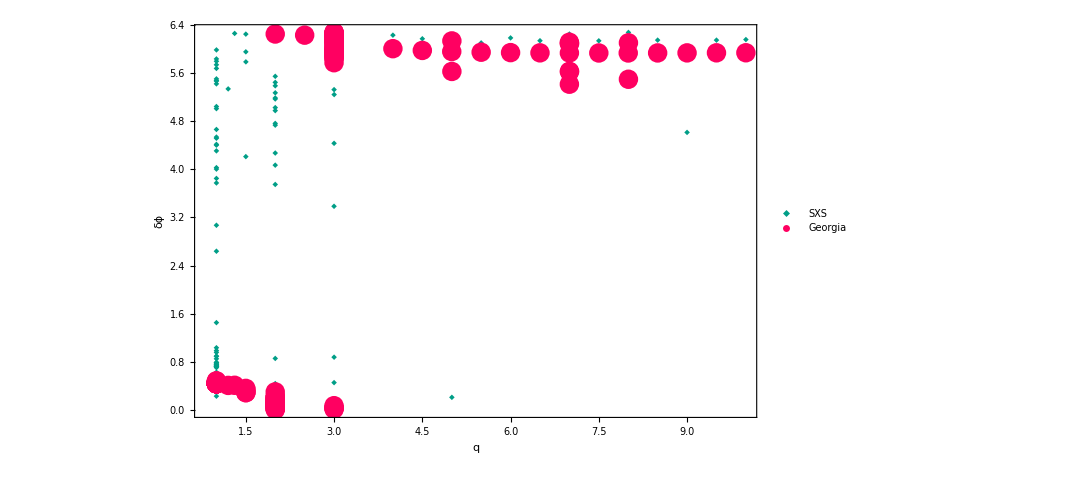

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,-1}],robfit44},Frame->True,FrameLabel->{"q","δϕ"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

```mathematica
sxsphdiff=Transpose[{robmassratio,robspin,robspina,Mod[-rob55[[All,2]]+5/2(rob22[[All,2]]),π]}];
robfit55=Transpose[{robmassratio,Mod[seobnrfits55[robmassratio,robspina+robspin*dmrob/(1-2etarob)],2π]}];
```

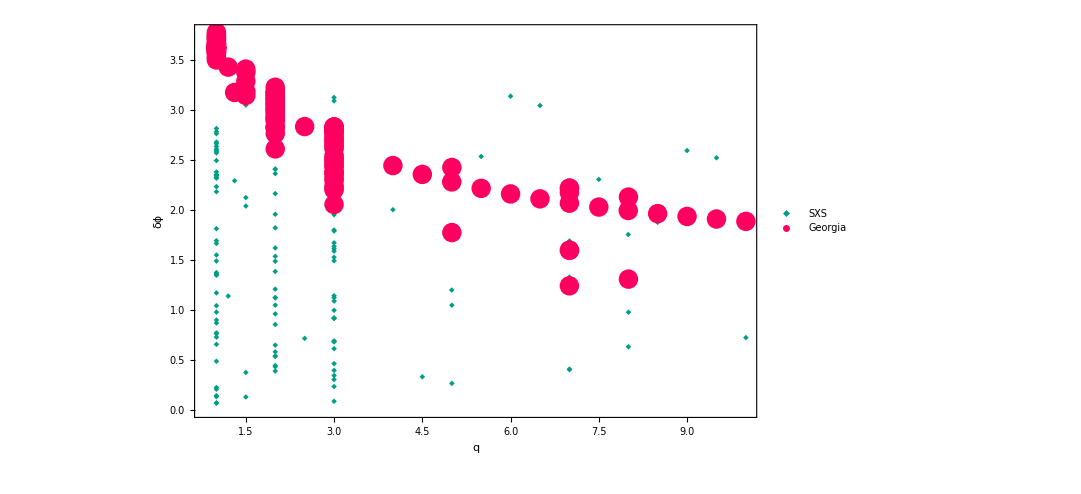

```mathematica
lamp=ListPlot[{TakeColumn[sxsphdiff,{1,-1}],robfit55},Frame->True,FrameLabel->{"q","δϕ"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","Georgia","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}],PlotRange->All]
```

### Mode 33,21,44 , 55

```mathematica
(* Amplitude remove some outliers*)
robamprat33=Transpose[{robmassratio,robspina+dmrob robspin,rob33[[All,1]]/rob22[[All,1]]}];
robamprat21=Transpose[{robmassratio,robspina+dmrob robspin,rob21[[All,1]]/rob22[[All,1]]}];robamprat44=Transpose[{robmassratio,robspina+dmrob robspin,rob44[[All,1]]/rob22[[All,1]]}];
robamprat55=Transpose[{robmassratio,robspina+dmrob robspin,rob55[[All,1]]/rob22[[All,1]]}];
```

```mathematica
ansatz33=a0 √(1-(4 qq)/(1+qq)^2)+a1 (1-(4 qq)/(1+qq)^2)+b0 χχ;
amp33fitfun=NonlinearModelFit[robamprat33,ansatz33,{a0,a1,b0},{qq,χχ}];
amp33fitfunn=Normal[amp33fitfun];
amp33fit[qq_,χχ_]:=Evaluate[amp33fitfunn]
```

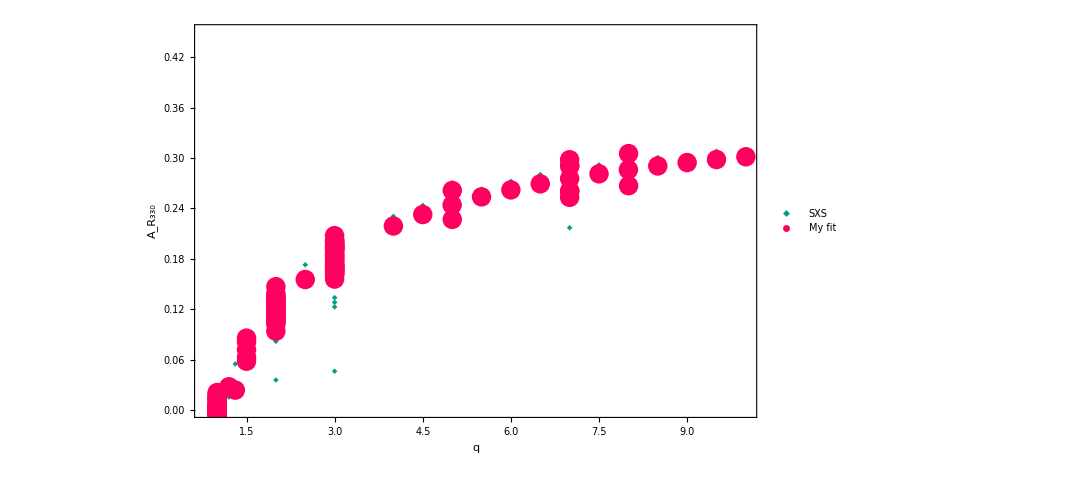

```mathematica
lamp=ListPlot[{TakeColumn[robamprat33,{1,-1}],Transpose[{robamprat33[[All,1]],amp33fit[robamprat33[[All,1]],robamprat33[[All,2]]]}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","My fit","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
ansatz21=a0 √(1-(4 qq)/(1+qq)^2)+a1 (1-(4 qq)/(1+qq)^2)+b0 χχ;
amp21fitfun=NonlinearModelFit[robamprat21,ansatz21,{a0,a1,b0},{qq,χχ}];
amp21fitfunn=Normal[amp21fitfun];
amp21fit[qq_,χχ_]:=Evaluate[amp21fitfunn]
```

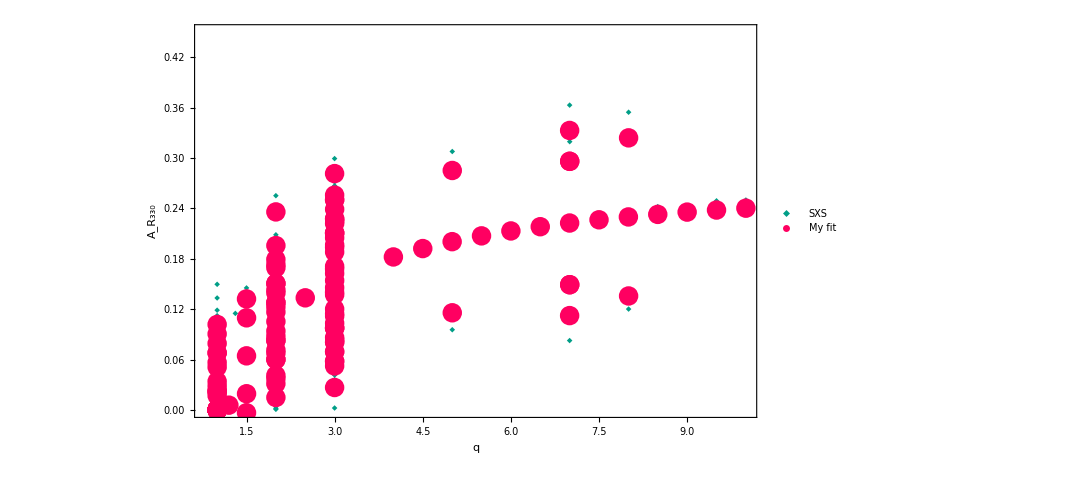

```mathematica
lamp=ListPlot[{TakeColumn[robamprat21,{1,-1}],Transpose[{robamprat21[[All,1]],amp21fit[robamprat21[[All,1]],robamprat21[[All,2]]]}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_330"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","My fit","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
ansatz44=a0 (1-3 qq/(1+qq)^2 )+a1 (1-3 qq/(1+qq)^2 )^2+b0 χχ;
amp44fitfun=NonlinearModelFit[robamprat44,ansatz44,{a0,a1,b0},{qq,χχ}];
amp44fitfunn=Normal[amp44fitfun];
amp44fit[qq_,χχ_]:=Evaluate[amp44fitfunn]
```

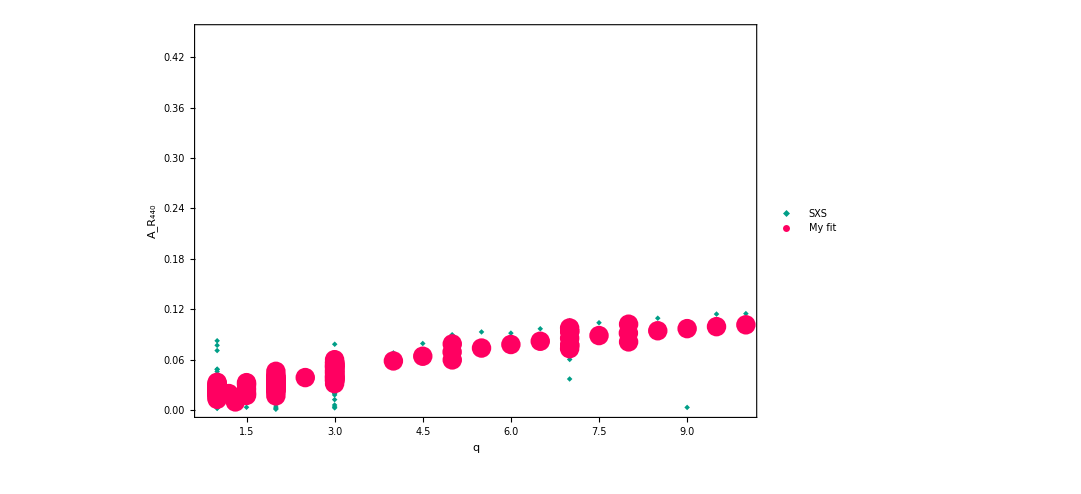

```mathematica
lamp=ListPlot[{TakeColumn[robamprat44,{1,-1}],Transpose[{robamprat44[[All,1]],amp44fit[robamprat44[[All,1]],robamprat44[[All,2]]]}]},PlotRange->{{0.8,10},{0,0.45}},Frame->True,FrameLabel->{"q","A_R_440"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","My fit","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

```mathematica
ansatz55=a0 √(1-(4 qq)/(1+qq)^2)+a1 (1-(4 qq)/(1+qq)^2)+b0 χχ;
amp55fitfun=NonlinearModelFit[robamprat55,ansatz55,{a0,a1,b0},{qq,χχ}];
amp55fitfunn=Normal[amp55fitfun];
amp55fit[qq_,χχ_]:=Evaluate[amp55fitfunn]
```

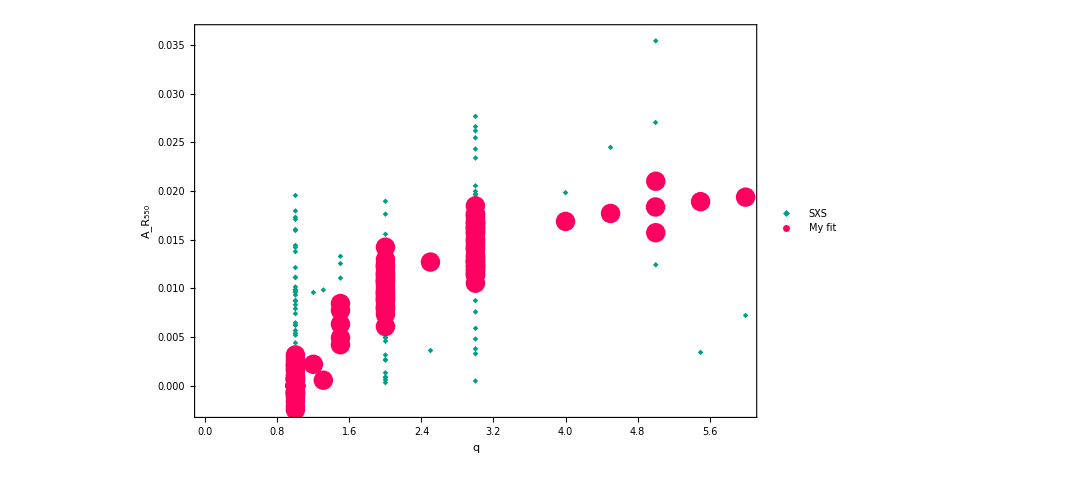

```mathematica
lamp=ListPlot[{TakeColumn[robamprat55,{1,-1}],Transpose[{robamprat55[[All,1]],amp55fit[robamprat55[[All,1]],robamprat55[[All,2]]]}]},Frame->True,FrameLabel->{"q","A_R_550"},Frame->True,FrameStyle->Directive[Black,Bold,20],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{"×",Scaled[0.04]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"SXS","My fit","RIT","LIGO-q","Capano-q"},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{"×",0.15},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.15,0.85}]]
```

## Load and plot posteriors

### Paper results

```mathematica
Quit[]
```

```mathematica
(* Colin's posteriors *)
myfile="/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/kerr/220_330/KERR-220_330-07MS.hdf"

logw=Import[myfile,{"Datasets","/samples/logwt"}];
logev=ExternalEvaluate[Global`session, "file='"<>myfile<>"';
f1 = h5py.File(file,'r'); f1.attrs.get('log_evidence')"];
wt=Exp[logw-logev];
weights=wt/Total[wt];
amp33=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/amp330"}],weights]];
phase33=Normal[Import[myfile,{"Datasets","/samples/phi330"}]];
phase22=Normal[Import[myfile,{"Datasets","/samples/phi220"}]];
finalspin=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/final_spin"}],weights]];
phasediff=Mod[posteriorsamps[(3/2 phase22-phase33),weights],2π];
```

/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/kerr/220_330/KERR-220_330-07MS.hdf

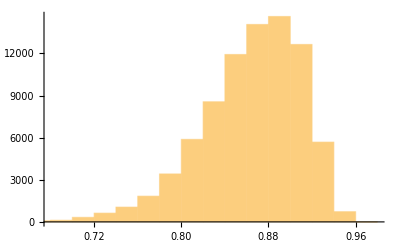

```mathematica
Histogram[finalspin]
```

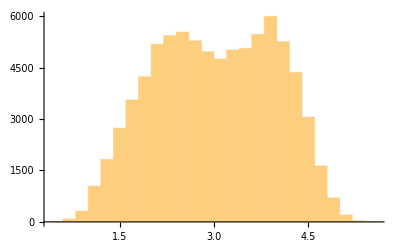

```mathematica
Histogram[phasediff]
```

```mathematica
finalspindist=SmoothKernelDistribution[finalspin]
```

DataDistribution[…]

```mathematica
spinmaxres=NMinimize[{χfun[x,finalspindist],0.7≤ x≤0.95},{x}]
```

{-4.38966,{x→0.889802}}

```mathematica
spinmax=x/.spinmaxres[[2]]
chi2spin=spinmaxres[[1]]
```

0.889802

-4.38966

```mathematica
(* 1 sigma *)
xspmin=x/.FindRoot[χfun[x,finalspindist]==chi2spin+1,{x,0.7}]
xspmax=x/.FindRoot[χfun[x,finalspindist]==chi2spin+1,{x,0.93}]
```

0.832775

0.921455

```mathematica
qdistcol=Select[(qq/.Table[FindRoot[amp33[[i]]==amp33fit[qq,spinmax],{qq,2,1,15}],{i,Length@amp33}]),#≠15&];
```

FindRoot::reged: The point {15.} is at the edge of the search region {1.,15.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {qq} = {1.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

```mathematica
FindRoot[{Mod[phasediff330[qq,χ],π]==phasediffngr[[1]],a330new[qq,χ]==amp33ngr[[1]]},{qq,4,1,10},{χ,0,-1,1}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {qq,χ} = {4.,0.}. Try perturbing the initial point(s).

{qq→4.,χ→0.}

```mathematica
qχdistcol=Select[{qq,χ}/.Table[FindRoot[{Mod[phasediff330[qq,χ],π]==phasediffngr[[i]],a330new[qq,χ]==amp33ngr[[i]]},{qq,2,1,15},{χ,0,-0.2,1}],{i,Length@amp33ngr}],#[[1]]≠15&]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {qq,χ} = {2.,0.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

```mathematica
Clear[logw,myfile,wt,logev,weights,amp33ngr,phase33ngr,phase22ngr]
```

```mathematica
Quit[]
```

```mathematica
(* Colin's posteriors *)
myfile="/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/nongr/NONGR-220_330-07MS.hdf"

logwngr=Import[myfile,{"Datasets","/samples/logwt"}];
logevngr=ExternalEvaluate[Global`session, "file='"<>myfile<>"';
f1 = h5py.File(file,'r'); f1.attrs.get('log_evidence')"];
wtngr=Exp[logwngr-logevngr];
weightsngr=wtngr/Total[wtngr];
amp33ngr=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/amp330"}],weightsngr]];
phase33nweights=Import[myfile,{"Datasets","/samples/phi330"}];
phase33ngr=Normal[Import[myfile,{"Datasets","/samples/phi330"}]];
phase22ngr=Normal[Import[myfile,{"Datasets","/samples/phi220"}]];
phasediffngr=posteriorsamps[3/2*phase22ngr-phase33ngr,weightsngr];
```

/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/nongr/NONGR-220_330-07MS.hdf

```mathematica
amp33distngr=SmoothKernelDistribution[Normal[amp33ngr]];
amp33dist=SmoothKernelDistribution[Normal[amp33]];
phasedistngr=SmoothKernelDistribution[phasediff];
```

```mathematica
phaseamp=SmoothKernelDistribution[Transpose[{Normal[amp33],phasediff}]];
phaseampngr=SmoothKernelDistribution[Transpose[{Normal[amp33ngr],phasediffngr}]];
```

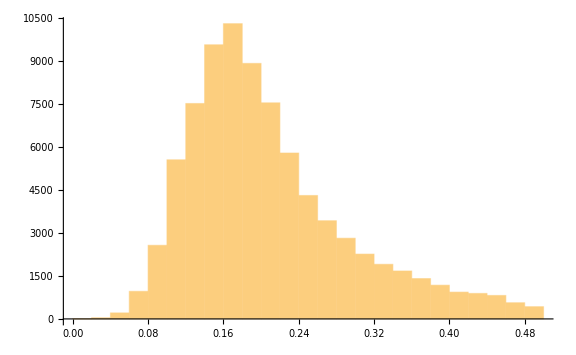
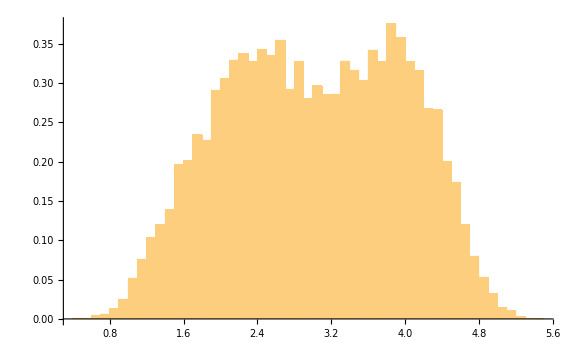

```mathematica
{Histogram[Normal[amp33],ImageSize->Large],Histogram[phasediff,50,"PDF",ImageSize->Large]}
```

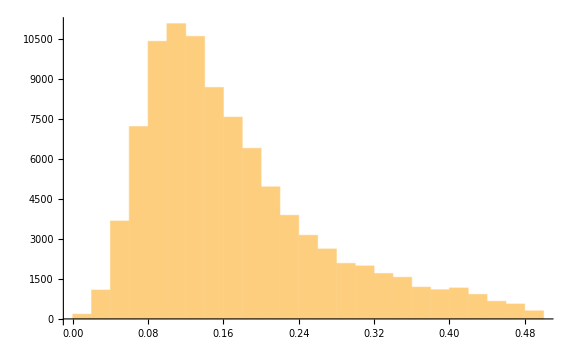
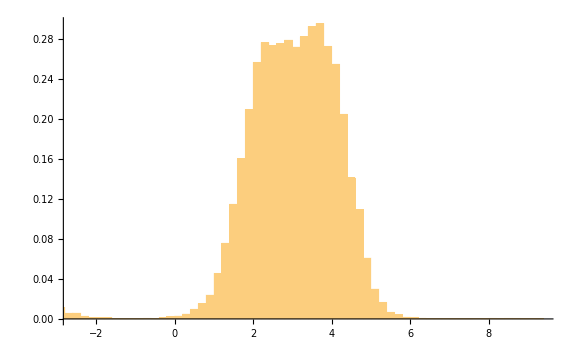

```mathematica
{Histogram[amp33ngr,ImageSize->Large],Histogram[phasediffngr,50,"PDF",ImageSize->Large]}
```

```mathematica
chi2=NMinimize[{χfun[{x,y},phaseamp],0.001≤ x≤0.4, 0<=y≤2π},{x,y}]
```

{-1.50219,{x→0.170468,y→3.80214}}

```mathematica
chi2ngr=NMinimize[{χfun[{x,y},phaseampngr],0.001≤ x≤0.3, 0<=y≤2π},{x,y}]
```

{-1.05306,{x→0.110418,y→2.78925}}

```mathematica
phsall=Flatten[Table[{Mod[seobnrfits33[qq,χ],π],amp33fit[qq,χ]},{χ,-0.9,0.9,0.03},{qq,1.2,15,0.05}],1];
```

```mathematica
bvalsngr={y,x}/.chi2ngr[[2]]
bvalgr={y,x}/.chi2[[2]]
```

{2.78925,0.110418}

{3.80214,0.170468}

```mathematica
amp33sxs=TakeColumn[sxsampratfin,{-1}];
ph33sxs=TakeColumn[sxsphdifffin,{-1}];
```

```mathematica
phsall
```

{{1.2,3.05051,0.0531407},{1.25,3.02747,0.0603896},{1.3,3.00917,0.0673356},{1.35,2.9943,0.0739972},{1.4,2.98203,0.0803915},{1.45,2.97178,0.0865342},16885,{14.75,2.54583,0.30192},{14.8,2.54586,0.302074},{14.85,2.54589,0.302227},{14.9,2.54592,0.302379},{14.95,2.54594,0.30253},{15.,2.54597,0.302681}}
 |  |  |  |

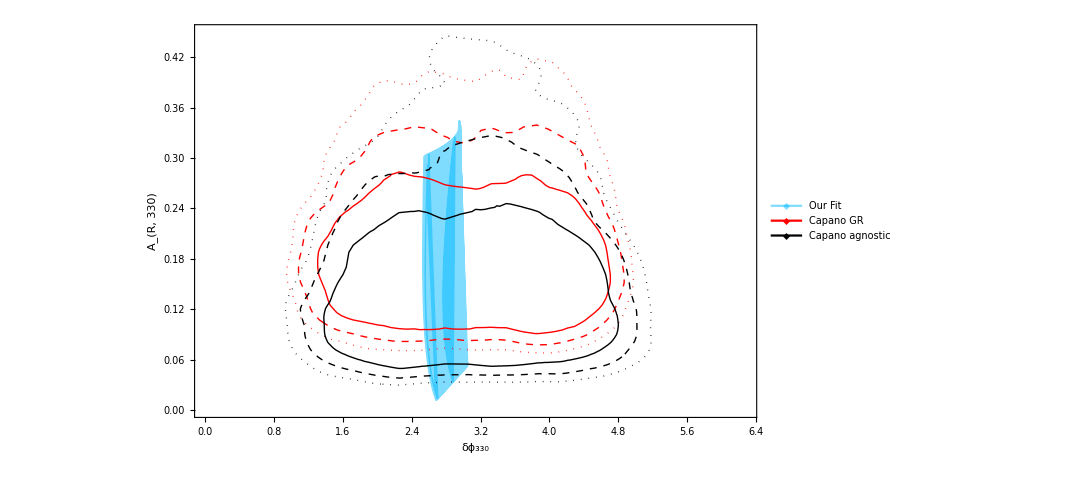

```mathematica
c1=ContourPlot[χfun[{x,y},phaseamp],{y,Min[phasediff],Max[phasediff]},{x,0,Max[Normal[amp33]]},ContourShading->None,ContourStyle->{Directive[Red],Directive[Red,Dashed],Directive[Red,Dotted]},Contours->{chi2[[1]]+2.3,chi2[[1]]+3.5,chi2[[1]]+4.6} ,PlotLegends->Placed[LineLegend[{Style["Capano GR",24]},LegendMarkers->{{markers[[3]],0.05},{markers[[1]],0.05},{markers[[2]],0.05}}],{0.15,0.85}],ImageSize->Large];
c2=ContourPlot[χfun[{x,y},phaseampngr],{y,Min[phasediff],Max[phasediff]},{x,Min[Normal[amp33ngr]],Max[Normal[amp33ngr]]},ContourShading->None,Contours->{chi2ngr[[1]]+2.3,chi2ngr[[1]]+3.5,chi2ngr[[1]]+4.6},ContourStyle->{Directive[Black],Directive[Black,Dashed],Directive[Black,Dotted]},PlotLegends->Placed[LineLegend[{Style["Capano agnostic",24]},LegendLayout->{"Column",3},LegendMarkers->{{markers[[3]],0.05},{markers[[1]],0.05},{markers[[2]],0.05}}],{0.15,0.93}]];
l4=ListPlot[{phsall},FrameStyle->Directive[Black,Bold,26],ImageSize->550,Joined->True,PlotStyle->{Directive[colors[[3]],Opacity[0.5]],Directive[colors[[4]],Opacity[0.5]]},Frame->True,PlotLegends->Placed[LineLegend[{Style["Our Fit",24],Style["LL Fit",24]},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.05},{markers[[1]],0.05},{markers[[2]],0.05}}],{0.15,0.78}],FrameLabel->{"δϕ_330","A_(R, 330)"},Frame->True,PlotRange->{{0,2π},{0,0.45}},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,16],GridLines->Full];
s1=Show[l4,c1,c2,ImageSize->800]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_phase.pdf",s1]
```

~/Desktop/RDFits_330/Aratio_phase.pdf

```mathematica
phsall21=Flatten[Table[{Mod[seobnrfits21[qq,χ],π],amp21fit[qq,χ]},{χ,-0.9,0.9,0.03},{qq,1.2,15,0.05}],1];
phsall44=Flatten[Table[{Mod[seobnrfits44[qq,χ],2π],amp44fit[qq,χ]},{χ,-0.9,0.9,0.03},{qq,1.2,15,0.05}],1];
phsall55=Flatten[Table[{Mod[seobnrfits55[qq,χ],2π],amp55fit[qq,χ]},{χ,-0.9,0.9,0.03},{qq,1.2,15,0.05}],1];
```

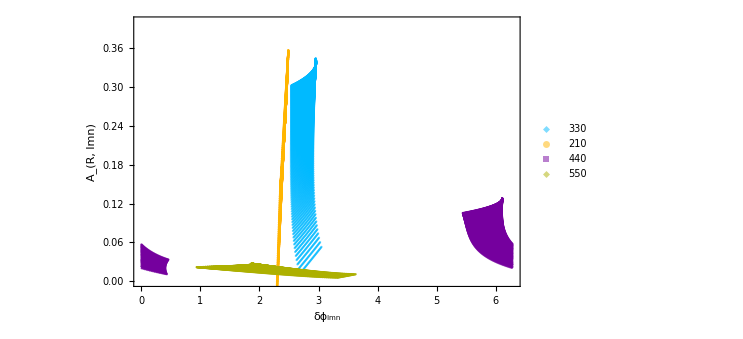

```mathematica
l1=ListPlot[{phsall,phsall21,phsall44,phsall55},FrameStyle->Directive[Black,Bold,26],ImageSize->550,Joined->{False,False,False},PlotStyle->{Directive[colors[[3]],Opacity[0.5]],Directive[colors[[4]],Opacity[0.5]],Directive[colors[[5]],Opacity[0.5]],Directive[colors[[6]],Opacity[0.5]]},Frame->True,PlotLegends->Placed[LineLegend[{Style["330",24],Style["210",24],Style["440",24],Style["550",24]},LegendLayout->{"Column",1},LegendMarkers->{{markers[[3]],0.05},{markers[[1]],0.05},{markers[[2]],0.05}}],{0.75,0.75}],FrameLabel->{"δϕ_lmn","A_(R, lmn)"},Frame->True,PlotRange->{{0,2π},{0,0.4}},FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,16],GridLines->Full]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_phase_modes.png",l1]
```

~/Desktop/RDFits_330/Aratio_phase_modes.png

#### Plot posterior distributions

```mathematica
(* Import Ligo-posterior on the massratio *)
myfile="/Users/xisco/mount/Atlas/sio/git/GW190521/posteriors/4-posterior-ref_xphm.hdf"
logw=Import[myfile,{"Datasets","/samples/logwt"}];
logev=ExternalEvaluate[Global`session, "file='"<>myfile<>"';
f1 = h5py.File(file,'r'); f1.attrs.get('log_evidence')"];
wt=Exp[logw-logev];
weights=wt/Total[wt];
qdistalex=Import[myfile,{"Datasets","/samples/q"}];
χ1=Import[myfile,{"Datasets","/samples/spin1_a"}];
χ2=Import[myfile,{"Datasets","/samples/spin2_a"}];
χefflal=χ1*(qdistalex/(qdistalex+1)^2)+χ2*1/(qdistalex+1)^2;
```

/Users/xisco/mount/Atlas/sio/git/GW190521/posteriors/4-posterior-ref_xphm.hdf

```mathematica
Import[myfile]
```

{/samples/H1_optimal_snrsq,/samples/L1_optimal_snrsq,/samples/V1_optimal_snrsq,/samples/chi_eff,/samples/comoving_volume,/samples/dec,/samples/delta_tc,/samples/distance,/samples/inclination,/samples/logjacobian,/samples/loglikelihood,/samples/loglr,/samples/logprior,/samples/logwt,/samples/maxl_loglr,/samples/maxl_phase,/samples/maxl_polarization,/samples/q,/samples/ra,/samples/spin1_a,/samples/spin1_azimuthal,/samples/spin1_polar,/samples/spin2_a,/samples/spin2_azimuthal,/samples/spin2_polar,/samples/srcmass1,/samples/srcmass2,/samples/srcmtotal}

```mathematica
(* Alex Ligo-posterior on the massratio *)
myfile="/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/reweighted/REWEIGHTED_IMR-XPHM.hdf"
logw=Import[myfile,{"Datasets","/samples/logwt"}];
logev=ExternalEvaluate[Global`session, "file='/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/reweighted/REWEIGHTED_IMR-XPHM.hdf';
f1 = h5py.File(file,'r'); f1.attrs.get('log_evidence')"];
wt=Exp[logw-logev];
weights=wt/Total[wt];
qdist=Import[myfile,{"Datasets","/samples/q"}];
χ1=Import[myfile,{"Datasets","/samples/spin1_a"}];
χ2=Import[myfile,{"Datasets","/samples/spin2_a"}];
srcmtotal=Import[myfile,{"Datasets","/samples/srcmtotal"}];
χeffl=χ1*(qdist/(qdist+1)^2)+χ2*1/(qdist+1)^2;
```

/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/reweighted/REWEIGHTED_IMR-XPHM.hdf

```mathematica
qdistcol=Select[(qq/.Table[FindRoot[amp33[[i]]==a330new[qq,spinmax],{qq,2,1,15}],{i,Length@amp33}]),#≠15&];
```

FindRoot::reged: The point {15.} is at the edge of the search region {1.,15.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
qdistcol2=Select[({qq,χ}/.Table[FindRoot[{amp33[[i]]==a330new[qq,χ],phasediffngr[[i]]==phasediff330[qq,χ]},{qq,2,1,15},{χ,0.7,0.,1}],{i,Length@amp33}]),#[[1]]≠15&];
```

FindRoot::reged: The point {2.81686,0.} is at the edge of the search region {0.,1.} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {1.81126,0.} is at the edge of the search region {0.,1.} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {2.04817,1.} is at the edge of the search region {0.,1.} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
sel=Select[Chop[qdistcol2],#[[2]]≠ 0&&#[[2]]≠ 1&];
```

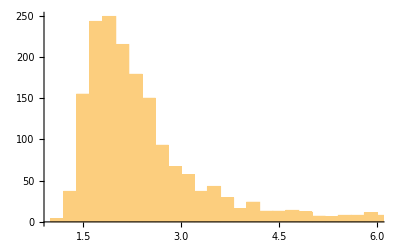

-Graphics-

```mathematica
Histogram[sel[[All,1]]]
Histogram[sel[[All,2]]]
```

```mathematica
ListContourPlot[Select[Chop[qdistcol2],#[[2]]≠ 0&&#[[2]]≠ 1&]]
```

-Graphics-

```mathematica
qdistcolin=SmoothKernelDistribution[qdistcol];
qdistlig=SmoothKernelDistribution[qdist];
amp33dist=SmoothKernelDistribution[Normal[amp33]];
```

```mathematica
itmax=Max[Length@Normal[Normal[amp33]],Length@Normal[qdistcol]];
qdistcolr=RandomVariate[qdistcolin,itmax];
ampq=Transpose[{qdistcolr,amp33}];
ampqdist=SmoothKernelDistribution[ampq];
```

```mathematica
chi2=NMinimize[{χfun[{x,y},ampqdist], 1≤x≤5,0.001≤ y≤0.5},{x,y}][[1]]
```

-2.82164

```mathematica
Histogram[a330new[qdist,χeffl]]
```

-Graphics-

```mathematica
ampqdistl=SmoothKernelDistribution[a330new[qdist,χeffl]]
```

DataDistribution[…]

```mathematica
amp33ligo=x/.NMinimize[{χfun[x,ampqdistl],0.001≤ x≤0.4},{x}][[2]]
```

0.149162

```mathematica
hlc=Histogram2Line[qdistcol,"binwidth"->40];
hlig=Histogram2Line[qdist,"binwidth"->40];
qcolin=Transpose[{Join[{0},hlc[[1]]],Join[{PDF[qdistcolin,0],PDF[qdistcolin,hlc[[1,1]]]},hlc[[2]]]}];
qligo=Transpose[{Join[{0},hlig[[1]]],Join[{PDF[qdistlig,0],PDF[qdistlig,hlig[[1,1]]]},hlig[[2]]]}];
bvalc=Select[qcolin,#[[2]]==Max[qcolin[[All,2]]]&][[1,1]];
bvall=Select[qligo,#[[2]]==Max[qligo[[All,2]]]&][[1,1]];
ampdist=SmoothKernelDistribution[amp33];
hamp33=Histogram2Line[amp33,"binwidth"->40];
amp33h=Transpose[{Join[hamp33[[1]]],Join[{PDF[ampdist,hamp33[[1,1]]]},hamp33[[2]]]}];
valamp33h=Select[amp33h,#[[2]]==Max[amp33h[[All,2]]]&][[1,1]];
```

```mathematica
Histogram[qdistalex]
```

-Graphics-

```mathematica
chiall[[1]]+1
```

3.42801

```mathematica
qdistalexd=SmoothKernelDistribution[qdistalex];
chiall=NMinimize[{χfun[x,qdistalexd],1≤ x≤15},{x}]
qalexmax=x/.chiall[[2]]
chiall1σmin=x/.FindRoot[χfun[x,qdistalexd]==chiall[[1]]+1,{x,5}]
chiall1σmax=x/.FindRoot[χfun[x,qdistalexd]==chiall[[1]]+1,{x,11}]
```

{2.42801,{x→10.8356}}

10.8356

9.82728

11.947

```mathematica
ampqdistalex=SmoothKernelDistribution[Transpose[{qdistalex,a330new[qdistalex,χefflal]}]]
```

DataDistribution[…]

```mathematica
Histogram[a330new[qdistalex,χefflal],PlotRange->All]
```

-Graphics-

```mathematica
qampal={x,y}/.NMinimize[{χfun[{x,y},ampqdistalex], 1≤x≤14.,0.35≤ y≤0.4},{x,y}][[2]]
```

{10.8472,0.370755}

```mathematica
c2=ContourPlot[χfun[{x,y},ampqdistalex],{x,1,14.5},{y,0.005,0.4},ContourShading->None,ContourStyle->colors[[5]],Contours->{chi2+6.25}];
c1=ContourPlot[χfun[{x,y},ampqdist],{x,1,10},{y,0.005,0.5},ContourShading->None,ContourStyle->colors[[2]],Contours->{chi2+6.25}];
lp=ListPlot[{TakeColumn[allampratfin,{1,3}],{{bvalc,valamp33h}},{{bvall,amp33ligo}},{{1/0.43,valamp33h}},{qampal}},Frame->True,FrameLabel->{"q","A_R"},PlotRange->All,Frame->True,FrameStyle->Directive[Black,Bold,26],LabelStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[1;;-1]],IntervalMarkersStyle->colors,
LabelStyle->{FontFamily->"Arial",24,GrayLevel[0],Bold},ImageSize->800,PlotMarkers->{{markers[[3]],Scaled[0.03]},{markers[[1]],Large},{markers[[2]],Scaled[0.05]},{markers[[4]],Scaled[0.05]},{markers[[5]],Scaled[0.05]}},PlotLegends->Placed[LineLegend[{"A_330","Jimenez","LVKC","Capano","Nitz"},LegendLayout->{"Column",3},LegendMarkers->{{markers[[3]],0.1},{markers[[1]],0.1},{markers[[2]],0.1},{markers[[4]],0.1},{markers[[5]],0.1}}],{0.5,0.25}]];
lp=Show[lp,c1,c2]
```

-Graphics-

```mathematica
Export["/Users/xisco/Desktop/RDFits_330/Aratio_q_LIGO_contour.pdf",lp]
```

/Users/xisco/Desktop/RDFits_330/Aratio_q_LIGO_contour.pdf